# Green Functions

## Introduction

Consider a general 2^nd order differential equation. The solution to the homogenous equation

L [y(x)]=0=p(x)y''(x)+q(x)y'(x)+r(x)y(x),

is

y(x)=c_1 y_1(x)+c_2 y_2(x),

where y_1 and y_2 are linearly independent.

## Wronskian

The Wronskian of two solutions to a (second order) differential equation is defined by

W[y_1,y_2][x]=|y_1(x) | y_2(x)
y'_1(x) | y'_2(x)|=y_1(x) y'_2(x)-y_2(x) y'_1(x).

It is obvious how to extend this to higher-order equations.

#### Ratio of dependent solutions

Since

```mathematica
D[(Subscript[f, 2](x))/(Subscript[f, 1](x)),x]//Together
```

(f_1(x) f_2'(x)-f_2(x) f_1'(x))/(f_1(x))^2

if the solutions are linearly dependent then f_1(x)==c f_2(x), and the derivative of the ratio, and hence Wronskian, vanishes.

#### Matching solutions

To solve a (second order) differential equation, by matching solutions and their derivatives at an arbitrary point x, one has

y_1(x)==y_2(x), y'_1(x)==y'_2(x) ⟹(y_1(x))/(y'_1(x))==(y_2(x))/(y'_2(x))⟹(y_1(x) y'_2(x)-y_2(x) y'_1(x))/(y'_1(x)y'_2(x))==0⟺W[y_1,y_2][x]==0

Aquino (1995) applies this idea to obtain a numerical method for computing the eigenvalues of the anharmonic quantum oscillator by matching asymptotic solutions.

### Example

Consider the linearly independent solutions to a second-order homogenous differential equation:

```mathematica
DSolve[y''(x)+k^2 y(x)==0,y(x),x]
```

{{y(x)→c_2 sin(k x)+c_1 cos(k x)}}

We can write the general linear combination as

```mathematica
Subscript[𝓎, i_][x_]:=Subscript[c, i,1] cos(k x)+Subscript[c, i,2] sin(k x)
```

```mathematica
Subscript[𝓎, 1][x_]:= cos(k x)
```

```mathematica
Subscript[𝓎, 2][x_]:= sin(k x)
```

This notation makes it easier to compute derivatives,

```mathematica
Subscript[𝓎, 1]'[x]
```

-k sin(k x)

and hence admits a natural implementation of the Wronskian determinant:

```mathematica
𝒲[u_,v_][x_]:=u[x] v'[x]-u'[x] v[x]
```

```mathematica
𝒲[Subscript[𝓎, 1],Subscript[𝓎, 2]][x]//Simplify
```

k

```mathematica
Wronskian[{Subscript[𝓎, 1](x),Subscript[𝓎, 2](x)},x]
```

k

## General equation

For our differential operator,

y_1(x)L y_2(x)-y_2(x)L y_1(x)=p(x)(y_1(x) y''_2(x)-y_2(x) y''_1(x))+q(x)(y_1(x) y'_2(x)-y_2(x) y'_1(x))
=p(x)W[y_1,y_2]'[x]+q(x)W[y_1,y_2][x]
=0,

This first-order equation for the Wronskian has solution

W[y_1,y_2][x]=c ⅇ^(-∫_0^x q(t)/p(t)ⅆt),

where c is arbitrary.

## Self-adjoint differential equation

The differential equation is self-adjoint if q(x)=p^′(x), i.e.,

L [y(x)]=(p(x)y'(x))'+r(x)y(x)=g(x).

With q(x)=p'(x) we obtain the Wronskian for a self-adjoint operator:

```mathematica
c ⅇ^(-∫_0^x p'(t)/p(t)ⅆt)//Simplify
```

(c p(0))/(p(x))

Hence

W[y_1,y_2][x]=c'/(p(x)),

where c' is arbitrary.

## Variation of Parameters

The method of variation of parameters extends the solution to the inhomogenous equation by making the constants functions of x,

y(x)=c_1(x)y_1(x)+c_2(x)y_2(x).

DONT USE y_n(x)!!!!!!

After differentiation,

y'(x)=(c'_1(x)y_1(x)+c'_2(x)y_2(x))_(=0)+c_1(x)y'_1(x)+c_2(x)y'_2(x),

we are free to impose the indicated condition on the first bracketed term. Differentiating again yields

y''(x)=c'_1(x)y'_1(x)+c'_2(x)y'_2(x)+c_1(x)y''_1(x)+c_2(x)y''_2(x),

and substituting back into the differential equation, the bracketed terms above satisfies the differential equation so we obtain

L [y(x)]=p(x)(c'_1(x)y'_1(x)+c'_2(x)y'_2(x))=g(x),

along with the constraint equation

c'_1(x)y_1(x)+c'_2(x)y_2(x)=0.

Equations (Equation) and (Equation) can be written in the matrix form as

p(x)(y_1(x) | y_2(x)
y'_1(x) | y'_2(x))·(c'_1(x)
c'_2(x))=(0
g(x)).

This solution to this matrix equation is immediate:

(c'_1(x)
c'_2(x))=1/(p(x)W[y_1,y_2][x])(y'_2(x) | -y_2(x)
-y'_1(x) | y_1(x))·(0
g(x))=(g(x))/(p(x)W[y_1,y_2][x])(-y_2(x)
y_1(x)),

for W[y_1,y_2][x]≠0.

Need to apply the homogenous boundary conditions!

y(a)==0, | y(b)==0

The solution to the inhomogenous problem is

y(x)=∫_a^b G(x,t)g(t)ⅆt,

where we identify the Green function,

G(x,t)=1/(p(t) W(y_1,y_2)(t))Piecewise[{{1x2t, a≤t≤x}, {1t 2x, x≤t≤b}}]≡(1x_>2x_<)/(p(t) W(y_1,y_2)(t))

which, for the self-adjoint problem simplifies to

G(x,t)=Piecewise[{{1x2t, a≤t≤x}, {1t 2x, x≤t≤b}}],

(?? where y_1 is a solution of L [y(x)]=0 which satisfies the boundary condition at x=a and y_2 is a solution of L [y(x)]=0 which satisfies the boundary condition at x=b. ??)

### Example

For the second-order homogenous differential equation,

```mathematica
DSolve[y''(x)+k^2 y(x) ==0,y,x]
```

{{y→({x}↦c_2 sin(k x)+c_1 cos(k x))}}

```mathematica
{y(0)==0,y(L)==0}/.First[%]
```

{c_1==0,c_2 sin(k L)+c_1 cos(k L)==0}

```mathematica
Reduce[%]
```

(sin(k L)==0∧c_1==0)∨(sin(k L)≠0∧c_2==0∧c_1==0)

```mathematica
k L==n π
```

the Green function reads

```mathematica
𝒢(x_,t_)= (Subscript[y, 2](x)Subscript[y, 1](t)-Subscript[y, 1](x) Subscript[y, 2](t))/(𝒲[Subscript[y, 1],Subscript[y, 2]][t])//Simplify
```

-(sin(k (t-x)))/k

The solution to the inhomogoneous differential equation with homogeneous boundary conditions

y''(x)+k^2 y(x) =x (π-x) , y(0)=0, y(π)=0,

```mathematica
𝒢[x,π]//TrigExpand
```

(cos(k π) sin(k x)-cos(k x) sin(k π))/k

```mathematica
𝒢[π,0]
```

(sin(k π))/k

is

```mathematica
g(x_)=x (1-x);
```

```mathematica
SetOptions[Integrate,Assumptions->{k>0∧x>0}];
```

```mathematica
SetOptions[Integrate,Assumptions->{}];
```

```mathematica
Options[Integrate]
```

{Assumptions→{},GenerateConditions→Automatic,PrincipalValue→False}

```mathematica
∫_0^x g(t)𝒢(x,t)ⅆt//Simplify
```

(-x^2 k^2+x k^2-sin(k x) k-2 cos(k x)+2)/k^4

```mathematica
y''(x)+k^2 y(x) ==g(x)/.y->Function[x,(-x^2 k^2+x k^2-sin(k x) k-2 cos(k x)+2)/k^4]//Simplify
```

True

```mathematica
Function[x,(-x^2 k^2+x k^2-sin(k x) k-2 cos(k x)+2)/k^4][0]
```

0

```mathematica
Function[x,(-x^2 k^2+x k^2-sin(k x) k-2 cos(k x)+2)/k^4][π]
```

(-π^2 k^2+π k^2-sin(k π) k-2 cos(k π)+2)/k^4

```mathematica
Simplify[%]
```

(-π^2 k^2+π k^2-sin(k π) k-2 cos(k π)+2)/k^4

```mathematica
Simplify[%,k∈ℤ]
```

(-(-1+π) π k^2-2 (-1)^k+2)/k^4

```mathematica
DSolve[{y''(x)+k^2 y(x) ==g(x),y(0)==0,y(π)==0},y(x),x]//FullSimplify
```

{{y(x)→(-(x-1) x k^2-2 cos(k x)+((-1+π) π k^2+2 cos(k π)-2) csc(k π) sin(k x)+2)/k^4}}

```mathematica
(-x^2 k^2+x k^2+π^2 csc(k π) sin(k x) k^2-π csc(k π) sin(k x) k^2-2 cos(k x)+2 cot(k π) sin(k x)-2 csc(k π) sin(k x)+2)/k^4-(-x^2 k^2+x k^2-sin(k x) k-2 cos(k x)+2)/k^4//Expand
```

(2 cot(k π) sin(k x))/k^4-(2 csc(k π) sin(k x))/k^4+(π^2 csc(k π) sin(k x))/k^2-(π csc(k π) sin(k x))/k^2+(sin(k x))/k^3

```mathematica
Simplify[%]
```

(csc(k π) (π^2 k^2-π k^2+sin(k π) k+2 cos(k π)-2) sin(k x))/k^4

```mathematica
FullSimplify[%]
```

(csc(k π) ((-1+π) π k^2+sin(k π) k+2 cos(k π)-2) sin(k x))/k^4

## Table from Whitten and McCormick

Solve

(ⅆ^2 y(x))/(ⅆ x^2)+k^2 y(x)=g(x)

y(x)=c_1(x)y_1(x)+c_2(x)y_2(x).

(c'_1(x)
c'_2(x))=g(x)(-y_2(x)
y_1(x)),

∫_a^L sin(k x)

```mathematica
Subscript[G, 1]=Function[{x,y},(sin(k x) sin(k (L-y)))/(k sin(k L))];
```

```mathematica
Subscript[G, 2]=Function[{x,y},(sin(k y) sin(k (L-x)))/(k sin(k L))];
```

```mathematica
{g(0,y),g(x,L)}/.g->Subscript[G, 1]//Simplify
```

{0,0}

```mathematica
{g(x,0),g(L,y)}/.g->Subscript[G, 2]//Simplify
```

{0,0}

```mathematica
(∂^2 g(x,y))/(∂x^2)+k^2 g(x,y)/.g->Subscript[G, 1]//Simplify
```

0

```mathematica
(∂^2 g(x,y))/(∂x^2)+k^2 g(x,y)/.g->Subscript[G, 2]//Simplify
```

0

```mathematica
TrigExpand[sin(k (L-x))]
```

cos(k x) sin(k L)-cos(k L) sin(k x)

```mathematica
Subscript[G, 1](x,y)==Subscript[G, 2](y,x)
```

True

```mathematica
TrigExpand[Subscript[G, 1](x,y)]
```

(cos(k y) sin(k x)-cot(k L) sin(k x) sin(k y))/k

```mathematica
TrigExpand[Subscript[G, 2](x,y)]
```

(cos(k x) sin(k y)-cot(k L) sin(k x) sin(k y))/k

(ⅆ^2 g(x))/(ⅆ x^2)+k^2 g(x)=-δ(x-x_0) | g(0)=0 | g(L)=0 | 1 | (sin(k x) sin(k (L-x_0)))/(k sin(k L)) | x<x_0
(sin(k x_0) sin(k (L-x)))/(k sin(k L)) | x>x_0

ⅆ/ⅆx+k^2 g(x)=-δ(x-x_0) | g(0)=0 | g(L)=0 | 1 | (sin(k x) sin(k (L-x_0)))/(k sin(k L)) | x<x_0 | □ | □
□ | □

## Resonant equations

Consider the Legendre differential equation

ⅆ_x((1-x^2) ⅆ_x f_ν(x))+ν (ν+1) f_ν(x)=0

Write this more compactly as

𝒟_ν(f_ν(x))=0

where the implied differential operator 𝒟_ν is

```mathematica
Subscript[𝒟, ν_](f_):=D[((1-x^2) D[f, x]), x]+ν (ν+1) f
```

Solutions to the homogenous differential equation are immediate.

```mathematica
DSolve[Subscript[𝒟, ν](Subscript[f, ν](x))==0,Subscript[f, ν](x),x]
```

{{f_ν(x)→c_1 P_ν(x)+c_2 Q_ν(x)}}

The “resonant” Legendre equation is

𝒟_ν(f_ν(x))=l_ν(x).

where l_ν(x) is a solution to the homogenous differential equation, l_ν(x)=c_1 P_ν(x)+c_2 Q_ν(x).

To solve this equation, consider the ansatz f_ν(x)=α l_ν(x)ln(1-x^2)+k_ν(x) where α needs to be chosen so that the equation determining k_ν(x)is non-resonant. Substituting the ansatz into the differential equation, and using the fact that l_ν(x) is a solution to the homogenous differential equation, we obtain

```mathematica
Collect[Subscript[𝒟, ν](Subscript[f, ν](x))-Subscript[l, ν](x)/.Subscript[f, ν]->(x↦Subscript[k, ν](x)+α ln(1-x^2) Subscript[l, ν](x)),{ln(_)},FullSimplify]/.Simplify[Subscript[𝒟, ν](Subscript[l, ν](x))]->0
```

ν (ν+1) k_ν(x)-(2 α+1) l_ν(x)-2 x (k'_ν(x)+2 α l'_ν(x))-(x^2-1) k''_ν(x)

```mathematica
Collect[%,{Subscript[k, ν](x),Subscript[k, ν]'(x),Subscript[k, ν]''(x)},Simplify]
```

ν (ν+1) k_ν(x)-(2 α+1) l_ν(x)-2 x k'_ν(x)-4 x α l'_ν(x)+(1-x^2) k''_ν(x)

Clearly, this can be re-written as

𝒟_ν(k_ν(x))=(2 α+1) l_ν(x)+4 x α l'_ν(x)

```mathematica
%==(Subscript[𝒟, ν](Subscript[k, ν](x))-((2 α+1) Subscript[l, ν](x)+4 x α Subscript[l, ν]'(x)))//Simplify
```

True

Explicitly, the right-hand side of (Equation) is

```mathematica
rhs=(2 α+1) Subscript[l, ν](x)+4 x α Subscript[l, ν]'(x)/.Subscript[l, ν]->(x↦νx)//Simplify
```

(2 α+1) P_ν(x)+(4 x α (x ν P_ν(x)-ν P_(ν-1)(x)))/(x^2-1)

We need to choose α so that this expression, expanded into a (finite) series in Legendre polynomials, does not contain P_ν(x). For ν=n∈ℤit can be verified that

(x n (x P_n(x)-P_(n-1)(x)))/(x^2-1)=x(∂P_n(x))/(∂x)=n P_n(x)+(∂P_(n-1)(x))/(∂x)=n P_n(x)+∑_(l=If[OddQ[n],1/2,0])^⌊(n-1)/2⌋ (4 l+1) P_(2 l)(x).

```mathematica
ℛ=Subscript[P, ν_](z_) z_^(k_.)->(ν Subscript[P, ν-1](z) z^(k-1)+(ν+1) Subscript[P, ν+1](z) z^(k-1))/(2 ν+1);
```

```mathematica
ExpandNumerator[x(∂Subscript[P, n](x))/(∂x)-(n Subscript[P, n](x)+(∂Subscript[P, n-1](x))/(∂x))//FullSimplify]//.ℛ//Simplify
```

0

Hence the coefficient of P_n(x) on the right-hand side of (Equation) is (2 α+1)+4α n. Solving for α,

```mathematica
Solve[(2 α+1)+4α n==0,α]//Factor
```

{{α→-1/(4 n+2)}}

the right-hand side of (Equation) becomes

(2 n (x P_(n-1)(x)-P_n(x)))/((2 n+1) (x^2-1))=-2/(2 n+1)(∂P_(n-1)(x))/(∂x)=-2/(2 n+1)(∑_(l=If[OddQ[n],1/2,0])^⌊(n-1)/2⌋ (4 l+1) P_(2 l)(x))

```mathematica
Table[∑_(l=If[OddQ[n],1/2,0])^⌊(n-1)/2⌋ (4 l+1) Subscript[P, 2 l](x)==Sum[(2 l+1) Subscript[P, l](x),{l,If[OddQ[n],1,0],n-1,2}],{n,0,3}]
```

{True,True,True,True}

To summarise, with f_ν(x)=-1/(2 (2ν+1)) l_ν(x)ln(1-x^2)+k_ν(x), we now have to solve the following non-resonant equation:

𝒟_ν(k_ν(x))=-2/(2 n+1)(∂P_(n-1)(x))/(∂x).

g_ν(x,x_0)=1/2∑_(l≠ν=0)^∞ (2 l+1)/((l-ν) (l+ν+1)) P_l(x) P_l(x_0)=1/2(∑_(l≠ν=0)^∞ 1/(l+ν+1) P_l(x) P_l(x_0)+∑_(l≠ν=0)^∞ 1/(l-ν) P_l(x) P_l(x_0))

k_n(x_0)=2/(2 n+1)∫_-1^1 g_n(x,x_0)(∂P_(n-1)(x))/(∂x)ⅆx
=1/(2 n+1)∑_(l≠n=0)^∞ (2 l+1)/((l-n) (l+n+1)) (∫_-1^1 P_l(x)(∂P_(n-1)(x))/(∂x)ⅆx) P_l(x_0)
=1/(2 n+1)∑_(l≠ν=0)^∞ (2 l+1)/((l-n) (l+n+1)) (∑_(p=If[OddQ[n],1/2,0])^⌊(n-1)/2⌋ (4 p+1)∫_-1^1 P_l(x)P_(2 p)(x)ⅆx) P_l(x_0)
=2/(2 n+1)∑_(p=If[OddQ[n],1/2,0])^⌊(n-1)/2⌋ (4p+1)/((2p-n) (2p+n+1))P_(2p)(x_0).

```mathematica
Apart[(4p+1)/((2p-n) (2p+n+1)),p]
```

1/(n+2 p+1)+1/(2 p-n)

```mathematica
Subscript[k, l_](x_):=Subscript[k, l](x)=2/(2 l+1)∑_{{n=Subscript[n, l]}, {Δ n=2}}^(l-2) (2n+1)/((n-l) (n+l+1))Subscript[P, n](x)
```

```mathematica
Table[{l,-(2l+5)Subscript[k, l+2](x)},{l,0,8}]//Simplify//Expand
```

(0 | 1/3
1 | (3 x)/5
2 | (15 x^2)/14-9/35
3 | (35 x^3)/18-(20 x)/21
4 | (315 x^4)/88-(175 x^2)/66+1195/5544
5 | (693 x^5)/104-(945 x^3)/143+(12565 x)/10296
6 | (1001 x^6)/80-(1617 x^4)/104+(10563 x^2)/2288-973/5148
7 | (6435 x^7)/272-(3003 x^5)/85+(51667 x^3)/3536-(28077 x)/19448
8 | (109395 x^8)/2432-(405405 x^6)/5168+(863863 x^4)/20672-(57981 x^2)/8398+5033469/29560960)

```mathematica
Table[(2 l+1) Subscript[P, n](x)//Expand,{l,0,10}]
```

{0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[{n,-(2n+5)Subscript[k, n+2](x)},{n,0,8}]//Simplify//Expand
```

(0 | 1/3
1 | (3 x)/5
2 | (15 x^2)/14-9/35
3 | (35 x^3)/18-(20 x)/21
4 | (315 x^4)/88-(175 x^2)/66+1195/5544
5 | (693 x^5)/104-(945 x^3)/143+(12565 x)/10296
6 | (1001 x^6)/80-(1617 x^4)/104+(10563 x^2)/2288-973/5148
7 | (6435 x^7)/272-(3003 x^5)/85+(51667 x^3)/3536-(28077 x)/19448
8 | (109395 x^8)/2432-(405405 x^6)/5168+(863863 x^4)/20672-(57981 x^2)/8398+5033469/29560960)

```mathematica
Table[Subscript[𝒟, n](Subscript[h, n](x))-Subscript[P, n](x)/.Subscript[h, n_]:>Function[x,-1/(2 (2 n+1))Subscript[P, n](x) (log(x-1)+log(x+1))+Subscript[k, n](x)],{n,0,10}]//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[SolveAlways[∑_(m=0)^n Subscript[a, m] Subscript[P, m](x) Subscript[P, n-m](x)==-(2n+5)Subscript[k, n+2](x),x],{n,0,8}]
```

({a_0→1/3}
{a_0→3/5-a_1}
{a_0→18/35-a_2,a_1→3/10}
{a_0→115/252-a_3,a_1→15/28-a_2}
{a_0→865/2079-a_4,a_1→185/378-a_3,a_2→5/21}
{a_0→35833/92664-a_5,a_1→1085/2376-a_4,a_2→35/81-a_3}
{a_0→469/1287-a_6,a_1→8351/19305-a_5,a_2→119/297-a_4,a_3→7/36}
{a_0→13495/38896-a_7,a_1→4739/11440-a_6,a_2→4319/11440-a_5,a_3→63/176-a_4}
{a_0→4843673/14549535-a_8,a_1→4082537/10210200-a_7,a_2→23159/64350-a_6,a_3→1917/5720-a_5,a_4→9/55})

```mathematica
Subscript[W, n_](x_):=Subscript[W, n](x)=Simplify[∑_(m=1)^(n+1) (Subscript[P, m-1](x) Subscript[P, n+1-m](x))/m]
```

```mathematica
Table[{n,Subscript[W, n](x)},{n,-1,3}]
```

(-1 | 0
0 | 1
1 | (3 x)/2
2 | (5 x^2)/2-2/3
3 | 5/24 x (21 x^2-11))

```mathematica
sols=Simplify[Table[DSolve[Subscript[𝒟, ν](Subscript[h, ν](x))==Subscript[P, ν](x),Subscript[h, ν](x),x],{ν,0,6}],-1<x<1]
```

({h_0(x)→c_2+1/2 (c_1-1) log(x-1)-1/2 (c_1+1) log(x+1)}
{h_1(x)→1/6 (6 x c_1-6 c_2-x log(x-1)-x log(x+1)+3 x c_2 log((x+1)/(1-x)))}
{h_2(x)→1/20 (-4 x^2+10 (3 x^2-1) c_1+(1-3 x^2) log(x-1)+(1-3 x^2) log(x+1)+5 c_2 ((3 x^2-1) log((x+1)/(1-x))-6 x))}
{h_3(x)→1/84 (42 x (5 x^2-3) c_1+3 (-4 x^3+(3 x-5 x^3) log(x-1)+(3 x-5 x^3) log(x+1))+7 c_2 (-30 x^2+3 (5 x^2-3) log((x+1)/(1-x)) x+8))}
{h_4(x)→1/144 (-48 x^4+24 x^2+18 (35 x^4-30 x^2+3) c_1+(-35 x^4+30 x^2-3) log(x-1)+(-35 x^4+30 x^2-3) log(x+1)+3 c_2 (-210 x^3+110 x+3 (35 x^4-30 x^2+3) log((x+1)/(1-x))))}
{h_5(x)→1/8 x (63 x^4-70 x^2+15) c_1-1/176 x (8 (8 x^2-5) x^2+(63 x^4-70 x^2+15) log(x-1)+(63 x^4-70 x^2+15) log(x+1))+1/240 c_2 (15 x (63 x^4-70 x^2+15) log((x+1)/(1-x))-2 (945 x^4-735 x^2+64))}
{h_6(x)→(390 (231 x^6-315 x^4+105 x^2-5) c_1+5 (-4 (239 x^4-240 x^2+45) x^2+(-693 x^6+945 x^4-315 x^2+15) log(x-1)+(-693 x^6+945 x^4-315 x^2+15) log(x+1))+39 c_2 (5 (231 x^6-315 x^4+105 x^2-5) log((x+1)/(1-x))-14 x (165 x^4-170 x^2+33)))/6240})

```mathematica
Simplify[(Subscript[h, 2](x)-Subscript[k, 2](x))/(Subscript[P, 2](x) (log(x-1)+log(x+1)))/.Flatten[sols]/.Subscript[c, 2]->0/.Subscript[c, 1]->2/15]
```

-1/10

```mathematica
Simplify[(Subscript[h, 3](x)-Subscript[k, 3](x))/(Subscript[P, 3](x) (log(x-1)+log(x+1)))/.Flatten[sols]/.Subscript[c, 2]->0/.Subscript[c, 1]->2/35]
```

-1/14

```mathematica
Simplify[(Subscript[h, 4](x)-Subscript[k, 4](x))/(Subscript[P, 4](x) (log(x-1)+log(x+1)))/.Flatten[sols]/.Subscript[c, 2]->0/.Subscript[c, 1]->8/105]
```

-1/18

```mathematica
Simplify[(Subscript[h, 5](x)-Subscript[k, 5](x))/(Subscript[P, 5](x) (log(x-1)+log(x+1)))/.Flatten[sols]/.Subscript[c, 2]->0/.Subscript[c, 1]->32/693]
```

-1/22

```mathematica
Simplify[(Subscript[h, 6](x)-Subscript[k, 6](x))/(Subscript[P, 6](x) (log(x-1)+log(x+1)))/.Flatten[sols]/.Subscript[c, 2]->0/.Subscript[c, 1]->478/9009]
```

-1/26

```mathematica
Table[DSolve[Subscript[𝒟, ν]( Subscript[h, ν](x))==Subscript[P, ν](x),Subscript[h, ν](x),x],{ν,0,8}]/.Subscript[c, _]->0/.log(x-1)->log(1-x^2)-log(x+1)//Simplify
```

({h_0(x)→-1/2 log(1-x^2)}
{h_1(x)→-1/6 x log(1-x^2)}
{h_2(x)→1/20 ((1-3 x^2) log(1-x^2)-4 x^2)}
{h_3(x)→1/28 ((3 x-5 x^3) log(1-x^2)-4 x^3)}
{h_4(x)→1/144 (-48 x^4+24 x^2+(-35 x^4+30 x^2-3) log(1-x^2))}
{h_5(x)→1/176 (8 (5-8 x^2) x^3+(-63 x^5+70 x^3-15 x) log(1-x^2))}
{h_6(x)→((-693 x^6+945 x^4-315 x^2+15) log(1-x^2)-4 x^2 (239 x^4-240 x^2+45))/1248}
{h_7(x)→(-4 (359 x^4-420 x^2+105) x^3-3 (429 x^6-693 x^4+315 x^2-35) log(1-x^2) x)/1440}
{h_8(x)→(16 x^2 (-1668 x^6+2513 x^4-1050 x^2+105)-3 (6435 x^8-12012 x^6+6930 x^4-1260 x^2+35) log(1-x^2))/13056})

```mathematica
Collect[%,{Subscript[p, ν](x),Subscript[p, ν]'(x)},Simplify]
```

p_ν(x) (-2 x g'(x)-(x^2-1) g''(x)-1)-2 (x^2-1) g'(x) p'_ν(x)

```mathematica
DSolve[-2 x g'(x)-(x^2-1) g''(x)-1==0,g,x]
```

{{g→Function[{x},c_2+1/2 (c_1-1) log(x-1)+1/2 (-c_1-1) log(x+1)]}}

```mathematica
2 (x^2-1) g'(x) Subscript[p, ν]'(x)/.First[%]//Simplify
```

-2 (x-c_1) p'_ν(x)

Following Backhouse …

```mathematica
Subscript[ⅆ, x]((1-x^2) Subscript[ⅆ, x] Subscript[f, ν](x))+(ν+1) ν Subscript[f, ν](x)-Subscript[p, ν](x)/.Subscript[f, ν]->Function[x,α Subscript[p, ν](x)ln(1-x^2)+Subscript[k, ν](x)]//Simplify
```

-k''_ν(x) x^2-α log(1-x^2) p''_ν(x) x^2-2 k'_ν(x) x-4 α p'_ν(x) x-2 α log(1-x^2) p'_ν(x) x+ν (ν+1) k_ν(x)+(ν (ν+1) log(1-x^2) α-2 α-1) p_ν(x)+k''_ν(x)+α log(1-x^2) p''_ν(x)

```mathematica
Collect[%,{ln(_)},Simplify]
```

-k''_ν(x) x^2-2 k'_ν(x) x-4 α p'_ν(x) x+ν (ν+1) k_ν(x)-(2 α+1) p_ν(x)+k''_ν(x)+α log(1-x^2) (ν (ν+1) p_ν(x)-2 x p'_ν(x)-(x^2-1) p''_ν(x))

```mathematica
%/.ν (ν+1) Subscript[p, ν](x)-2 x Subscript[p, ν]'(x)-(x^2-1) Subscript[p, ν]''(x)->0
```

-k''_ν(x) x^2-2 k'_ν(x) x-4 α p'_ν(x) x+ν (ν+1) k_ν(x)-(2 α+1) p_ν(x)+k''_ν(x)

```mathematica
Collect[%,{Subscript[k, ν](x),Subscript[k, ν]'(x),Subscript[k, ν]''(x)},Simplify]
```

ν (ν+1) k_ν(x)-(2 α+1) p_ν(x)-2 x k'_ν(x)-4 x α p'_ν(x)+(1-x^2) k''_ν(x)

```mathematica
%/.α->-1/2
```

ν (ν+1) k_ν(x)-2 x k'_ν(x)+2 x p'_ν(x)+(1-x^2) k''_ν(x)

```mathematica
DSolve[(ν (ν+1) Subscript[k, ν](x)-2 x Subscript[k, ν]'(x)+2 x Subscript[p, ν]'(x)+(1-x^2) Subscript[k, ν]''(x)/.Subscript[p, ν]->Function[x,Subscript[P, ν](x)]/.ν->0)==0,Subscript[k, 0](x),x]
```

{{k_0(x)→c_2+c_1 (1/2 log(x-1)-1/2 log(x+1))}}

```mathematica
2 x Subscript[p, ν]'(x)/.Subscript[p, ν]->Function[x,Subscript[P, ν](x)]//Simplify
```

(2 x (x ν P_ν(x)-ν P_(ν-1)(x)))/(x^2-1)

```mathematica
%102//.ℛ
```

(2 x ((ν (ν P_(ν-1)(x)+(ν+1) P_(ν+1)(x)))/(2 ν+1)-ν P_(ν-1)(x)))/(x^2-1)

```mathematica
ExpandNumerator[%]
```

((2 x P_(ν-1)(x) ν^2)/(2 ν+1)+(2 x P_(ν+1)(x) ν^2)/(2 ν+1)-2 x P_(ν-1)(x) ν+(2 x P_(ν+1)(x) ν)/(2 ν+1))/(x^2-1)

```mathematica
%//.ℛ
```

((2 ((ν-1) P_(ν-2)(x)+ν P_ν(x)) ν^2)/((2 (ν-1)+1) (2 ν+1))+(2 ((ν+1) P_ν(x)+(ν+2) P_(ν+2)(x)) ν^2)/((2 ν+1) (2 (ν+1)+1))-(2 ((ν-1) P_(ν-2)(x)+ν P_ν(x)) ν)/(2 (ν-1)+1)+(2 ((ν+1) P_ν(x)+(ν+2) P_(ν+2)(x)) ν)/((2 ν+1) (2 (ν+1)+1)))/(x^2-1)

```mathematica
Simplify[%]
```

-(2 ν (ν+1) ((2 ν^2+ν-3) P_(ν-2)(x)+(2 ν+1) P_ν(x)+(-2 ν^2-3 ν+2) P_(ν+2)(x)))/((x^2-1) (2 ν-1) (2 ν+1) (2 ν+3))

```mathematica
FullSimplify[%]
```

-(2 ν (ν+1) ((2 ν^2+ν-3) P_(ν-2)(x)+(2 ν+1) P_ν(x)-(ν+2) (2 ν-1) P_(ν+2)(x)))/((x^2-1) (2 ν-1) (2 ν+1) (2 ν+3))

```mathematica
DSolve[(ν (ν+1) Subscript[k, ν](x)-2 x Subscript[k, ν]'(x)+2 x Subscript[p, ν]'(x)+(1-x^2) Subscript[k, ν]''(x)/.Subscript[p, ν]->Function[x,Subscript[P, ν](x)]/.ν->1)==0,Subscript[k, 1](x),x]
```

{{k_1(x)→x c_1+1/3 (x log(x-1)+x log(x+1))+c_2 (1/2 x log((x+1)/(1-x))-1)}}

```mathematica
(2 ((ν+1) Subscript[p, ν](x)+x Subscript[p, ν]'(x)))/(2 ν+1)/.Subscript[p, ν]->Function[x,Subscript[P, ν](x)]//Together//Simplify
```

(2 ((2 ν+1) x^2-ν-1) P_ν(x)-2 x ν P_(ν-1)(x))/((x^2-1) (2 ν+1))

```mathematica
2/(2ν+1)(∂Subscript[P, ν](x))/(∂x)
```

(2 (x ν P_ν(x)-ν P_(ν-1)(x)))/((x^2-1) (2 ν+1))

```mathematica
Simplify[%]
```

-3 P_ν(x)-(4 x (x ν P_ν(x)-ν P_(ν-1)(x)))/(x^2-1)

```mathematica
DSolve[-2 x g'(x)-(x^2-1) g''(x)-1==0,g,x]
```

{{g→Function[{x},c_2+1/2 (c_1-1) log(x-1)+1/2 (-c_1-1) log(x+1)]}}

```mathematica
2 (x^2-1) g'(x) Subscript[p, ν]'(x)/.First[%]//Simplify
```

-2 (x-c_1) p'_ν(x)

```mathematica
(x^2-1)(∂Subscript[P, ν](x))/(∂x)
```

x ν P_ν(x)-ν P_(ν-1)(x)

```mathematica
%/.log(x-1)->log(1-x^2)-log(x+1)//Simplify
```

({h_0(x)→-1/2 log(1-x^2)}
{h_1(x)→-1/6 x log(1-x^2)}
{h_2(x)→1/20 ((1-3 x^2) log(1-x^2)-4 x^2)}
{h_3(x)→1/28 ((3 x-5 x^3) log(1-x^2)-4 x^3)}
{h_4(x)→1/144 (-48 x^4+24 x^2+(-35 x^4+30 x^2-3) log(1-x^2))}
{h_5(x)→1/176 (8 (5-8 x^2) x^3+(-63 x^5+70 x^3-15 x) log(1-x^2))}
{h_6(x)→((-693 x^6+945 x^4-315 x^2+15) log(1-x^2)-4 x^2 (239 x^4-240 x^2+45))/1248}
{h_7(x)→(-4 (359 x^4-420 x^2+105) x^3-3 (429 x^6-693 x^4+315 x^2-35) log(1-x^2) x)/1440}
{h_8(x)→(16 x^2 (-1668 x^6+2513 x^4-1050 x^2+105)-3 (6435 x^8-12012 x^6+6930 x^4-1260 x^2+35) log(1-x^2))/13056})

```mathematica
Table[{ν,-(Subscript[P, ν](x))/(2 (2ν+1))log(1-x^2)},{ν,0,5}]
```

(0 | -1/2 log(1-x^2)
1 | -1/6 x log(1-x^2)
2 | 1/10 (1/2-(3 x^2)/2) log(1-x^2)
3 | 1/14 ((3 x)/2-(5 x^3)/2) log(1-x^2)
4 | 1/18 (-(35 x^4)/8+(15 x^2)/4-3/8) log(1-x^2)
5 | 1/22 (-(63 x^5)/8+(35 x^3)/4-(15 x)/8) log(1-x^2))

```mathematica
∫ Subscript[Q, 0](x)ⅆx
```

1/2 (log(x-1)+log(x+1)+x log((x+1)/(1-x)))

```mathematica
∫ Subscript[Q, 1](x)ⅆx
```

1/4 log((x+1)/(1-x)) x^2-x/2+1/4 log(x-1)-1/4 log(x+1)

Orthogonality of P_l(x)reads

∫_-1^1 P_l(x) P_l'(x)ⅆx=(2 δ_(l,l'))/(2 l+1)

Completeness of P_l(x)reads

∑_(l=0)^∞ (2 l+1) P_l(x) P_l(x')=2δ(x-x')

Only “half” the result applies when x'=1.

∑_(l=0)^∞ (2 l+1) P_l(x) =4δ(1-x)

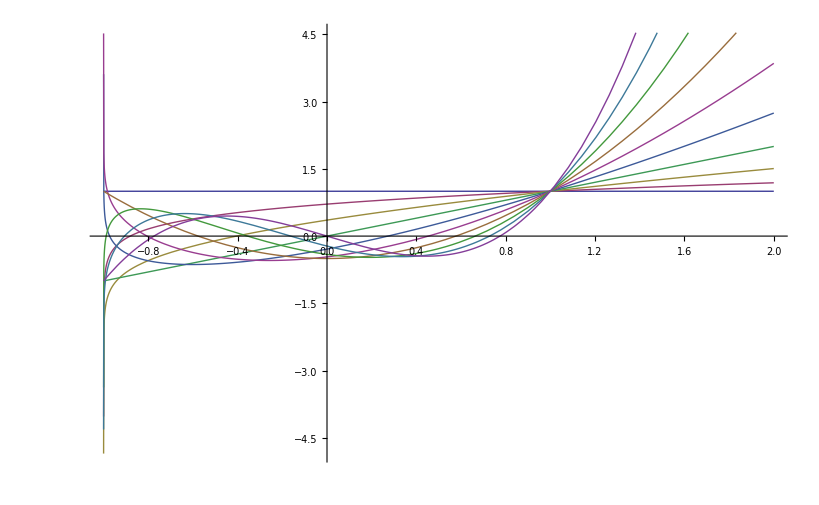

```mathematica
Plot[Evaluate[Table[Tooltip[Subscript[P, l](x),l],{l,0,3,1/3}]],{x,-1,2}]
```

```mathematica
Subscript[P, n](x)+O[x,-1]^2//FullSimplify
```

((H_(-n-1)+H_n+log((x+1)/2)) sin(n π))/π-((n (n+1) (H_-n+H_(n+1)+log(x+1)-log(2)-2) sin(n π)) (x+1))/(2 π)+O((x+1)^2)

```mathematica
(ⅆ((1-x^2) (ⅆf(x))/ⅆx))/ⅆx+(ν (ν+1)-μ^2/(1-x^2)) f(x)==-δ(x-Subscript[x, 0])
```

(ⅆ((1-x^2) (ⅆg_ν(x,x_0))/ⅆx))/ⅆx+ν (ν+1) g_ν(x,x_0)=-δ(x-x_0)=((2 ν+1)/2)P_ν(x) P_ν(x_0)-1/2∑_(l=0)^∞ (2 l+1) P_l(x) P_l(x_0)?

g(x,x_0)=∑_(l=0)^∞ a_l P_l(x) P_l(x_0)⇒(ⅆ((1-x^2) (ⅆg(x,x_0))/ⅆx))/ⅆx+ν (ν+1) g(x,x_0)=∑_(l=0)^∞ a_l ((ν (ν+1)-l (l+1))P)_l(x) P_l(x_0)⇒a_l=-1/2(2 l+1)/(ν (ν+1)-l (l+1))

g_ν(x,x_0)=1/2∑_(l≠ν=0)^∞ (2 l+1)/((l-ν) (l+ν+1)) P_l(x) P_l(x_0)=1/2(∑_(l≠ν=0)^∞ 1/(l+ν+1) P_l(x) P_l(x_0)+∑_(l≠ν=0)^∞ 1/(l-ν) P_l(x) P_l(x_0))

Using the generalized (reduced) Green function,

-∫_-1^1 P_n(x_0) g_ν(x,x_0)ⅆ x_0=-1/((n-ν) (n+ν+1)) P_n(x)/;n≠ν

∫_-1^1 P_ν(x) Q_ρ(x)ⅆx=1/((ν-ρ) (ν+ρ+1))(1-cos((ρ-ν) π)-2/π sin(π ν) cos(π ν) (ψ(ν+1)-ψ(ρ+1)))/;ρ≠ν

Q_ρ(x)=∑_(l=0)^∞ a_l P_l(x) ⇒1/((l-ρ) (l+ρ+1))(1-cos((ρ-l) π))=2/(2l+1)a_l⇒a_l=1/2(2 l+1)/((l-ρ) (l+ρ+1))(1-cos((ρ-l) π)).

```mathematica
1/2(2 l+1)/((l-ρ) (l+ρ+1))(1-cos((ρ-l) π))/.ρ->0
```

((2 l+1) (1-cos(l π)))/(2 l (l+1))

```mathematica
Simplify[1/2(2 l+1)/((l-ρ) (l+ρ+1))(1-cos((ρ-l) π))/.ρ->0/.l->2 l,l∈ℤ]
```

0

```mathematica
Factor[Simplify[1/2(2 l+1)/((l-ρ) (l+ρ+1))(1-cos((ρ-l) π))/.ρ->0/.l->2 l+1,l∈ℤ]]
```

(4 l+3)/(2 (l+1) (2 l+1))

```mathematica
Factor[Simplify[1/2(2 l+1)/((l-ρ) (l+ρ+1))(1-cos((ρ-l) π))/.ρ->1/.l->2 l,l∈ℤ]]
```

(4 l+1)/(2 (l+1) (2 l-1))

```mathematica
1/2(2 l+1)/((l-ρ) (l+ρ+1))1/(1-cos((ρ-l) π))
```

Q_0(x)=1/2∑_(l=0)^∞ (4 l+3)/((l+1) (2l+1)) P_(2l+1)(x)

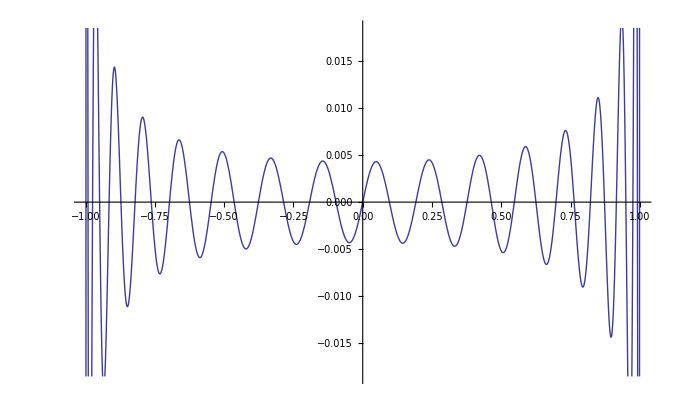

```mathematica
Plot[Evaluate[Subscript[Q, 0](x)-1/2∑_(l=0)^15 (4 l+3)/((2l+1) (l+1)) Subscript[P, 2l+1](x) ],{x,-1,1}]
```

Q_1(x)=1/2∑_(l=0)^∞ (4 l+1)/((2l-1) (l+1)) P_(2l)(x)

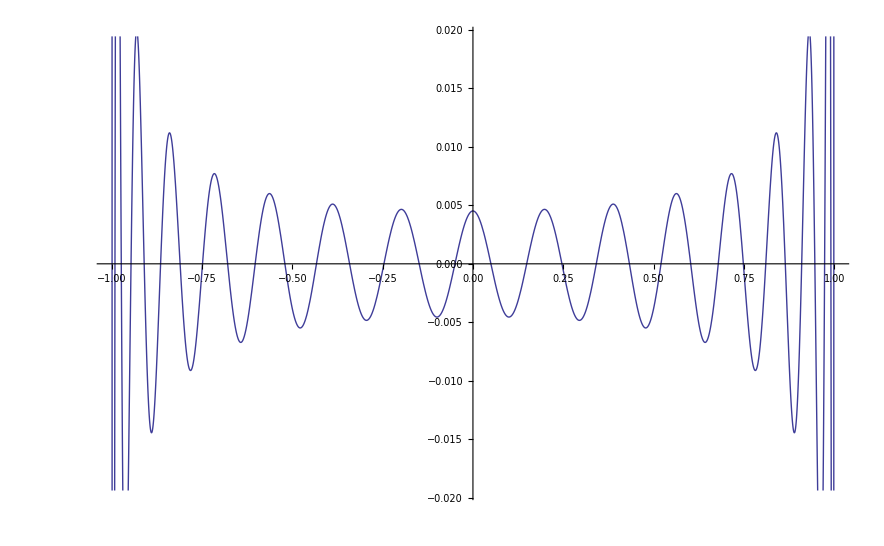

```mathematica
Plot[Evaluate[Subscript[Q, 1](x)-1/2∑_(l=0)^15 (4 l+1)/((2l-1) (l+1)) Subscript[P, 2l](x) ],{x,-1,1}]
```

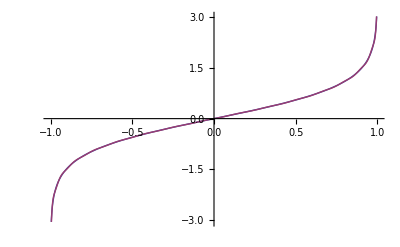

```mathematica
Plot[Evaluate[{Subscript[Q, 0](x),1/2∑_(l=0)^15 (4 l+3)/((2l+1) (l+1)) Subscript[P, 2l+1](x) }],{x,-1,1}]
```

```mathematica
Table[Subscript[pq, l,1],{l,0,11}]
```

{-1,0,1/2,0,1/9,0,1/20,0,1/35,0,1/54,0}

```mathematica
Subscript[pq, ν_,ρ_]:=1/((ν-ρ) (ν+ρ+1))(1-cos((ρ-ν) π)-2/π sin(π ν) cos(π ν) (ψ(ν+1)-ψ(ρ+1)))
```

```mathematica
Subscript[pq, ρ_,ρ_]=lim_(ν->ρ) Subscript[pq, ν,ρ]
```

-(ψ^(1)(ρ+1) sin(2 π ρ))/(2 π ρ+π)

```mathematica
Table[Subscript[pq, ν,ρ],{ρ,0,3},{ν,0,4}]
```

(0 | 1 | 0 | 1/6 | 0
-1 | 0 | 1/2 | 0 | 1/9
0 | -1/2 | 0 | 1/3 | 0
-1/6 | 0 | -1/3 | 0 | 1/4)

```mathematica
lim_(ν->ρ) 1/((ν-ρ) (ν+ρ+1))(1-cos((ρ-ν) π)-2/π sin(π ν) cos(π ν) (ψ(ν+1)-ψ(ρ+1)))
```

-(ψ^(1)(ρ+1) sin(2 π ρ))/(2 π ρ+π)

```mathematica
lim_(ν->ρ) ((-cos((ρ-ν) π)-(2 sin(π ν) cos(π ν) (ψ(ν+1)-ψ(ρ+1)))/π+1) ν)/((ν-ρ) (ν+ρ+1))
```

-(ρ ψ^(1)(ρ+1) sin(2 π ρ))/(2 π ρ+π)

```mathematica
Table[-(ρ ψ^(1)(ρ+1) sin(2 π ρ))/(2 π ρ+π),{ρ,0,3,1/2}]
```

{0,0,0,0,0,0,0}

```mathematica
-1/((n-ν) (n+ν+1)) Subscript[P, n](x)/.{ν->1,n->2}
```

1/4 (1/2-(3 x^2)/2)

```mathematica
(ⅆ((1-x^2) (ⅆ%)/ⅆx))/ⅆx+(ν (ν+1)) %== Subscript[P, n](x)/.{ν->1,n->2}//Simplify
```

True

```mathematica
-1/((n-ν) (n+ν+1)) Subscript[P, n](x)/.{ν->3,n->7}
```

1/44 (-(429 x^7)/16+(693 x^5)/16-(315 x^3)/16+(35 x)/16)

```mathematica
(ⅆ((1-x^2) (ⅆ%)/ⅆx))/ⅆx+(ν (ν+1)) %== Subscript[P, n](x)/.{ν->3,n->7}//Simplify
```

True

```mathematica
∫Subscript[P, 0](x) Subscript[Q, 0](x)ⅆx
```

1/2 (log(x-1)+log(x+1)+x log((x+1)/(1-x)))

```mathematica
∫ Subscript[Q, 0](x)ⅆx//Simplify
```

1/2 (log(x-1)+log(x+1)+x log((x+1)/(1-x)))

```mathematica
Subscript[P, 0](x) Subscript[Q, 0](x)
```

1/2 log((x+1)/(1-x))

```mathematica
(2 l+1)/((l-ν) (l+ν+1))//Apart
```

1/(l+ν+1)-1/(ν-l)

1/(√(1-2x t+t^2))=∑_(l=0)^∞ P_l(x) t^l

```mathematica
t^ν/(√(1-2x t+t^2))=∑_(l=0)^∞ Subscript[P, l](x) t^(l+ν)
```

```mathematica
∫_0^1 t^(l+ν)ⅆt
```

If[Re(l+ν)>-1,1/(l+ν+1),∫_0^1 t^(l+ν)ⅆt]

```mathematica
FullSimplify[∫_0^1 t^ν/(√(1-2x t+t^2))ⅆt,-1<x<1]
```

(F_1(ν+1;1/2,1/2;ν+2;x+√(x^2-1),1/(x+√(x^2-1))))/(ν+1)

```mathematica
∫_0^1 t^(l-1-ν)ⅆt
```

If[Re(l-ν)>0,1/(l-ν),∫_0^1 t^(l-ν-1)ⅆt]

```mathematica
FullSimplify[∫_0^1 t^(-1-ν)/(√(1-2x t+t^2))ⅆt,-1<x<1]
```

(0^-ν-F_1(-ν;1/2,1/2;1-ν;x+√(x^2-1),1/(x+√(x^2-1))))/ν

```mathematica
%%/.x->0
```

(0^-ν-_2 F_1(1/2,-ν/2;1-ν/2;-1))/ν

```mathematica
FunctionExpand[%]
```

(1/2 ⅈ^ν ν Β_-1(-ν/2,1/2)+0^-ν)/ν

## Direct computation of resonant solutions

The solution to the inhomogenous problem is

y(x)=∫_a^x g(t)(y_2(x)y_1(t)-y_1(x) y_2(t))ⅆt.

```mathematica
Simplify[Table[{l, ∫_0^x Subscript[P, l](t)(Subscript[Q, l](x) Subscript[P, l](t)-Subscript[P, l](x) Subscript[Q, l](t))ⅆt+1/(2(2l+1))log(1-x^2)Subscript[P, l](x)},{l,0,7}],-1<x<1]/.log(1-x)->log(1-x^2)-log(x+1)//Simplify
```

(0 | 0
1 | 0
2 | -x^2/5
3 | -x^3/7
4 | 1/6 (x^2-2 x^4)
5 | 1/22 (5 x^3-8 x^5)
6 | 1/312 (-239 x^6+240 x^4-45 x^2)
7 | -1/360 x^3 (359 x^4-420 x^2+105))

```mathematica
-5∑_(l=0)^1 Subscript[a, l] Subscript[P, l](x)/.First[SolveAlways[-x^2/5==∑_(l=0)^2 Subscript[a, l] Subscript[P, l](x),x]]
```

1/3

```mathematica
-7∑_(l=0)^2 Subscript[a, l] Subscript[P, l](x)/.First[SolveAlways[-x^3/7==∑_(l=0)^3 Subscript[a, l] Subscript[P, l](x),x]]
```

(3 x)/5

```mathematica
-9∑_(l=0)^3 Subscript[a, l] Subscript[P, l](x)/.First[SolveAlways[1/6 (x^2-2 x^4)==∑_(l=0)^4 Subscript[a, l] Subscript[P, l](x),x]]//Expand
```

(15 x^2)/14-9/35

```mathematica
-11∑_(l=0)^4 Subscript[a, l] Subscript[P, l](x)/.First[SolveAlways[1/22 (5 x^3-8 x^5)==∑_(l=0)^5 Subscript[a, l] Subscript[P, l](x),x]]//Expand
```

(35 x^3)/18-(20 x)/21

```mathematica
First[SolveAlways[-x^3/7==∑_(l=0)^3 Subscript[a, l] Subscript[P, l](x),x]]
```

{a_0→0,a_2→0,a_1→-3/35,a_3→-2/35}

```mathematica
First[SolveAlways[1/6 (x^2-2 x^4)==∑_(l=0)^4 Subscript[a, l] Subscript[P, l](x),x]]
```

{a_1→0,a_3→0,a_2→-5/63,a_4→-8/105,a_0→-1/90}

```mathematica
-(2 2+1)Simplify[(2 Subscript[P, 2](x))/15-x^2/5]
```

1/3

```mathematica
-(2 3+1)Simplify[3/7(2 Subscript[P, 3](x))/15-x^3/7]
```

(3 x)/5

```mathematica
-(2 4+1)Simplify[4/3 3/7(2 Subscript[P, 4](x))/15+1/6 (x^2-2 x^4)]//Expand
```

(15 x^2)/14-9/35

```mathematica
-(2 5+1)Simplify[20/33 4/3 3/7(2 Subscript[P, 5](x))/15+1/22 (5 x^3-8 x^5)]//Expand
```

(35 x^3)/18-(20 x)/21

```mathematica
-(2 4+1)Simplify[4/3(2 Subscript[P, 4](x))/35+1/6 (x^2-2 x^4)]
```

-3/140 (35 (3 α-4) x^4+(70-90 α) x^2+9 α)

```mathematica
Simplify[Table[ ∫_0^x Subscript[P, l](t)(Subscript[Q, l](x) Subscript[P, l](t)-Subscript[P, l](x) Subscript[Q, l](t))ⅆt+1/(2(2l+1))log(1-x^2)Subscript[P, l](x)+α Subscript[P, l](x) ,{l,0,5}],-1<x<1]/.log(1-x)->log(1-x^2)-log(x+1)//Simplify
```

{α,x α,1/10 (x^2 (15 α-2)-5 α),x^3 ((5 α)/2-1/7)-(3 x α)/2,1/24 ((105 α-8) x^4+(4-90 α) x^2+9 α),1/88 x ((693 α-32) x^4+(20-770 α) x^2+165 α)}

```mathematica
Subscript[W, 3](x)
```

5/24 x (21 x^2-11)

```mathematica
Simplify[Table[{l,∫_0^x Subscript[P, l](t)(Subscript[Q, l](x) Subscript[P, l](t)-Subscript[P, l](x) Subscript[Q, l](t))ⅆt},{l,0,5}],-1<x<1]/.log(1-x)->log(1-x^2)-log(x+1)//FullSimplify
```

(0 | -1/2 log(1-x^2)
1 | -1/6 x log(1-x^2)
2 | 1/20 ((1-3 x^2) log(1-x^2)-4 x^2)
3 | -1/28 x (4 x^2+(5 x^2-3) log(1-x^2))
4 | 1/144 (-48 x^4+24 x^2+(-35 x^4+30 x^2-3) log(1-x^2))
5 | -1/176 x (8 (8 x^2-5) x^2+(63 x^4-70 x^2+15) log(1-x^2)))

```mathematica
FullSimplify[Table[DSolve[Subscript[𝒟, l](Subscript[h, l](x))==Subscript[P, l](x),Subscript[h, l](x),x],{l,0,5}]/.Subscript[c, _]->0/.log(x-1)->log(1-x^2)-log(x+1)]
```

({h_0(x)→-1/2 log(1-x^2)}
{h_1(x)→-1/6 x log(1-x^2)}
{h_2(x)→1/20 ((1-3 x^2) log(1-x^2)-4 x^2)}
{h_3(x)→1/28 (x (3-5 x^2) log(1-x^2)-4 x^3)}
{h_4(x)→1/144 (-48 x^4+24 x^2+(-35 x^4+30 x^2-3) log(1-x^2))}
{h_5(x)→1/176 (8 (5-8 x^2) x^3+(-63 x^4+70 x^2-15) log(1-x^2) x)})

```mathematica
Simplify[Table[ ∫_-1^x Subscript[P, l](t)(Subscript[Q, l](x) Subscript[P, l](t)-Subscript[P, l](x) Subscript[Q, l](t))ⅆt+1/(2(2l+1))log(1-x^2)Subscript[P, l](x),{l,0,1}],-1<x<1]/.log(1-x)->log(1-x^2)-log(x+1)//Simplify
```

{log(x+1)-1/2 log(1-x^2)+log(2),1/6 (2 log(x+1) x-log(1-x^2) x+log(4) x-2 x-2)}

```mathematica
Simplify[Simplify[Table[-(4 l+2) (Subscript[Q, l](x) ∫_a^x Subscript[P, l](t) Subscript[P, l](t)ⅆt-Subscript[P, l](x) ∫_a^x Subscript[Q, l](t) Subscript[P, l](t)ⅆt)-log(1-x^2) Subscript[P, l](x),{l,0,1}],-1<x<1]/.log(1-x)->log(1-x^2)-log(x+1),-1<x<1]
```

{-log(a-1)-log(a+1)-a log(-(a+1)/(a-1))+log(x-1)+log(x+1)+a log((x+1)/(1-x))-log(1-x^2),-x log(-(a+1)/(a-1)) a^3+x log((x+1)/(1-x)) a^3-2 a^3+2 x a^2-x log(a-1)-x log(a+1)+x log(x-1)+x log(x+1)-x log(1-x^2)}

```mathematica
Simplify[Table[-(4l+2)(Subscript[Q, l](x) ∫_0^x Subscript[P, l](t) Subscript[P, l](t)ⅆt-Subscript[P, l](x) ∫_0^x Subscript[Q, l](t) Subscript[P, l](t)ⅆt)-log(1-x^2)Subscript[P, l](x),{l,0,6}],-1<x<1]/.log(1-x)->log(1-x^2)-log(x+1)//Simplify
```

{0,0,2 x^2,2 x^3,6 x^4-3 x^2,x^3 (8 x^2-5),1/12 x^2 (239 x^4-240 x^2+45)}

```mathematica
Simplify[Table[-(2l+1)/x^2((Subscript[Q, l](x) ∫_0^x Subscript[P, l](t) Subscript[P, l](t)ⅆt-Subscript[P, l](x) ∫_0^x Subscript[Q, l](t) Subscript[P, l](t)ⅆt)+1/(4l+2)log(1-x^2)Subscript[P, l](x)),{l,0,6}],-1<x<1]/.log(1-x)->log(1-x^2)-log(x+1)//Simplify
```

{0,0,1,x,3 x^2-3/2,4 x^3-(5 x)/2,(239 x^4)/24-10 x^2+15/8}

```mathematica
Table[Subscript[Q, l](x)∫_0^x Subscript[P, l](t) Subscript[P, l](t)ⅆt,{l,0,3}]
```

```mathematica
Subscript[k, 4](x)//Simplify
```

1/35-(5 x^2)/42

```mathematica
FullSimplify[Table[(4l+2)∫_0^x Subscript[Q, l](t) Subscript[P, l](t)ⅆt,{l,0,2}],-1<x<1]
```

{x log((x+1)/(1-x))+log(1-x^2),log(1-x^2)-x^2 (x log(2/(x+1)-1)+2),log(x-1)+1/4 (2 (-9 x^4+7 x^2-2 ⅈ π)+4 log(x+1)+x (9 x^4-10 x^2+5) log((x+1)/(1-x)))}

```mathematica
Subscript[Q, 0](x)
```

1/2 log((x+1)/(1-x))

```mathematica
Together[2/(x+1)-1]
```

(1-x)/(x+1)

## Reduction of Order

```mathematica
(ⅆ((1-x^2) (ⅆf(x))/ⅆx))/ⅆx==c
```

(1-x^2) f''(x)-2 x f'(x)==c

```mathematica
(1-x^2) f''(x)-2 x f'(x)==D[((1-x^2)f'(x)), x]
```

True

```mathematica
(1-x^2) f''(x)-2 x f'(x)+l (l+1) f(x)-g(x)/.f->Function[x,h(x)Subscript[p, l](x)]
```

-g(x)+l (l+1) h(x) p_l(x)-2 x (p_l(x) h'(x)+h(x) p'_l(x))+(1-x^2) (2 h'(x) p'_l(x)+p_l(x) h''(x)+h(x) p''_l(x))

```mathematica
Collect[%,{h(x),h'(x),h''(x)},Simplify]/.h(x)->0
```

-g(x)+h'(x) (-2 x p_l(x)-2 (x^2-1) p'_l(x))-(x^2-1) p_l(x) h''(x)

```mathematica
Collect[D[((1-x^2)(Subscript[p, l](x))^2 h'(x)), x]/(Subscript[p, l](x))-g(x),{h(x),h'(x),h''(x)},Simplify]
```

-g(x)+h'(x) (-2 x p_l(x)-2 (x^2-1) p'_l(x))-(x^2-1) p_l(x) h''(x)

```mathematica
∫Expand[Subscript[p, l](x) (h'(x) (-2 x Subscript[p, l](x)-2 (x^2-1) Subscript[p, l]'(x))-(x^2-1) Subscript[p, l](x) h''(x))]ⅆx
```

-(x^2-1) (p_l(x))^2 h'(x)

h(x)=c_2+∫^x (c_1+∫^s p_l(t)g(t)ⅆt)/((1-s^2)(p_l(s))^2)ⅆs

h'(x)=(c_1+∫^x p_l(t)g(t)ⅆt)/((1-x^2)(p_l(x))^2)=c_1∂_x ((Q_l(x))/(P_l(x)))+∂_x ((Q_l(x))/(P_l(x)))∫^x p_l(t)g(t)ⅆt

```mathematica
D[((1-x^2)(Subscript[p, l](x))^2 h'(x)), x]=Subscript[p, l](x)g(x)
```

Note that

```mathematica
D[((Subscript[Q, l](x))/(Subscript[P, l](x))), x]-1/((1-x^2) (Subscript[P, l](x))^2)//FullSimplify
```

(-l P_l(x) Q_(l-1)(x)+l P_(l-1)(x) Q_l(x)+1)/((x^2-1) (P_l(x))^2)

```mathematica
FullSimplify/@(Numerator[%]+O[x]^7)
```

O(x^7)

so

h(x)=c_2+∫^x (c_1+∫^s p_l(t)g(t)ⅆt)/((1-s^2)(p_l(s))^2)ⅆs=c_2+∫^x ∂_x ((Q_l(x))/(P_l(x)))(c_1+∫^s p_l(t)g(t)ⅆt)=c_2+c_1(Q_l(x))/(P_l(x))+∫^x ∂_s ((Q_l(s))/(P_l(s)))(∫^s p_l(t)g(t)ⅆt)ⅆs=
c_2+c_1(Q_l(x))/(P_l(x))+[(Q_l(s))/(P_l(s))∫^s p_l(t)g(t)ⅆt]-∫^x Q_l(s)g(s)ⅆs

```mathematica
FullSimplify[(Subscript[Q, 0](x) Subscript[c, 1])/(Subscript[P, 0](x))+(Subscript[Q, 0](x))/(Subscript[P, 0](x))∫ (Subscript[P, 0](x))^2 ⅆx+Subscript[c, 2]-∫Subscript[Q, 0](x) Subscript[P, 0](x)ⅆx,-1<x<1]
```

1/2 (-log(x-1)-log(x+1)+log((x+1)/(1-x)) c_1+2 c_2)

```mathematica
FullSimplify[-∫Subscript[Q, 1](x) Subscript[P, 1](x)ⅆx+(Subscript[Q, 1](x) Subscript[c, 1])/(Subscript[P, 1](x))+(Subscript[Q, 1](x))/(Subscript[P, 1](x))∫ (Subscript[P, 1](x))^2 ⅆx+Subscript[c, 2]/.log((x+1)/(1-x))->log(x+1)-log(x-1),-1<x<1]
```

-(3 (x log(x-1)-x log(x+1)+2) c_1+x (log(x-1)+log(x+1)-6 c_2))/(6 x)

```mathematica
Subscript[c, 2]+∫(Subscript[c, 1]+∫_0^x 1ⅆt)/(1-x^2)ⅆx//Simplify
```

1/2 log(x+1) (c_1-1)-1/2 log(x-1) (c_1+1)+c_2

```mathematica
Simplify[Subscript[P, 0](x)∫(∫_0^x (Subscript[P, 0](t))^2 ⅆt)/((1-x^2) (Subscript[P, 0](x))^2)ⅆx+1/2 Subscript[P, 0](x) log(x^2-1)]
```

0

```mathematica
Simplify[3 Subscript[P, 1](x)∫(∫_0^x (Subscript[P, 1](t))^2 ⅆt)/((1-x^2) (Subscript[P, 1](x))^2)ⅆx+1/2 Subscript[P, 1](x) log(x^2-1)]
```

0

```mathematica
Simplify[5 Subscript[P, 2](x)∫(∫_0^x (Subscript[P, 2](t))^2 ⅆt)/((1-x^2) (Subscript[P, 2](x))^2)ⅆx+1/2 Subscript[P, 2](x) log(x^2-1)+1/3]
```

0

```mathematica
Simplify[7 Subscript[P, 3](x)∫(∫_0^x (Subscript[P, 3](t))^2 ⅆt)/((1-x^2) (Subscript[P, 3](x))^2)ⅆx+1/2 Subscript[P, 3](x) log(x^2-1)+(3x)/5]
```

0

```mathematica
Simplify[9 Subscript[P, 4](x)∫(∫_0^x (Subscript[P, 4](t))^2 ⅆt)/((1-x^2) (Subscript[P, 4](x))^2)ⅆx+1/2 Subscript[P, 4](x) log(x^2-1)+(15 x^2)/14-9/35]
```

0

```mathematica
Simplify[11 Subscript[P, 5](x)∫(∫_0^x (Subscript[P, 5](t))^2 ⅆt)/((1-x^2) (Subscript[P, 5](x))^2)ⅆx+1/2 Subscript[P, 5](x) log(x^2-1)+(35 x^3)/18-(20 x)/21]
```

0

```mathematica
Simplify[13 Subscript[P, 6](x)∫(∫_0^x (Subscript[P, 6](t))^2 ⅆt)/((1-x^2) (Subscript[P, 6](x))^2)ⅆx+1/2 Subscript[P, 6](x)log(x^2-1)+(315 x^4)/88-(175 x^2)/66+1195/5544]
```

0

```mathematica
Simplify[15 Subscript[P, 7](x)∫(∫_0^x (Subscript[P, 7](t))^2 ⅆt)/((1-x^2) (Subscript[P, 7](x))^2)ⅆx+1/2 Subscript[P, 7](x)log(x^2-1)+(693 x^5)/104-(945 x^3)/143+(12565 x)/10296]
```

0

```mathematica
Collect[∫1/((1-x^2) (Subscript[P, 2](x))^2)ⅆx-(Subscript[Q, 2](x))/(Subscript[P, 2](x))/.log((x+1)/(1-x))->log(x+1)-log(x-1),{log(_)},FullSimplify]
```

0

```mathematica
Collect[∫1/((1-x^2) (Subscript[P, 3](x))^2)ⅆx-(Subscript[Q, 3](x))/(Subscript[P, 3](x))/.log((x+1)/(1-x))->log(x+1)-log(x-1),{log(_)},FullSimplify]
```

0

```mathematica
(Subscript[Q, 2](x))/(Subscript[P, 2](x))//FullSimplify
```

1/2 ((6 x)/(1-3 x^2)+log(1/(1-x))+log(x+1))

```mathematica
Simplify[∫(∫_0^x (Subscript[P, 3](t))^2 ⅆt)/((1-x^2) (Subscript[P, 3](x))^2)ⅆx]
```

-1/14 log(x^2-1)-6/(35 (5 x^2-3))

```mathematica
Simplify[∫(∫_0^x (Subscript[P, 4](t))^2 ⅆt)/((1-x^2) (Subscript[P, 4](x))^2)ⅆx]
```

-(4 (25 x^2-6))/(105 (35 x^4-30 x^2+3))-1/18 log(x^2-1)

```mathematica
Simplify[∫1/((1-x^2) (Subscript[P, 4](x))^2)ⅆx]
```

1/6 ((110 x-210 x^3)/(35 x^4-30 x^2+3)-3 log(x-1)+3 log(x+1))

```mathematica
Table[DSolve[(l+1) l f(x)-2 x f'(x)+(1-x^2) f''(x)==Subscript[P, l](x),f(x),x],{l,0,2}]
```

({f(x)→c_2+1/2 (c_1-1) log(x-1)+1/2 (-c_1-1) log(x+1)}
{f(x)→x c_1+1/6 (-x log(x-1)-x log(x+1))+c_2 (1/2 x log((x+1)/(1-x))-1)}
{f(x)→((3 x^2)/2-1/2) c_1+1/20 (-3 log(x-1) x^2-3 log(x+1) x^2-4 x^2+log(x-1)+log(x+1))+c_2 (1/4 (3 x^2-1) log((x+1)/(1-x))-(3 x)/2)})

```mathematica
(l+1) l f(x)-2 x f'(x)+(1-x^2) f''(x)-Subscript[P, l](x)/.f->Function[-1/10 log(1-x^2)Subscript[P, l](x)]/.l->2
```

-(3 x^2)/2-3/5 ((3 x^2)/2-1/2) log(1-x^2)+1/2

```mathematica
DSolve[%,f(x),x]
```

```mathematica
D[((1-x^2)f'(x)), x]==c
```

```mathematica
(1-x^2)f'(x)==c x+d
```

```mathematica
f'(x)==(c x+d)/(1-x^2)
```

```mathematica
∫(c x+d)/(1-x^2)ⅆx
```

1/2 (-c-d) log(x-1)+1/2 (d-c) log(x+1)

```mathematica
%/.d->0//Simplify
```

-1/2 c (log(x-1)+log(x+1))

## Second Kind Resonant Solutions

```mathematica
Simplify[Table[{l,∫_0^x Subscript[Q, l](t) (Subscript[Q, l](x) Subscript[P, l](t)-Subscript[P, l](x) Subscript[Q, l](t))ⅆt},{l,0,2}],-1<x<1]
```

(0 | 1/4 (log(4) (log(x+1)-log(1-x))+2 Li_2((1-x)/2)-2 Li_2((x+1)/2))
1 | 1/12 (4 x log(1-x)-x log(4) log(1-x)-2 log(1-x)-4 x log(x+1)+x log(4) log(x+1)-2 log(x+1)+2 x Li_2((1-x)/2)-2 x Li_2((x+1)/2))
2 | 1/80 (-log(4096) log(1-x) x^2+20 log(1-x) x^2+log(4096) log(x+1) x^2-20 log(x+1) x^2-12 log(1-x) x-12 log(x+1) x-8 x+log(16) log(1-x)-4 log(1-x)-log(16) log(x+1)+4 log(x+1)+4 (3 x^2-1) Li_2((1-x)/2)+(4-12 x^2) Li_2((x+1)/2)))

```mathematica
FullSimplify[Simplify[1/3 Subscript[Q, 2](x)+%⟦3,2⟧,-1<x<1]/.log((x+1)/(1-x))->log(x+1)-log(1-x)]
```

```mathematica
Simplify[1/4 (log(4) (log(x+1)-log(1-x))+2 Subscript[Li, 2]((1-x)/2)-2 Subscript[Li, 2]((x+1)/2))-1/2 log(4)Subscript[Q, 0](x),-1<x<1]
```

1/2 (Li_2((1-x)/2)-Li_2((x+1)/2))

```mathematica
%+O[x]^5//Simplify
```

-log(2) x+1/6 (1-log(4)) x^3+O(x^5)

```mathematica
∫_-1^1 %% Subscript[P, 0](x)ⅆx
```

0

```mathematica
Plot[%%%,{x,-1,1}]
```

```mathematica
Simplify[1/12 (4 x log(1-x)-x log(4) log(1-x)-2 log(1-x)-4 x log(x+1)+x log(4) log(x+1)-2 log(x+1)+2 x Subscript[Li, 2]((1-x)/2)-2 x Subscript[Li, 2]((x+1)/2))-1/6 log(4)Subscript[Q, 1](x)+4/3(Subscript[Q, 1](x))/2,-1<x<1]
```

1/12 (-2 log(1-x)-2 log(x+1)+2 x Li_2((1-x)/2)-2 x Li_2((x+1)/2)+log(16)-8)

```mathematica
%+O[x]^3
```

1/12 (-8+log(16))+1/12 (2-4 log(2)) x^2+O(x^3)

```mathematica
∫_-1^1 %% Subscript[P, 1](x)ⅆx
```

0

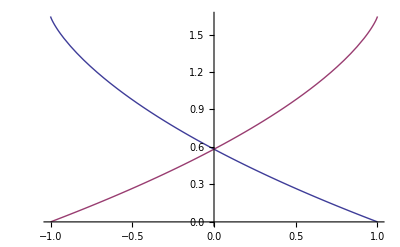

```mathematica
Plot[{Subscript[Li, 2]((1-x)/2),Subscript[Li, 2]((x+1)/2)},{x,-1,1}]
```

```mathematica
Simplify[Subscript[𝒟, 0](1/4 (-2 Subscript[Li, 2]((x+1)/2)+2 Subscript[Li, 2]((1-x)/2)))-Subscript[Q, 0](x),-1<x<1]
```

0

```mathematica
Simplify[Subscript[𝒟, 1](1/12 (-2 log(1-x)-2 log(x+1)+2 x Subscript[Li, 2]((1-x)/2)-2 x Subscript[Li, 2]((x+1)/2)+log(16)-8))-Subscript[Q, 1](x),-1<x<1]
```

0

```mathematica
Simplify[Subscript[𝒟, 2](1/60 (-36 x+(-9 x (log(2) x+1)+log(8)+2) log(1-x)+(9 x (x log(2)-1)-log(8)-2) log(x+1)+(9 x^2-3) Subscript[Li, 2]((1-x)/2)+3 (1-3 x^2) Subscript[Li, 2]((x+1)/2)))-Subscript[Q, 2](x),-1<x<1]
```

0

```mathematica
Simplify[Table[DSolve[Subscript[𝒟, l](Subscript[h, l](x))==Subscript[Q, l](x),Subscript[h, l](x),x],{l,0,0}],-1<x<1]/.Subscript[c, _]->0
```

({h_0(x)→1/4 (-log^2(x-1)+(log((1-x)/(x+1))+2 log(x+1)-log(16)) log(x-1)+log(1-x) log(x+1)+4 Li_2((1-x)/2))})

```mathematica
FullSimplify[Subscript[Li, 2]((x+1)/2)/.Subscript[Li, 2](z_)->-log(1-z) log(z)+π^2/6-Subscript[Li, 2](1-z),-1<x<1]//Expand
```

-log((1-x)/2) log((x+1)/2)-Li_2((1-x)/2)+π^2/6

```mathematica
FullSimplify[Subscript[𝒟, 0](1/4 ((2 log(x+1)-log(16)) log(1-x)+4 Subscript[Li, 2]((1-x)/2)))-Subscript[Q, 0](x),-1<x<1]
```

0

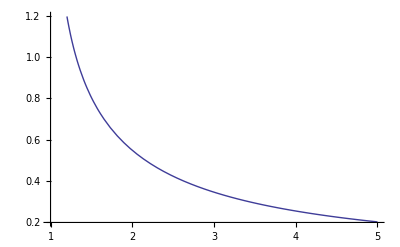

```mathematica
Plot[Subscript[Q, 0]^0(x),{x,1,5}]
```

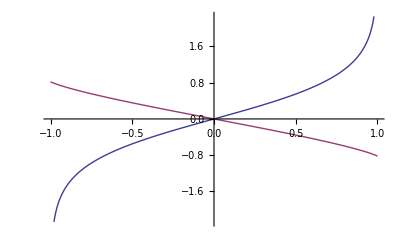

```mathematica
Plot[{Subscript[Q, 0](x),1/2 (Subscript[Li, 2]((1-x)/2)-Subscript[Li, 2]((x+1)/2))},{x,-1,1}]
```

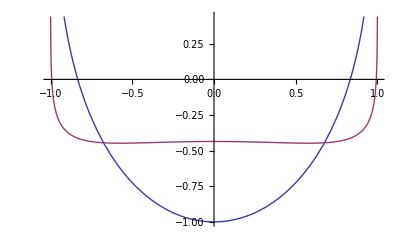

```mathematica
Plot[{Subscript[Q, 1](x),1/6 (Subscript[Li, 2]((1-x)/2)-Subscript[Li, 2]((x+1)/2)) Subscript[P, 1](x)-1/6 ln(1-x^2)+(ln(2)-2)/3},{x,-1,1}]
```

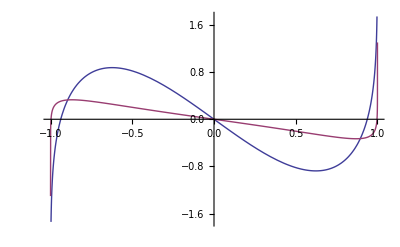

```mathematica
Plot[{Subscript[Q, 2](x),3/10 (log(2)-2) Subscript[P, 1](x)-3/20 log(1-x^2) x-(Subscript[Q, 0](x))/15+1/10 Subscript[P, 2](x) (Subscript[Li, 2]((1-x)/2)-Subscript[Li, 2]((x+1)/2))},{x,-1,1}]
```

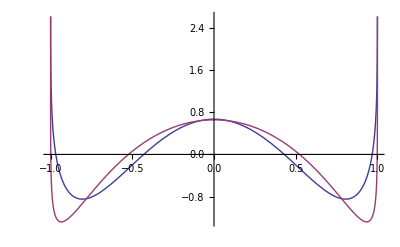

```mathematica
Plot[{Subscript[Q, 3](x),5(5/21 (-2+log(2)) ((3 x^2)/2-1/2)-3/35 (1/2 x log((x+1)/(1-x))-1)+(1/21-(5 x^2)/28) log(1-x^2)+1/14 ((5 x^3)/2-(3 x)/2) (Subscript[Li, 2]((1-x)/2)-Subscript[Li, 2]((x+1)/2))+(log(2))/42-8/63)},{x,-1,1}]
```

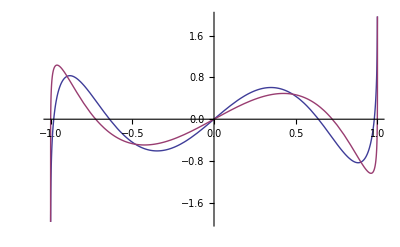

```mathematica
Plot[{Subscript[Q, 4](x),5 (1/324 (-59+log(4096)) x-1/180 log((x+1)/(1-x))-5/63 (1/4 (3 x^2-1) log((x+1)/(1-x))-(3 x)/2)+((55 x)/432-(35 x^3)/144) log(1-x^2)+1/18 ((35 x^4)/8-(15 x^2)/4+3/8) (Subscript[Li, 2]((1-x)/2)-Subscript[Li, 2]((x+1)/2))+7/36 ((5 x^3)/2-(3 x)/2) (-2+log(2)))},{x,-1,1}]
```

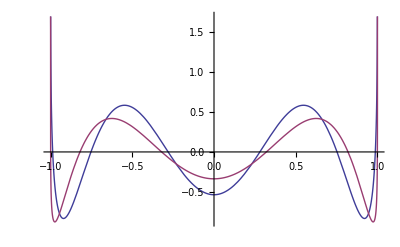

```mathematica
Plot[{Subscript[Q, 5](x),5 (1/132 (-24+log(32)) ((3 x^2)/2-1/2)-3/154 (1/2 x log((x+1)/(1-x))-1)-7/99 (-(5 x^2)/2-3/4 (1-(5 x^2)/3) log((x+1)/(1-x)) x+2/3)+(-(63 x^4)/176+(49 x^2)/176-4/165) log(1-x^2)+1/22 ((63 x^5)/8-(35 x^3)/4+(15 x)/8) (Subscript[Li, 2]((1-x)/2)-Subscript[Li, 2]((x+1)/2))+(log(2))/165+9/55 ((35 x^4)/8-(15 x^2)/4+3/8) (-2+log(2))-37/900)},{x,-1,1}]
```

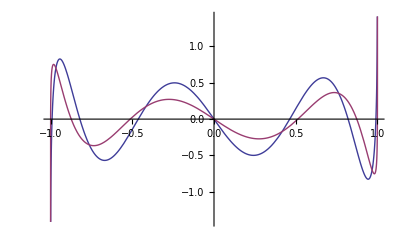

```mathematica
Plot[{Subscript[Q, 6](x),5 (-(231 x^5)/104+(994 x^3)/429+(3 log(32) x)/1300-(3563 x)/7800+(-(315 x^4)/2288+(175 x^2)/1716-1195/144144) log((x+1)/(1-x))+(-(231 x^5)/416+(119 x^3)/208-(231 x)/2080) log(1-x^2)+((231 x^6)/416-(315 x^4)/416+(105 x^2)/416-5/416) Subscript[Li, 2]((1-x)/2)+(-(231 x^6)/416+(315 x^4)/416-(105 x^2)/416+5/416) Subscript[Li, 2]((x+1)/2)+((7 x^3)/312-(7 x)/520) log(16)+((231 x^5)/208-(385 x^3)/312+(55 x)/208) log(2))},{x,-1,1}]
```

```mathematica
Simplify[Subscript[𝒟, 0](1/2 (Subscript[Li, 2]((1-x)/2)-Subscript[Li, 2]((x+1)/2)) Subscript[P, 0](x))-Subscript[Q, 0](x),-1<x<1]
```

0

```mathematica
FullSimplify[Subscript[𝒟, 1](1/6 (Subscript[Li, 2]((1-x)/2)-Subscript[Li, 2]((x+1)/2)) Subscript[P, 1](x)-1/6 ln(1-x^2)+(ln(2)-2)/3)-Subscript[Q, 1](x),-1<x<1]
```

0

```mathematica
Collect[Simplify[Subscript[𝒟, 2](1/10 Subscript[P, 2](x) (Subscript[Li, 2]((1-x)/2)-Subscript[Li, 2]((x+1)/2))+3/10 (ln(2)-2) Subscript[P, 1](x)-3/20  log(1-x^2) x-1/15 Subscript[Q, 0](x))-Subscript[Q, 2](x),-1<x<1]/.log(1-x^2)->log(x+1)+log(1-x),{log(_),x},Simplify]
```

0

```mathematica
Collect[PowerExpand[Simplify[Subscript[𝒟, 3](1/14 Subscript[P, 3](x) (Subscript[Li, 2]((1-x)/2)-Subscript[Li, 2]((x+1)/2))+log(1-x^2) ∑_(i=0)^1 Subscript[c, i] x^(2 i)+∑_(i=0)^1 Subscript[a, i] Subscript[P, 2 i](x)+∑_(i=0)^0 Subscript[b, i] Subscript[Q, 2 i+1](x))-Subscript[Q, 3](x),-1<x<1]/.log(1-x^2)->log(x+1)+log(1-x)],{log(1-x),log(x+1)},Collect[#1,x,Simplify]&]
```

(9 a_1-5/14 (28 c_1+log(64)-7)) x^2+12 a_0-3 a_1-10 b_0-2 c_0+log(1-x) ((6 c_1+15/14) x^2+(-5 b_0-3/7) x+12 c_0+2 c_1-3/14)+log(x+1) ((6 c_1+15/14) x^2+(5 b_0+3/7) x+12 c_0+2 c_1-3/14)+(3 log(2))/7-2/3

```mathematica
SolveAlways[%==0,{log(1-x),log(x+1),x}]//FullSimplify
```

{{b_0→-3/35,a_0→-8/63+(log(2))/42,a_1→5/21 (-2+log(2)),c_0→1/21,c_1→-5/28}}

```mathematica
1/14 Subscript[P, 3](x) (Subscript[Li, 2]((1-x)/2)-Subscript[Li, 2]((x+1)/2))+log(1-x^2) ∑_(i=0)^1 Subscript[c, i] x^(2 i)+∑_(i=0)^1 Subscript[a, i] Subscript[P, 2 i](x)+∑_(i=0)^0 Subscript[b, i] Subscript[Q, 2 i+1](x)/.First[%]
```

5/21 (-2+log(2)) ((3 x^2)/2-1/2)-3/35 (1/2 x log((x+1)/(1-x))-1)+(1/21-(5 x^2)/28) log(1-x^2)+1/14 ((5 x^3)/2-(3 x)/2) (Li_2((1-x)/2)-Li_2((x+1)/2))+(log(2))/42-8/63

```mathematica
FullSimplify[Subscript[𝒟, 3](%)-Subscript[Q, 3](x),-1<x<1]
```

0

```mathematica
Collect[PowerExpand[Simplify[Subscript[𝒟, 4](1/18 Subscript[P, 4](x) (Subscript[Li, 2]((1-x)/2)-Subscript[Li, 2]((x+1)/2))+log(1-x^2) ∑_(i=0)^1 Subscript[c, i] x^(2 i+1)+∑_(i=0)^1 Subscript[a, i] Subscript[P, 2 i+1](x)+∑_(i=0)^1 Subscript[b, i] Subscript[Q, 2 i](x))-Subscript[Q, 4](x),-1<x<1]/.log(1-x^2)->log(x+1)+log(1-x)],{log(1-x),log(x+1)},Collect[#1,x,Simplify]&]
```

(20 a_1-14 c_1-log(8)-(8 log(2))/9+35/8) x^3+(18 a_0-12 a_1-21 b_1-6 c_0+(5 log(2))/3-55/24) x+log(1-x) ((8 c_1+35/18) x^3+1/6 (-63 b_1-5) x^2+(18 c_0+6 c_1-5/6) x-10 b_0+(7 b_1)/2+1/6)+log(x+1) ((8 c_1+35/18) x^3+1/6 (63 b_1+5) x^2+(18 c_0+6 c_1-5/6) x+10 b_0-(7 b_1)/2-1/6)

```mathematica
SolveAlways[%==0,{log(1-x),log(x+1),x}]//FullSimplify
```

{{b_0→-1/90,b_1→-5/63,a_0→1/324 (-59+log(4096)),a_1→7/36 (-2+log(2)),c_0→55/432,c_1→-35/144}}

```mathematica
1/18 Subscript[P, 4](x) (Subscript[Li, 2]((1-x)/2)-Subscript[Li, 2]((x+1)/2))+log(1-x^2) ∑_(i=0)^1 Subscript[c, i] x^(2 i+1)+∑_(i=0)^1 Subscript[a, i] Subscript[P, 2 i+1](x)+∑_(i=0)^1 Subscript[b, i] Subscript[Q, 2 i](x)/.First[%]
```

1/324 (-59+log(4096)) x-1/180 log((x+1)/(1-x))-5/63 (1/4 (3 x^2-1) log((x+1)/(1-x))-(3 x)/2)+((55 x)/432-(35 x^3)/144) log(1-x^2)+1/18 ((35 x^4)/8-(15 x^2)/4+3/8) (Li_2((1-x)/2)-Li_2((x+1)/2))+7/36 ((5 x^3)/2-(3 x)/2) (-2+log(2))

```mathematica
FullSimplify[Subscript[𝒟, 4](%)-Subscript[Q, 4](x),-1<x<1]
```

0

```mathematica
Collect[PowerExpand[Simplify[Subscript[𝒟, 5](1/22 Subscript[P, 5](x) (Subscript[Li, 2]((1-x)/2)-Subscript[Li, 2]((x+1)/2))+log(1-x^2) ∑_(i=0)^2 Subscript[c, i] x^(2 i)+∑_(i=0)^2 Subscript[a, i] Subscript[P, 2 i](x)+∑_(i=0)^1 Subscript[b, i] Subscript[Q, 2 i+1](x))-Subscript[Q, 5](x),-1<x<1]/.log(1-x^2)->log(x+1)+log(1-x)],{log(1-x),log(x+1)},Collect[#1,x,Simplify]&]
```

((175 a_2)/4-18 c_2-(315 log(2))/44+63/8) x^4+(36 a_1-(75 a_2)/2-45 b_1-10 c_1+(105 log(2))/22-49/8) x^2+30 a_0-12 a_1+(15 a_2)/4-28 b_0+12 b_1-2 c_0+log(x+1) ((10 c_2+315/88) x^4+5/22 (99 b_1+7) x^3+(24 c_1+12 c_2-105/44) x^2+(14 b_0-3/22 (99 b_1+5)) x+30 c_0+2 c_1+15/88)+log(1-x) ((10 c_2+315/88) x^4-5/22 (99 b_1+7) x^3+(24 c_1+12 c_2-105/44) x^2+(3/22 (99 b_1+5)-14 b_0) x+30 c_0+2 c_1+15/88)-(15 log(2))/44+8/15

```mathematica
SolveAlways[%==0,{log(1-x),log(x+1),x}]//FullSimplify
```

{{b_0→-3/154,b_1→-7/99,a_0→-37/900+(log(2))/165,a_1→1/132 (-24+log(32)),a_2→9/55 (-2+log(2)),c_0→-4/165,c_1→49/176,c_2→-63/176}}

```mathematica
1/22 Subscript[P, 5](x) (Subscript[Li, 2]((1-x)/2)-Subscript[Li, 2]((x+1)/2))+log(1-x^2) ∑_(i=0)^2 Subscript[c, i] x^(2 i)+∑_(i=0)^2 Subscript[a, i] Subscript[P, 2 i](x)+∑_(i=0)^1 Subscript[b, i] Subscript[Q, 2 i+1](x)/.First[%]
```

1/132 (-24+log(32)) ((3 x^2)/2-1/2)-3/154 (1/2 x log((x+1)/(1-x))-1)-7/99 (-(5 x^2)/2-3/4 (1-(5 x^2)/3) log((x+1)/(1-x)) x+2/3)+(-(63 x^4)/176+(49 x^2)/176-4/165) log(1-x^2)+1/22 ((63 x^5)/8-(35 x^3)/4+(15 x)/8) (Li_2((1-x)/2)-Li_2((x+1)/2))+(log(2))/165+9/55 ((35 x^4)/8-(15 x^2)/4+3/8) (-2+log(2))-37/900

```mathematica
Collect[%,{Subscript[Li, 2](_),log(_),x},Simplify]
```

-(63 x^4)/44+(112 x^2)/99+((10 x)/231-(35 x^3)/396) log((x+1)/(1-x))+(-(63 x^4)/176+(49 x^2)/176-4/165) log(1-x^2)+((63 x^5)/176-(35 x^3)/88+(15 x)/176) Li_2((1-x)/2)+(-(63 x^5)/176+(35 x^3)/88-(15 x)/176) Li_2((x+1)/2)+(x^2/88-1/264) log(32)+((63 x^4)/88-(27 x^2)/44+89/1320) log(2)-5228/51975

```mathematica
FullSimplify[Subscript[𝒟, 5](%)-Subscript[Q, 5](x),-1<x<1]
```

0

```mathematica
Collect[PowerExpand[Simplify[Subscript[𝒟, 6](1/26 Subscript[P, 6](x) (Subscript[Li, 2]((1-x)/2)-Subscript[Li, 2]((x+1)/2))+log(1-x^2) ∑_(i=0)^2 Subscript[c, i] x^(2 i+1)+∑_(i=0)^2 Subscript[a, i] Subscript[P, 2 i+1](x)+∑_(i=0)^2 Subscript[b, i] Subscript[Q, 2 i](x))-Subscript[Q, 6](x),-1<x<1]/.log(1-x^2)->log(x+1)+log(1-x)],{log(1-x),log(x+1)},Collect[#1,x,Simplify]&]
```

((189 a_2)/2-22 c_2-(693 log(2))/52+231/16) x^5+(75 a_1-105 a_2-(385 b_2)/4-14 c_1+(315 log(2))/26-119/8) x^3+(40 a_0-45 a_1+(45 a_2)/2-54 b_1+(605 b_2)/12-6 c_0-(105 log(2))/52+231/80) x+log(x+1) ((12 c_2+693/104) x^5+35/104 (143 b_2+9) x^4+(30 c_1+20 c_2-315/52) x^3+3/52 (468 b_1-715 b_2-35) x^2+(40 c_0+6 c_1+105/104) x+21 b_0-9 b_1+(33 b_2)/8+15/104)+log(1-x) ((12 c_2+693/104) x^5-35/104 (143 b_2+9) x^4+(30 c_1+20 c_2-315/52) x^3+(15/52 (143 b_2+7)-27 b_1) x^2+(40 c_0+6 c_1+105/104) x-21 b_0+9 b_1-3/104 (143 b_2+5))

```mathematica
SolveAlways[%==0,{log(1-x),log(x+1),x}]//FullSimplify
```

{{b_1→-5/234,b_2→-9/143,b_0→-1/273,a_0→(3 (-31+log(32)))/1300,a_1→7/780 (-19+log(16)),a_2→11/78 (-2+log(2)),c_0→-231/2080,c_1→119/208,c_2→-231/416}}

```mathematica
1/26 Subscript[P, 6](x) (Subscript[Li, 2]((1-x)/2)-Subscript[Li, 2]((x+1)/2))+log(1-x^2) ∑_(i=0)^2 Subscript[c, i] x^(2 i+1)+∑_(i=0)^2 Subscript[a, i] Subscript[P, 2 i+1](x)+∑_(i=0)^2 Subscript[b, i] Subscript[Q, 2 i](x)/.First[%]
```

(3 (-31+log(32)) x)/1300-1/546 log((x+1)/(1-x))-5/234 (1/4 (3 x^2-1) log((x+1)/(1-x))-(3 x)/2)-9/143 (-(35 x^3)/8+(55 x)/24+3/16 ((35 x^4)/3-10 x^2+1) log((x+1)/(1-x)))+(-(231 x^5)/416+(119 x^3)/208-(231 x)/2080) log(1-x^2)+1/26 ((231 x^6)/16-(315 x^4)/16+(105 x^2)/16-5/16) (Li_2((1-x)/2)-Li_2((x+1)/2))+7/780 ((5 x^3)/2-(3 x)/2) (-19+log(16))+11/78 ((63 x^5)/8-(35 x^3)/4+(15 x)/8) (-2+log(2))

```mathematica
Collect[%,{Subscript[Li, 2](_),log(_),x},Simplify]
```

-(231 x^5)/104+(994 x^3)/429+(3 log(32) x)/1300-(3563 x)/7800+(-(315 x^4)/2288+(175 x^2)/1716-1195/144144) log((x+1)/(1-x))+(-(231 x^5)/416+(119 x^3)/208-(231 x)/2080) log(1-x^2)+((231 x^6)/416-(315 x^4)/416+(105 x^2)/416-5/416) Li_2((1-x)/2)+(-(231 x^6)/416+(315 x^4)/416-(105 x^2)/416+5/416) Li_2((x+1)/2)+((7 x^3)/312-(7 x)/520) log(16)+((231 x^5)/208-(385 x^3)/312+(55 x)/208) log(2)

```mathematica
FullSimplify[Subscript[𝒟, 6](%)-Subscript[Q, 6](x),-1<x<1]
```

0

### General result?

```mathematica
Subscript[𝒟, l](Subscript[q, n](x))-Subscript[𝒟, n](Subscript[q, n](x))//Factor
```

(l-n) (l+n+1) q_n(x)

```mathematica
Simplify/@Collect[Subscript[𝒟, l](Subscript[p, l](x) (Subscript[Li, 2]((1-x)/2)-Subscript[Li, 2]((x+1)/2))),Subscript[Li, 2](_),Factor]/.Simplify[Subscript[𝒟, l](Subscript[p, l](x))]->0
```

-log((1-x)/2) p_l(x)+log((x+1)/2) p_l(x)-2 x log((1-x)/2) p'_l(x)+2 log((1-x)/2) p'_l(x)+2 x log((x+1)/2) p'_l(x)+2 log((x+1)/2) p'_l(x)

```mathematica
Collect[%,{Subscript[p, l](x),Subscript[p, l]^(n_)(x)},FullSimplify[#,-1<x<1]&]
```

log((x+1)/(1-x)) p_l(x)+2 (x log((x+1)/(1-x))+log(1/4 (1-x^2))) p'_l(x)

x (∂P_l(x))/(∂x)=l P_l(x)+∑_(n=If[OddQ[l],1,0]
Δ n=2)^(l-1) (2 n+1) P_n(x)

```mathematica
Subscript[n, l_]:=If[OddQ[l],1,0]
```

```mathematica
Table[-x (∂Subscript[P, l](x))/(∂x)+l Subscript[P, l](x)+∑_{{n=Subscript[n, l]}, {Δ n=2}}^(l-2) (2 n+1) Subscript[P, n](x)//Expand,{l,0,10}]
```

{0,0,0,0,0,0,0,0,0,0,0}

𝒟_l(P_l(x) (Li_2((1-x)/2)-Li_2((x+1)/2)))=2 Q_l(x)+2W_(l-1)(x)+2 (x log((x+1)/(1-x))+log(1/4 (1-x^2))) P'_l(x)
=2 (2l+1) Q_l(x)+2(2l+1)W_(l-1)(x)+2 log((x+1)/(1-x))(∑')_(n=0)^(l-1)(2n+1) P_n(x)+2log(1/4 (1-x^2))P'_l(x)
=2 (2l+1) Q_l(x)+2(2l+1)W_(l-1)(x)+4 (∑')_(n=0)^(l-1)(2n+1) Q_n(x)+4(∑')_(n=0)^(l-1)(2n+1) W_(n-1)(x)+2log(1/4 (1-x^2))P'_l(x)

```mathematica
FullSimplify[Table[Subscript[𝒟, l](1/(2 (2 l+1))Subscript[P, l](x) (Subscript[Li, 2]((1-x)/2)-Subscript[Li, 2]((x+1)/2)))-( Subscript[Q, l](x)+ Subscript[W, l-1](x)+1/(2 l+1) (∂Subscript[P, l](x))/(∂x) log(1/4 (1-x^2))+2/(2l+1) ∑_{{n=Subscript[n, l]}, {Δ n=2}}^(l-2) (2 n+1) Subscript[Q, n](x)+2/(2l+1) ∑_{{n=Subscript[n, l]}, {Δ n=2}}^(l-2) (2 n+1) Subscript[W, n-1](x)),{l,0,12}],-1<x<1]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
FullSimplify[Table[Subscript[𝒟, l](1/(2 (2 l+1))Subscript[P, l](x) (Subscript[Li, 2]((1-x)/2)-Subscript[Li, 2]((x+1)/2))+1/2 log(1/4(1-x^2))Subscript[κ, l](x))-( Subscript[Q, l](x)+ Subscript[W, l-1](x)-Subscript[κ, l](x)-2 x (∂Subscript[κ, l](x))/(∂x)+2/(2l+1) ∑_{{n=Subscript[n, l]}, {Δ n=2}}^(l-2) (2 n+1) Subscript[Q, n](x)+2/(2l+1) ∑_{{n=Subscript[n, l]}, {Δ n=2}}^(l-2) (2 n+1) Subscript[W, n-1](x)),{l,0,12}],-1<x<1]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
FullSimplify[Table[Subscript[𝒟, l](1/(2 (2 l+1))Subscript[P, l](x) (Subscript[Li, 2]((1-x)/2)-Subscript[Li, 2]((x+1)/2))+1/2 log(1/4(1-x^2))Subscript[κ, l](x)-2/(2l+1)∑_{{n=Subscript[n, l]}, {Δ n=2}}^(l-2) (2 n+1)/((l-n)(l+n+1)) Subscript[Q, n](x))-( Subscript[Q, l](x)+ Subscript[W, l-1](x)-Subscript[κ, l](x)-2 x (∂Subscript[κ, l](x))/(∂x)+2/(2l+1) ∑_{{n=Subscript[n, l]}, {Δ n=2}}^(l-2) (2 n+1) Subscript[W, n-1](x)),{l,0,10}],-1<x<1]
```

{0,0,0,0,0,0,0,0,0,0,0}

```mathematica
FullSimplify[Table[Subscript[𝒟, l](1/(2 (2 l+1))Subscript[P, l](x) (Subscript[Li, 2]((1-x)/2)-Subscript[Li, 2]((x+1)/2))+1/2 log(1/4(1-x^2))Subscript[κ, l](x)-2/(2l+1)∑_{{n=Subscript[n, l]}, {Δ n=2}}^(l-2) (2 n+1)/((l-n)(l+n+1)) Subscript[Q, n](x)-∑_(n=0)^(l-1) Subscript[a, n,l]/((l-n)(l+n+1)) Subscript[P, n](x))-( Subscript[Q, l](x)),{l,0,10}],-1<x<1]
```

{0,0,0,0,0,0,0,0,0,0,0}

```mathematica
FullSimplify[Table[Subscript[𝒟, l](1/(2 (2 l+1))Subscript[P, l](x) (Subscript[Li, 2]((1-x)/2)-Subscript[Li, 2]((x+1)/2))+1/2 log(1/4(1-x^2))Subscript[κ, l](x)-2/(2l+1)∑_{{n=Subscript[n, l]}, {Δ n=2}}^(l-2) (2 n+1)/((l-n)(l+n+1)) Subscript[Q, n](x)-∑_{{n=1-Subscript[n, l]}, {Δ n=2}}^(l-1) Subscript[a, n,l]/((l-n)(l+n+1)) Subscript[P, n](x))-( Subscript[Q, l](x)),{l,0,10}],-1<x<1]
```

{0,0,0,0,0,0,0,0,0,0,0}

```mathematica
FullSimplify[Table[Subscript[𝒟, l](1/(2 (2 l+1))Subscript[P, l](x) (Subscript[Li, 2]((1-x)/2)-Subscript[Li, 2]((x+1)/2))+1/2 log(1/4(1-x^2))Subscript[κ, l](x)-2/(2l+1)∑_{{n=Subscript[n, l]}, {Δ n=2}}^(l-2) (2 n+1)/((l-n)(l+n+1)) Subscript[Q, n](x)-∑_{{n=1-Subscript[n, l]}, {Δ n=2}}^(l-1) Subscript[δ, n,l] Subscript[P, n](x))-( Subscript[Q, l](x)),{l,0,10}],-1<x<1]
```

{0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[1/(2 (2 l+1))Subscript[P, l](x) (Subscript[Li, 2]((1-x)/2)-Subscript[Li, 2]((x+1)/2))+1/2 log(1/4(1-x^2))Subscript[κ, l](x)-2/(2l+1)∑_{{n=Subscript[n, l]}, {Δ n=2}}^(l-2) (2 n+1)/((l-n)(l+n+1)) Subscript[Q, n](x)-∑_{{n=1-Subscript[n, l]}, {Δ n=2}}^(l-1) Subscript[δ, n,l] Subscript[P, n](x),{l,0,3}]
```

{1/2 (Li_2((1-x)/2)-Li_2((x+1)/2)),-1/6 log(1/4 (1-x^2))+1/6 x (Li_2((1-x)/2)-Li_2((x+1)/2))-2/3,-3/20 log(1/4 (1-x^2)) x-(3 x)/5-1/30 log((x+1)/(1-x))+1/10 ((3 x^2)/2-1/2) (Li_2((1-x)/2)-Li_2((x+1)/2)),-10/21 ((3 x^2)/2-1/2)-3/35 (1/2 x log((x+1)/(1-x))-1)+1/7 (-5/6 ((3 x^2)/2-1/2)-1/12) log(1/4 (1-x^2))+1/14 ((5 x^3)/2-(3 x)/2) (Li_2((1-x)/2)-Li_2((x+1)/2))-8/63}

```mathematica
Table[Subscript[𝒟, l](2/(2l+1)∑_{{n=Subscript[n, l]}, {Δ n=2}}^(l-2) (2 n+1)/((l-n)(l+n+1)) Subscript[Q, n](x))-2/(2l+1)∑_{{n=Subscript[n, l]}, {Δ n=2}}^(l-2) (2 n+1) Subscript[Q, n](x),{l,0,10}]//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[- (∂Subscript[P, l](x))/(∂x)+∑_{{n=1-Subscript[n, l]}, {Δ n=2}}^(l-1) (2 n+1) Subscript[P, n](x)//Expand,{l,0,10}]
```

{0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[Evaluate[Table[Subscript[a, n,l],{n,0,l-1}]]=Table[Subscript[a, n,l],{n,0,l-1}]/.First[SolveAlways[Subscript[W, l-1](x)-Subscript[κ, l](x)-2 x (∂Subscript[κ, l](x))/(∂x)+2/(2l+1) ∑_{{n=Subscript[n, l]}, {Δ n=2}}^(l-2) (2 n+1) Subscript[W, n-1](x)==∑_(n=0)^(l-1) Subscript[a, n,l] Subscript[P, n](x),x]],{l,1,10}]
```

{{4/3},{0,12/5},{32/21,0,20/7},{0,59/18,0,28/9},{37/30,0,48/11,0,36/11},{0,186/65,0,133/26,0,44/13},{542/525,0,841/210,0,992/175,0,52/15},{0,5937/2380,0,4969/1020,0,1243/204,0,60/17},{21331/23940,0,905/252,0,2111/380,0,7696/1197,0,68/19},{0,19483/8820,0,16883/3780,0,40414/6615,0,563/84,0,76/21}}

```mathematica
Table[Evaluate[Table[Subscript[δ, n,l],{n,1-Subscript[n, l],l-1,2}]]=Table[Subscript[δ, n,l],{n,1-Subscript[n, l],l-1,2}]/.First[SolveAlways[Subscript[W, l-1](x)-Subscript[κ, l](x)-2 x (∂Subscript[κ, l](x))/(∂x)+2/(2l+1) ∑_{{n=Subscript[n, l]}, {Δ n=2}}^(l-2) (2 n+1) Subscript[W, n-1](x)==∑_{{n=1-Subscript[n, l]}, {Δ n=2}}^(l-1) Subscript[δ, n,l] (l-n)(l+n+1) Subscript[P, n](x),x]],{l,1,10}]
```

{{2/3},{3/5},{8/63,10/21},{59/324,7/18},{37/900,2/11,18/55},{93/1300,133/780,11/39},{271/14700,841/10500,248/1575,26/105},{5937/166600,4969/61200,1243/8568,15/68},{21331/2154600,905/21168,2111/26600,481/3591,34/171},{19483/952560,16883/370440,20207/264600,563/4536,19/105}}

```mathematica
35 952560{19483/952560,16883/370440,20207/264600,563/4536,19/105}
```

{681905,1519470,2546082,4138050,6032880}

```mathematica
FactorInteger/@%
```

{(5 | 1
7 | 1
19483 | 1),(2 | 1
3 | 2
5 | 1
16883 | 1),(2 | 1
3 | 2
7 | 1
11 | 2
167 | 1),(2 | 1
3 | 1
5 | 2
7 | 2
563 | 1),(2 | 4
3 | 4
5 | 1
7 | 2
19 | 1)}

𝒟_l(1/2 log(1/4(1-x^2))κ_l(x))=-( 1/(2l+1)(∂P_l(x))/(∂x)log(1/4 (1-x^2)) +κ_l(x)+2 x (∂κ_l(x))/(∂x))

𝒟_l(log(1/4(1-x^2))∑_n c_n P_n(x) )=log(1/4 (1-x^2))∑_n  c_n (l-n) (l+n+1)P_n(x)-2 ∑_n c_n (P_n(x)+2 x (∂P_n(x))/(∂x))

```mathematica
Collect[Subscript[𝒟, l](log(1/4(1-x^2))Subscript[p, n](x)),log(_),Simplify]/.Simplify[Subscript[𝒟, l](Subscript[p, n](x))]->(l-n) (l+n+1) Subscript[p, n](x)
```

(l-n) (l+n+1) log(1/4 (1-x^2)) p_n(x)-2 (p_n(x)+2 x p'_n(x))

```mathematica
Table[Subscript[𝒟, l](log(1/4(1-x^2))Subscript[P, n](x))-((l-n) (l+n+1) log(1/4 (1-x^2)) Subscript[P, n](x)-2 (Subscript[P, n](x)+2 x  D[(Subscript[P, n](x)), x]))//Simplify,{l,0,5},{n,0,l-1}]
```

{{},{0},{0,0},{0,0,0},{0,0,0,0},{0,0,0,0,0}}

```mathematica
Table[Subscript[𝒟, l](log(1/4(1-x^2))∑_{{n=1-Subscript[n, l]}, {Δ n=2}}^(l-1) (2n+1)/((l-n) (n+l+1))Subscript[P, n](x))-( log(1/4 (1-x^2)) (∂Subscript[P, l](x))/(∂x)-2 ∑_{{n=1-Subscript[n, l]}, {Δ n=2}}^(l-1) (2n+1)/((l-n) (l+n+1)) (Subscript[P, n](x)+2 x  (∂Subscript[P, n](x))/(∂x)))//Simplify,{l,0,10}]
```

{0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[Subscript[𝒟, l](log(1/4(1-x^2))Subscript[κ, l](x))+( 2/(2l+1)log(1/4 (1-x^2)) (∂Subscript[P, l](x))/(∂x)-4/(2l+1) ∑_{{n=1-Subscript[n, l]}, {Δ n=2}}^(l-1) (2n+1)/((l-n) (l+n+1)) (Subscript[P, n](x)+2 x  (∂Subscript[P, n](x))/(∂x)))//Simplify,{l,0,10}]
```

{0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[Subscript[𝒟, l](log(1/4(1-x^2))Subscript[κ, l](x))+( 2/(2l+1)log(1/4 (1-x^2)) (∂Subscript[P, l](x))/(∂x)+2 Subscript[κ, l](x)-4/(2l+1) ∑_{{n=1-Subscript[n, l]}, {Δ n=2}}^(l-1) (2n+1)/((l-n) (l+n+1)) (2 x  (∂Subscript[P, n](x))/(∂x)))//Simplify,{l,0,10}]
```

{0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[Subscript[𝒟, l](log(1/4(1-x^2))Subscript[κ, l](x))+( 2/(2l+1)log(1/4 (1-x^2)) (∂Subscript[P, l](x))/(∂x)+2 Subscript[κ, l](x)+4 x (∂Subscript[κ, l](x))/(∂x))//Simplify,{l,0,10}]
```

{0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Subscript[𝒟, l](Subscript[p, n](x))-Subscript[𝒟, n](Subscript[p, n](x))//Factor
```

(l-n) (l+n+1) p_n(x)

```mathematica
Subscript[𝒟, l](Subscript[q, n](x))-Subscript[𝒟, n](Subscript[q, n](x))//Factor
```

(l-n) (l+n+1) q_n(x)

```mathematica
Table[-D[Subscript[P, l](x), x]+∑_{{n=1-Subscript[n, l]}, {Δ n=2}}^(l-1) (2n+1)Subscript[P, n](x)//Expand,{l,0,10}]
```

{0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Subscript[k, l_](x_):=Subscript[k, l](x)=2/(2 l+1)∑_{{n=Subscript[n, l]}, {Δ n=2}}^(l-2) (2n+1)/((n-l) (n+l+1))Subscript[P, n](x)
```

```mathematica
Subscript[κ, l_](x_):=Subscript[κ, l](x)=2/(2 l+1)∑_{{n=1-Subscript[n, l]}, {Δ n=2}}^(l-1) (2n+1)/((n-l) (n+l+1))Subscript[P, n](x)
```

𝒟_l(log((1+x)/(1-x))∑_n c_n P_n(x))=log((x+1)/(1-x))∑_n (l-n) (l+n+1)  c_n P_n(x)+4 ∑_n c_n P'_l(x)

```mathematica
∫Expand[Subscript[p, l](x) %]ⅆx//Simplify
```

(x log((x+1)/(1-x))+log(1/4 (1-x^2))) (p_l(x))^2

```mathematica
Factor[Subscript[𝒟, l](Subscript[p, n](x))-Subscript[𝒟, n](Subscript[p, n](x))]
```

(l-n) (l+n+1) p_n(x)

```mathematica
Simplify[(Subscript[𝒟, l](Subscript[p, n](x))-(l (l+1) Subscript[p, n](x)-2x Subscript[p, n]'(x)))/(1-x^2)]
```

p''_n(x)

```mathematica
Simplify[((l-n) (l+n+1) Subscript[p, n](x)-(l (l+1) Subscript[p, n](x)-2x Subscript[p, n]'(x)))/(1-x^2)]
```

(n (n+1) p_n(x)-2 x p'_n(x))/(x^2-1)

```mathematica
Simplify/@Collect[Subscript[𝒟, l](Subscript[c, n] Subscript[p, n](x) log(1/4(1-x^2))),log(_),Factor]/.Simplify[Subscript[𝒟, l](Subscript[p, n](x))]->(l-n) (l+n+1) Subscript[p, n](x)
```

(l-n) (l+n+1) log(1/4 (1-x^2)) c_n p_n(x)-2 c_n (p_n(x)+2 x p'_n(x))

```mathematica
Simplify/@Collect[Subscript[𝒟, l](Subscript[c, n] Subscript[p, n](x) log((1+x)/(1-x))),log(_),Factor]/.Simplify[Subscript[𝒟, l](Subscript[p, n](x))]->(l-n) (l+n+1) Subscript[p, n](x)
```

(l-n) (l+n+1) log((x+1)/(1-x)) c_n p_n(x)+4 c_n p'_n(x)

```mathematica
Subscript[Q, 0](x)
```

1/2 log((x+1)/(1-x))

```mathematica
Simplify/@Collect[Simplify[Subscript[𝒟, l](Subscript[p, n](x) x log((1-x)/(1+x)))]/.Subscript[p, n]''(x)->(n (n+1) Subscript[p, n](x)-2 x Subscript[p, n]'(x))/(x^2-1),{Subscript[p, n](x),Subscript[p, n]'(x)},Factor]
```

((l^2+l-n^2-n-2) x log((1-x)/(x+1))-4) p_n(x)-2 (2 x+(x^2-1) log((1-x)/(x+1))) p'_n(x)

## General

```mathematica
DSolve[Subscript[𝒟, l](Subscript[h, l](x))==Subscript[P, l](x),Subscript[h, l](x),x]
```

{{h_l(x)→c_1 P_l(x)+c_2 Q_l(x)+((∫_K$16661^x (P_l(K$16660))^2/(P_l(K$16660) Q_(l-1)(K$16660)-P_(l-1)(K$16660) Q_l(K$16660))ⅆK$16660) Q_l(x)-(∫_K$15041^x (P_l(K$15040) Q_l(K$15040))/(P_l(K$15040) Q_(l-1)(K$15040)-P_(l-1)(K$15040) Q_l(K$15040))ⅆK$15040) P_l(x))/l}}

```mathematica
%215/.Subscript[P, l](x_) Subscript[Q, l-1](x_)-Subscript[P, l-1](x_) Subscript[Q, l](x_)->1/l
```

{{h_l(x)→c_1 P_l(x)+c_2 Q_l(x)+(l (∫_K$16661^x (P_l(K$16660))^2 ⅆK$16660) Q_l(x)-l (∫_K$15041^x P_l(K$15040) Q_l(K$15040)ⅆK$15040) P_l(x))/l}}

```mathematica
%/.{K$16660->t,K$15040->t,K$16661->0,K$15041->0}//Simplify
```

{{h_l(x)→c_1 P_l(x)-(∫_0^x P_l(t) Q_l(t)ⅆt) P_l(x)+c_2 Q_l(x)+(∫_0^x (P_l(t))^2 ⅆt) Q_l(x)}}

```mathematica
Table[Subscript[P, l](x) Subscript[Q, l-1](x)-Subscript[P, l-1](x) Subscript[Q, l](x),{l,1,5}]//Simplify
```

{1,1/2,1/3,1/4,1/5}

In general

```mathematica
FullSimplify/@(Subscript[P, l](x) Subscript[Q, l-1](x)-Subscript[P, l-1](x) Subscript[Q, l](x)+O[x]^5)
```

1/l+O(x^5)

```mathematica
FullSimplify/@(Subscript[P, l-1](x) Subscript[Q, l](x)-Subscript[P, l](x) Subscript[Q, l-1](x)+O[x]^5)
```

-1/l+O(x^5)

```mathematica
D[((Subscript[Q, l](x))/(Subscript[P, l](x))), x]//FullSimplify
```

(l P_(l-1)(x) Q_l(x)-l P_l(x) Q_(l-1)(x))/((x^2-1) (P_l(x))^2)

```mathematica
FullSimplify/@(Numerator[%]+O[x]^5)
```

-1+O(x^5)

```mathematica
FullSimplify[(O(z))^4-Subscript[P, l+1](ξ) Subscript[P, l](z)+Subscript[P, l+1](z) Subscript[P, l](ξ),l∈ℤ]
```

∞::indet: Indeterminate expression TraditionalForm` encountered.

Indeterminate

```mathematica
(Subscript[P, l+1](z) Subscript[Q, l](ξ)-Subscript[P, l+1](ξ) Subscript[Q, l](z))/(ξ-z)+(O(z,ξ))^1//Simplify
```

1/4 (l+1) π csc(l π) (l _2 F_1(-l-1,l+2;1;(1-ξ)/2) (cos(l π) _2 F_1(1-l,l+2;2;(1-ξ)/2)+_2 F_1(1-l,l+2;2;(ξ+1)/2))-(l+2) (cos(l π) _2 F_1(-l,l+1;1;(1-ξ)/2)-_2 F_1(-l,l+1;1;(ξ+1)/2)) _2 F_1(-l,l+3;2;(1-ξ)/2))+O((z-ξ)^1)

```mathematica
Simplify[(LegendreP[l+1,z] LegendreP[l,ξ]-LegendreP[l+1,ξ] LegendreQ[l,z])/(ξ-z)+O[z,ξ]]
```

(_2 F_1(-l-1,l+2;1;(1-ξ)/2) ((π cot(l π)-2) _2 F_1(-l,l+1;1;(1-ξ)/2)-π csc(l π) _2 F_1(-l,l+1;1;(ξ+1)/2)))/(2 (z-ξ))+1/4 (l+1) (l π csc(l π) _2 F_1(-l-1,l+2;1;(1-ξ)/2) (cos(l π) _2 F_1(1-l,l+2;2;(1-ξ)/2)+_2 F_1(1-l,l+2;2;(ξ+1)/2))-2 (l+2) _2 F_1(-l,l+1;1;(1-ξ)/2) _2 F_1(-l,l+3;2;(1-ξ)/2))+O((z-ξ)^1)

```mathematica
lim_(ξ->z) (Subscript[P, l+1](z) Subscript[Q, l](ξ)-Subscript[P, l+1](ξ) Subscript[Q, l](z))/(ξ-z)//Simplify
```

-1/(2 (z^2-1))(π csc(l π) (_2 F_1(-l-1,l+2;1;(1-z)/2) (l cos(l π) _2 F_1(1-l,l;1;(1-z)/2)+l _2 F_1(1-l,l;1;(z+1)/2)+z cos(l π) _2 F_1(-l,l+1;1;(1-z)/2)-z _2 F_1(-l,l+1;1;(z+1)/2))-(l+1) _2 F_1(-l,l+1;1;(1-z)/2) (cos(l π) _2 F_1(-l,l+1;1;(1-z)/2)-_2 F_1(-l,l+1;1;(z+1)/2))))

## Legendre Identities

∂_x (P_l(x))=(∑')_(n=If[EvenQ[l],1,0])^(l-1)(2n+1) P_n(x)

```mathematica
Table[SolveAlways[D[(Subscript[P, l](x)), x]==∑_(n=0)^(l-1) Subscript[a, n] Subscript[P, n](x),x],{l,1,10}]
```

({a_0→1}
{a_0→0,a_1→3}
{a_1→0,a_0→1,a_2→5}
{a_0→0,a_2→0,a_1→3,a_3→7}
{a_1→0,a_3→0,a_2→5,a_4→9,a_0→1}
{a_2→0,a_4→0,a_0→0,a_3→7,a_5→11,a_1→3}
{a_3→0,a_5→0,a_1→0,a_4→9,a_6→13,a_0→1,a_2→5}
{a_4→0,a_6→0,a_0→0,a_2→0,a_1→3,a_3→7,a_5→11,a_7→15}
{a_1→0,a_3→0,a_5→0,a_7→0,a_2→5,a_4→9,a_6→13,a_8→17,a_0→1}
{a_2→0,a_4→0,a_6→0,a_8→0,a_0→0,a_3→7,a_5→11,a_7→15,a_9→19,a_1→3})

```mathematica
Table[(∂lx)/(∂x)==Sum[(2 n+1) nx,{n,l-1,0,-2}]//FullSimplify,{l,1,10}]
```

{True,True,True,True,True,True,True,True,True,True}

```mathematica
Table[Expand[- (∂Subscript[P, l](x))/(∂x)+Sum[(2 n+1) Subscript[P, n](x),{n,If[EvenQ[l],1,0],l-1,2}]],{l,0,10}]
```

{0,0,0,0,0,0,0,0,0,0,0}

x ∂_x (P_l(x))=l P_l(x)+(∑')_(n=If[OddQ[l],1,0])^(l-1)(2n+1) P_n(x)

```mathematica
Table[SolveAlways[x D[(Subscript[P, l](x)), x]==∑_(n=0)^l Subscript[a, n] Subscript[P, n](x),x],{l,0,10}]
```

({a_0→0}
{a_0→0,a_1→1}
{a_1→0,a_0→1,a_2→2}
{a_0→0,a_2→0,a_1→3,a_3→3}
{a_1→0,a_3→0,a_2→5,a_4→4,a_0→1}
{a_2→0,a_4→0,a_0→0,a_3→7,a_5→5,a_1→3}
{a_3→0,a_5→0,a_1→0,a_4→9,a_6→6,a_0→1,a_2→5}
{a_4→0,a_6→0,a_0→0,a_2→0,a_1→3,a_3→7,a_5→11,a_7→7}
{a_1→0,a_3→0,a_5→0,a_7→0,a_2→5,a_4→9,a_6→13,a_8→8,a_0→1}
{a_2→0,a_4→0,a_6→0,a_8→0,a_0→0,a_3→7,a_5→11,a_7→15,a_9→9,a_1→3}
{a_3→0,a_5→0,a_7→0,a_9→0,a_1→0,a_4→9,a_6→13,a_8→17,a_10→10,a_0→1,a_2→5})

```mathematica
Table[Expand[-x (∂Subscript[P, l](x))/(∂x)+l Subscript[P, l](x)+Sum[(2 n+1) Subscript[P, n](x),{n,If[OddQ[l],1,0],l-1,2}]],{l,0,10}]
```

{0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Expand[-x (∂Subscript[P, 9](x))/(∂x)+9 Subscript[P, 9](x)+Sum[(2 n+1) Subscript[P, n](x),{n,1,7,2}]]
```

0

```mathematica
Simplify[Table[(x Subscript[P, ν](x)-Subscript[P, ν-1](x))/(x^2-1),{ν,1,6}]]
```

{1,(3 x)/2,1/2 (5 x^2-1),5/8 x (7 x^2-3),3/8 (21 x^4-14 x^2+1),7/16 x (33 x^4-30 x^2+5)}

```mathematica
Table[SolveAlways[(ν (x Subscript[P, ν](x)-Subscript[P, ν-1](x)))/(x^2-1)==∑_(l=0)^(ν+1) Subscript[a, l,ν] Subscript[P, l](x),x],{ν,1,4}]
```

({a_(1,1)→0,a_(0,1)→1,a_(2,1)→0}
{a_(0,2)→0,a_(2,2)→0,a_(1,2)→3,a_(3,2)→0}
{a_(1,3)→0,a_(3,3)→0,a_(2,3)→5,a_(4,3)→0,a_(0,3)→1}
{a_(2,4)→0,a_(4,4)→0,a_(0,4)→0,a_(3,4)→7,a_(5,4)→0,a_(1,4)→3})

```mathematica
(x Subscript[P, ν](x)-Subscript[P, ν-1](x))/(x^2-1)/.ν->0//Simplify
```

1/(x+1)

```mathematica
x(ν (x Subscript[P, ν](x)-Subscript[P, ν-1](x)))/(x^2-1)/.ν->1
```

x

```mathematica
Table[{ν,First[SolveAlways[x(ν (x Subscript[P, ν](x)-Subscript[P, ν-1](x)))/(x^2-1)==∑_(l=0)^(ν+1) Subscript[a, l,ν] Subscript[P, l](x),x]]},{ν,0,11}]
```

```mathematica
Table[{ν,First[SolveAlways[(x (ν (x Subscript[P, ν](x)-Subscript[P, ν-1](x))))/(x^2-1)==Sum[Subscript[a, l,ν] Subscript[P, l](x),{l,If[OddQ[ν],1,0],ν,2}],x]]},{ν,0,11}]
```

(0 | {a_(0,0)→0}
1 | {a_(1,1)→1}
2 | {a_(0,2)→1,a_(2,2)→2}
3 | {a_(1,3)→3,a_(3,3)→3}
4 | {a_(2,4)→5,a_(4,4)→4,a_(0,4)→1}
5 | {a_(3,5)→7,a_(5,5)→5,a_(1,5)→3}
6 | {a_(4,6)→9,a_(6,6)→6,a_(0,6)→1,a_(2,6)→5}
7 | {a_(1,7)→3,a_(3,7)→7,a_(5,7)→11,a_(7,7)→7}
8 | {a_(2,8)→5,a_(4,8)→9,a_(6,8)→13,a_(8,8)→8,a_(0,8)→1}
9 | {a_(3,9)→7,a_(5,9)→11,a_(7,9)→15,a_(9,9)→9,a_(1,9)→3}
10 | {a_(4,10)→9,a_(6,10)→13,a_(8,10)→17,a_(10,10)→10,a_(0,10)→1,a_(2,10)→5}
11 | {a_(5,11)→11,a_(7,11)→15,a_(9,11)→19,a_(11,11)→11,a_(1,11)→3,a_(3,11)→7})

```mathematica
Table[{ν,(x ν (x Subscript[P, ν](x)-Subscript[P, ν-1](x)))/(x^2-1)==ν Subscript[P, ν](x)+Sum[(2l+1) Subscript[P, l](x),{l,If[OddQ[ν],1,0],ν-1,2}]},{ν,0,11}]//Simplify
```

(0 | True
1 | True
2 | True
3 | True
4 | True
5 | True
6 | True
7 | True
8 | True
9 | True
10 | True
11 | True)

```mathematica
Simplify[Table[{ν,(x ν (x Subscript[P, ν](x)-Subscript[P, ν-1](x)))/(x^2-1)==ν Subscript[P, ν](x)+∑_(l=If[OddQ[ν],1/2,0])^⌊(ν-1)/2⌋ (4 l+1) Subscript[P, 2 l](x)},{ν,0,11}]]
```

(0 | True
1 | True
2 | True
3 | True
4 | True
5 | True
6 | True
7 | True
8 | True
9 | True
10 | True
11 | True)

```mathematica
Simplify[Table[{ν,(x ν (x Subscript[P, ν](x)-Subscript[P, ν-1](x)))/(x^2-1)==ν Subscript[P, ν](x)+∑_(l=0)^((ν-1)/2) (4 l+1) Subscript[P, 2 l](x)},{ν,0,6,2}]]
```

(0 | True
2 | True
4 | True
6 | True)

```mathematica
Simplify[Table[{ν,(x ν (x Subscript[P, ν](x)-Subscript[P, ν-1](x)))/(x^2-1)==ν Subscript[P, ν](x)+∑_(l=0)^((ν-1)/2) (4 l+1) Subscript[P, 2 l](x)},{ν,0,6,2}]]
```

```mathematica
Table[{ν,First[SolveAlways[(x (ν (x Subscript[P, ν](x)-Subscript[P, ν-1](x))))/(x^2-1)==ν Subscript[P, ν](x)+Sum[Subscript[a, l,ν] Subscript[P, l](x),{l,If[OddQ[ν],1,0],ν-1,2}],x]]},{ν,0,11}]
```

(0 | {}
1 | {}
2 | {a_(0,2)→1}
3 | {a_(1,3)→3}
4 | {a_(0,4)→1,a_(2,4)→5}
5 | {a_(1,5)→3,a_(3,5)→7}
6 | {a_(2,6)→5,a_(4,6)→9,a_(0,6)→1}
7 | {a_(3,7)→7,a_(5,7)→11,a_(1,7)→3}
8 | {a_(4,8)→9,a_(6,8)→13,a_(0,8)→1,a_(2,8)→5}
9 | {a_(1,9)→3,a_(3,9)→7,a_(5,9)→11,a_(7,9)→15}
10 | {a_(2,10)→5,a_(4,10)→9,a_(6,10)→13,a_(8,10)→17,a_(0,10)→1}
11 | {a_(3,11)→7,a_(5,11)→11,a_(7,11)→15,a_(9,11)→19,a_(1,11)→3})

```mathematica
Table[{ν,First[SolveAlways[(ν (x Subscript[P, ν](x)-Subscript[P, ν-1](x)))/(x^2-1)==∑_(l=If[OddQ[ν],0,1/2])^((ν-1)/2) Subscript[a, 2 l,ν] Subscript[P, 2 l](x),x]]},{ν,0,11}]
```

(0 | {}
1 | {a_(0,1)→1}
2 | {a_(1,2)→3}
3 | {a_(0,3)→1,a_(2,3)→5}
4 | {a_(1,4)→3,a_(3,4)→7}
5 | {a_(2,5)→5,a_(4,5)→9,a_(0,5)→1}
6 | {a_(3,6)→7,a_(5,6)→11,a_(1,6)→3}
7 | {a_(4,7)→9,a_(6,7)→13,a_(0,7)→1,a_(2,7)→5}
8 | {a_(1,8)→3,a_(3,8)→7,a_(5,8)→11,a_(7,8)→15}
9 | {a_(2,9)→5,a_(4,9)→9,a_(6,9)→13,a_(8,9)→17,a_(0,9)→1}
10 | {a_(3,10)→7,a_(5,10)→11,a_(7,10)→15,a_(9,10)→19,a_(1,10)→3}
11 | {a_(4,11)→9,a_(6,11)→13,a_(8,11)→17,a_(10,11)→21,a_(0,11)→1,a_(2,11)→5})

```mathematica
Table[{ν,(ν (x Subscript[P, ν](x)-Subscript[P, ν-1](x)))/(x^2-1)==∑_(l=If[OddQ[ν],0,1/2])^((ν-1)/2) (4l+1) Subscript[P, 2 l](x)},{ν,0,11}]//Simplify
```

(0 | True
1 | True
2 | True
3 | True
4 | True
5 | True
6 | True
7 | True
8 | True
9 | True
10 | True
11 | True)

```mathematica
Table[{ν,First[SolveAlways[(ν (x Subscript[P, ν](x)-Subscript[P, ν-1](x)))/(x^2-1)==Sum[Subscript[a, l,ν] Subscript[P, l](x),{l,ν-1,0,-2}],x]]},{ν,0,7}]
```

(0 | {}
1 | {a_(0,1)→1}
2 | {a_(1,2)→3}
3 | {a_(0,3)→1,a_(2,3)→5}
4 | {a_(1,4)→3,a_(3,4)→7}
5 | {a_(2,5)→5,a_(4,5)→9,a_(0,5)→1}
6 | {a_(3,6)→7,a_(5,6)→11,a_(1,6)→3}
7 | {a_(4,7)→9,a_(6,7)→13,a_(0,7)→1,a_(2,7)→5})

```mathematica
%/.{Subscript[a, 0,1]->1,Subscript[a, 1,2]->3,Subscript[a, 2,3]->5,Subscript[a, 3,4]->7,Subscript[a, 4,5]->9,Subscript[a, 5,6]->11}//Simplify
```

{-a_(0,0),0,1/2 (6 x-2 a_(0,2)+(1-3 x^2) a_(2,2)),1-a_(0,3),1/8 (-35 a_(4,4) x^4+140 x^3+30 a_(4,4) x^2-60 x-8 a_(0,4)+(4-12 x^2) a_(2,4)-3 a_(4,4)),1/2 (15 x^2-2 a_(0,5)+(1-3 x^2) a_(2,5)-3),1/16 (-231 a_(6,6) x^6+1386 x^5-70 a_(4,6) x^4+315 a_(6,6) x^4-1260 x^3+60 a_(4,6) x^2-105 a_(6,6) x^2+210 x-16 a_(0,6)+(8-24 x^2) a_(2,6)-6 a_(4,6)+5 a_(6,6))}

```mathematica
Table[rhs/.α->-1/(4 ν+2),{ν,0,6}]//Simplify
```

{0,0,-2/5,-(6 x)/7,1/3 (1-5 x^2),-5/11 x (7 x^2-3),-15/52 (21 x^4-14 x^2+1)}

```mathematica
Table[-1/(4 ν+2),{ν,0,6}]
```

{-1/2,-1/6,-1/10,-1/14,-1/18,-1/22,-1/26}

```mathematica
rhs=%/.α->-1/2
```

-(2 x (x ν P_ν(x)-ν P_(ν-1)(x)))/(x^2-1)

Using the recurrence relation,

```mathematica
ℛ=z_^(k_.) Subscript[P, ν_](z_)->(ν Subscript[P, ν-1](z) z^(k-1)+(ν+1) Subscript[P, ν+1](z) z^(k-1))/(2 ν+1);
```

we can eliminate x from the numerator.

```mathematica
rhs=Collect[ExpandNumerator[Together[rhs]]//.ℛ,Subscript[P, _](x),FullSimplify]
```

-((ν-1) ν (α (4 ν+2)-1) P_(ν-2)(x))/((x^2-1) (2 ν-1) (2 ν+1))-(2 (ν^2+ν+α (4 ν (ν+1)-2)-1) P_ν(x))/((x^2-1) (2 ν-1) (2 ν+3))+((ν+1) (ν+2) (α (4 ν+2)+1) P_(ν+2)(x))/((x^2-1) (2 ν+1) (2 ν+3))

```mathematica
Solve[ν^2+ν+α (4 ν (ν+1)-2)-1==0,α]//FullSimplify
```

{{α→-(ν^2+ν-1)/(4 ν (ν+1)-2)}}

Noting that

```mathematica
simple=(∂Subscript[P, ν-1](x))/(∂x)/.ℛ//Simplify
```

-((ν-1) ν (P_(ν-2)(x)-P_ν(x)))/((x^2-1) (2 ν-1))

## Coulomb Green Function

```mathematica
FullSimplify[DSolve[u''(x)+2/x u'(x)+((2 k ν)/x+k^2)u(x) ==0,u(x),x],k<0]
```

{{u(x)→ⅇ^(ⅈ k x) (c_2 _1 F_1(1-ⅈ ν;2;-2 ⅈ k x)+c_1 U(1-ⅈ ν,2,-2 ⅈ k x))}}

```mathematica
FullSimplify[DSolve[u''(x)+2/x u'(x)+(1/4  k^2-(k (ν+ⅈ))/x)u(x)==0,u(x),x],k<0]
```

{{u(x)→1/4 ⅇ^((ⅈ k x)/2) (c_2 _1 F_1(ⅈ ν;2;-ⅈ k x)+c_1 U(ⅈ ν,2,-ⅈ k x))}}

```mathematica
𝒪[f_][z_]:=(∂^2 f)/(∂z^2)+k^2/4 f +(k ν)/z f
```

```mathematica
𝒪(Subscript[M, ⅈ ν,1/2](-ⅈ k z))(z)//FullSimplify
```

0

```mathematica
𝒪(Subscript[W, ⅈ ν,1/2](-ⅈ k z))(z)//FullSimplify
```

0

```mathematica
(x^2-2x Subscript[r, 1])𝒪(Subscript[W, ⅈ ν,1/2](-ⅈ k x)Subscript[M, ⅈ ν,1/2](-ⅈ k y))(x)+(y^2-2y Subscript[r, 1])𝒪(Subscript[W, ⅈ ν,1/2](-ⅈ k x)Subscript[M, ⅈ ν,1/2](-ⅈ k y))(y)//FullSimplify
```

0

```mathematica
1/(ⅈ k)(D[#, x]-D[#, y])&[Subscript[W, ⅈ ν,1/2](-ⅈ k x)Subscript[M, ⅈ ν,1/2](-ⅈ k y)]//FullSimplify
```

(ⅈ ⅇ^(1/2 ⅈ k (x+y)) (x (ν-ⅈ) _1 F_1(-ⅈ ν;2;-ⅈ k y) U(-ⅈ ν,0,-ⅈ k x)-_1 F_1(1-ⅈ ν;2;-ⅈ k y) ((x-y) ν U(-ⅈ ν,0,-ⅈ k x)+k x y U(-ⅈ ν,2,-ⅈ k x))))/x

```mathematica
%/.k->1/ν
```

(ⅈ ⅇ^((ⅈ (x+y))/(2 ν)) (x (ν-ⅈ) _1 F_1(-ⅈ ν;2;-(ⅈ y)/ν) U(-ⅈ ν,0,-(ⅈ x)/ν)-_1 F_1(1-ⅈ ν;2;-(ⅈ y)/ν) ((x-y) ν U(-ⅈ ν,0,-(ⅈ x)/ν)+(x y U(-ⅈ ν,2,-(ⅈ x)/ν))/ν)))/x

```mathematica
Det[({{Subscript[W, ⅈ ν,1/2](x/(ⅈ ν)), Subscript[M, ⅈ ν,1/2](y/(ⅈ ν))}, {D[(Subscript[W, ⅈ ν,1/2](x)), x]/.x->x/(ⅈ ν), D[(Subscript[M, ⅈ ν,1/2](y)), y]/.y->y/(ⅈ ν)}})]//Simplify
```

(ν (M_(ⅈ ν,1/2)(-(ⅈ y)/ν) (ⅈ y W_(ⅈ ν+1,1/2)(-(ⅈ x)/ν)+(x-y) ν W_(ⅈ ν,1/2)(-(ⅈ x)/ν))-x (ν-ⅈ) M_(ⅈ ν+1,1/2)(-(ⅈ y)/ν) W_(ⅈ ν,1/2)(-(ⅈ x)/ν)))/(x y)

```mathematica
FullSimplify[%-%%]
```

0

```mathematica
%%/.{x->s+u,y->s-u}//FullSimplify
```

(ⅈ ν ((s+u) (ⅈ ν+1) M_(ⅈ ν+1,1/2)(-(ⅈ (s-u))/ν) W_(ⅈ ν,1/2)(-(ⅈ (s+u))/ν)+M_(ⅈ ν,1/2)(-(ⅈ (s-u))/ν) ((s-u) W_(ⅈ ν+1,1/2)(-(ⅈ (s+u))/ν)-2 ⅈ u ν W_(ⅈ ν,1/2)(-(ⅈ (s+u))/ν))))/(s^2-u^2)

```mathematica
-(Γ(1-ⅈ ν))/(4π u)1/(ⅈ k)%
```

-(ν Γ(1-ⅈ ν) ((s+u) (ⅈ ν+1) M_(ⅈ ν+1,1/2)(-(ⅈ (s-u))/ν) W_(ⅈ ν,1/2)(-(ⅈ (s+u))/ν)+M_(ⅈ ν,1/2)(-(ⅈ (s-u))/ν) ((s-u) W_(ⅈ ν+1,1/2)(-(ⅈ (s+u))/ν)-2 ⅈ u ν W_(ⅈ ν,1/2)(-(ⅈ (s+u))/ν))))/(4 k π u (s^2-u^2))

## Laplacian

```mathematica
Subscript[Δ, 1](ψ_):=(∂^2 ψ)/(∂Subscript[r, 1]^2)+(∂^2 ψ)/(∂Subscript[r, 12]^2)+2/Subscript[r, 1](∂ψ)/(∂Subscript[r, 1])+2/Subscript[r, 12](∂ψ)/(∂Subscript[r, 12])+(Subscript[r, 1]^2-Subscript[r, 2]^2+Subscript[r, 12]^2)/(Subscript[r, 1] Subscript[r, 12])(∂^2 ψ)/(∂Subscript[r, 1] ∂Subscript[r, 12])
```

```mathematica
Collect[Subscript[Δ, 1](f(Subscript[r, 1]+Subscript[r, 2],Subscript[r, 1]-Subscript[r, 2],Subscript[r, 12]))/.{Subscript[r, 1]->(s+t)/2,Subscript[r, 2]->(s-t)/2,Subscript[r, 12]->u}//Simplify,Derivative[__][f](s,t,u),FullSimplify]
```

(2 f^(0,0,1)(s,t,u))/u+f^(0,0,2)(s,t,u)+(4 f^(0,1,0)(s,t,u))/(s+t)+(2 (u^2+s t) f^(0,1,1)(s,t,u))/((s+t) u)+f^(0,2,0)(s,t,u)+(4 f^(1,0,0)(s,t,u))/(s+t)+(2 (u^2+s t) f^(1,0,1)(s,t,u))/((s+t) u)+2 f^(1,1,0)(s,t,u)+f^(2,0,0)(s,t,u)

```mathematica
Subscript[Δ, 1](ψ_):=(∂^2 ψ)/(∂s^2)+(∂^2 ψ)/(∂t^2)+(∂^2 ψ)/(∂u^2)+4/(s+t)(∂ψ)/(∂s)+4/(s+t)(∂ψ)/(∂t)+2/u(∂ψ)/(∂u)+(2 (u^2+s t))/(u (s+t))(∂^2 ψ)/(∂s∂u)+(2 (u^2+s t))/(u (s+t))(∂^2 ψ)/(∂t∂u)+2(∂^2 ψ)/(∂s∂t)
```

```mathematica
Subscript[Δ, 2](ψ_):=(∂^2 ψ)/(∂Subscript[r, 2]^2)+(∂^2 ψ)/(∂Subscript[r, 12]^2)+2/Subscript[r, 2](∂ψ)/(∂Subscript[r, 2])+2/Subscript[r, 12](∂ψ)/(∂Subscript[r, 12])+(Subscript[r, 2]^2-Subscript[r, 1]^2+Subscript[r, 12]^2)/(Subscript[r, 2] Subscript[r, 12])(∂^2 ψ)/(∂Subscript[r, 2] ∂Subscript[r, 12])
```

```mathematica
Collect[Subscript[Δ, 2](f(Subscript[r, 1]+Subscript[r, 2],Subscript[r, 1]-Subscript[r, 2],Subscript[r, 12]))/.{Subscript[r, 1]->(s+t)/2,Subscript[r, 2]->(s-t)/2,Subscript[r, 12]->u}//Simplify,Derivative[__][f](s,t,u),FullSimplify]
```

(2 f^(0,0,1)(s,t,u))/u+f^(0,0,2)(s,t,u)+(4 f^(0,1,0)(s,t,u))/(t-s)+((2 s t-2 u^2) f^(0,1,1)(s,t,u))/(s u-t u)+f^(0,2,0)(s,t,u)+(4 f^(1,0,0)(s,t,u))/(s-t)+((2 u^2-2 s t) f^(1,0,1)(s,t,u))/((s-t) u)-2 f^(1,1,0)(s,t,u)+f^(2,0,0)(s,t,u)

```mathematica
Subscript[Δ, 2](ψ_):=(∂^2 ψ)/(∂s^2)+(∂^2 ψ)/(∂t^2)+(∂^2 ψ)/(∂u^2)+4/(s-t)(∂ψ)/(∂s)+4/(t-s)(∂ψ)/(∂t)+2/u(∂ψ)/(∂u)+(2 (u^2-s t))/(u (s-t))(∂^2 ψ)/(∂s∂u)+(2 (s t-u^2))/(u (s-t))(∂^2 ψ)/(∂t∂u)-2(∂^2 ψ)/(∂s∂t)
```

```mathematica
𝒪(Subscript[M, ⅈ ν,1/2](-ⅈ k z))(z)//FullSimplify
```

(2 k ν M_(-ⅈ ν,1/2)(-ⅈ k z))/z

```mathematica
1/(ⅈ k)(D[Subscript[W, -ⅈ ν,1/2](-ⅈ k x), x]+(ⅈ (k x-2 ν))/(2 x) Subscript[W, -ⅈ ν,1/2](-ⅈ k x))//FunctionExpand//Simplify
```

ⅇ^((ⅈ k x)/2) U(ⅈ ν,2,-ⅈ k x)

```mathematica
Simplify[FunctionExpand[-1/(k (ν+ⅈ))(D[Subscript[M, -ⅈ ν,1/2](-ⅈ k y), y]+(ⅈ (k y-2 ν) Subscript[M, -ⅈ ν,1/2](-ⅈ k y))/(2 y))]]
```

ⅇ^((ⅈ k y)/2) _1 F_1(ⅈ ν;2;-ⅈ k y)

```mathematica
(-1/4 # k^2+(k (ν+ⅈ) #)/x-2 D[#, x]/x-D[#, {x,2}]&)[ ⅇ^((ⅈ k x)/2) _1 Subscript[F, 1](ⅈ ν;2;-ⅈ k x)]//FullSimplify
```

0

```mathematica
((D[#, x]-D[#, y])&[Subscript[W, -ⅈ ν,1/2](-ⅈ k x)Subscript[M, -ⅈ ν,1/2](-ⅈ k y)])/(x-y)//FullSimplify
```

(ⅇ^(1/2 ⅈ k (x+y)) k (x (ν+ⅈ) _1 F_1(ⅈ ν;2;-ⅈ k y) U(ⅈ ν,0,-ⅈ k x)+_1 F_1(ⅈ ν+1;2;-ⅈ k y) ((y-x) ν U(ⅈ ν,0,-ⅈ k x)+k x y U(ⅈ ν,2,-ⅈ k x))))/(x (x-y))

```mathematica
(-1/4 # k^2+(k (ν+ⅈ) #)/x-2 D[#, x]/x-D[#, {x,2}]&)[ (D[#, x]-D[#, y])&[Subscript[W, -ⅈ ν,1/2](-ⅈ k x)Subscript[M, -ⅈ ν,1/2](-ⅈ k y)]]//FullSimplify
```

-1/x^2 ⅈ ⅇ^(1/2 ⅈ k (x+y)) k^2 (1/2 ⅈ k y (ν+2 ⅈ) _1 F_1(ⅈ ν;3;-ⅈ k y) ((y-2 x) U(ⅈ ν,0,-ⅈ k x)+2 x U(ⅈ ν,1,-ⅈ k x))+_1 F_1(ⅈ ν;2;-ⅈ k y) (2 x (k y+ⅈ) U(ⅈ ν,1,-ⅈ k x)-(2 x (k y+ⅈ)+y (ν-k y)) U(ⅈ ν,0,-ⅈ k x)))

```mathematica
(-1/4 # k^2+(k ν #)/x-2 D[#, x]/x-D[#, {x,2}]&)[ (D[#, x]-D[#, y])&[Subscript[W, -ⅈ ν,1/2](-ⅈ k x)Subscript[M, -ⅈ ν,1/2](-ⅈ k y)]]//FullSimplify
```

1/(2 x^2 ν)ⅇ^(1/2 ⅈ k (x+y)) k^2 (2 ⅈ _1 F_1(ⅈ ν;2;-ⅈ k y) (ν (x (k y+ⅈ)+y (ν-k y)) U(ⅈ ν,0,-ⅈ k x)+x (k y (k y-3 ν)-2 ⅈ ν) U(ⅈ ν,1,-ⅈ k x))-k y (ν+2 ⅈ) _1 F_1(ⅈ ν;3;-ⅈ k y) ((x-y) ν U(ⅈ ν,0,-ⅈ k x)+x (k y-2 ν) U(ⅈ ν,1,-ⅈ k x)))

```mathematica
Subscript[W, -ⅈ ν,1/2](-ⅈ k x)//FunctionExpand
```

ⅇ^((ⅈ k x)/2) U(ⅈ ν,0,-ⅈ k x)

```mathematica
Subscript[M, -ⅈ ν,1/2](-ⅈ k y)//FunctionExpand
```

-ⅈ ⅇ^((ⅈ k y)/2) k y _1 F_1(ⅈ ν+1;2;-ⅈ k y)

## Reduced Green's Function?

```mathematica
g[x_,y_,k_]=-(Γ(1-ⅈ ν))/(2π (x-y))1/(ⅈ k)(D[#, x]-D[#, y])&[Subscript[W, ⅈ ν,1/2](-ⅈ k x)Subscript[M, ⅈ ν,1/2](-ⅈ k y)]//Simplify
```

(Γ(1-ⅈ ν) (x (ν-ⅈ) M_(ⅈ ν+1,1/2)(-ⅈ k y) W_(ⅈ ν,1/2)(-ⅈ k x)+M_(ⅈ ν,1/2)(-ⅈ k y) ((y-x) ν W_(ⅈ ν,1/2)(-ⅈ k x)-ⅈ y W_(ⅈ ν+1,1/2)(-ⅈ k x))))/(2 k π x (x-y) y)

```mathematica
g[Subscript[r, 1]+Subscript[r, 2]+Subscript[r, 12],Subscript[r, 1]+Subscript[r, 2]-Subscript[r, 12],k]
```

1/(4 k π (r_1+r_2-r_12) r_12 (r_1+r_2+r_12))Γ(1-ⅈ ν) ((ν-ⅈ) (r_1+r_2+r_12) M_(ⅈ ν+1,1/2)(-ⅈ k (r_1+r_2-r_12)) W_(ⅈ ν,1/2)(-ⅈ k (r_1+r_2+r_12))+M_(ⅈ ν,1/2)(-ⅈ k (r_1+r_2-r_12)) (-ⅈ (r_1+r_2-r_12) W_(ⅈ ν+1,1/2)(-ⅈ k (r_1+r_2+r_12))-2 ν r_12 W_(ⅈ ν,1/2)(-ⅈ k (r_1+r_2+r_12))))

```mathematica
Δ(ψ_):=1/Subscript[r, 1]^2 D[(Subscript[r, 1]^2 (∂ψ)/(∂Subscript[r, 1])), Subscript[r, 1]]+1/Subscript[r, 2]^2 D[(Subscript[r, 2]^2 (∂ψ)/(∂Subscript[r, 2])), Subscript[r, 2]]+2/Subscript[r, 12]^2 D[(Subscript[r, 12]^2 (∂ψ)/(∂Subscript[r, 12])), Subscript[r, 12]]+(Subscript[r, 2]^2-Subscript[r, 1]^2+Subscript[r, 12]^2)/(Subscript[r, 2] Subscript[r, 12])(∂^2 ψ)/(∂Subscript[r, 1] ∂Subscript[r, 12])+(Subscript[r, 1]^2-Subscript[r, 2]^2+Subscript[r, 12]^2)/(Subscript[r, 1] Subscript[r, 12]) (∂^2 ψ)/(∂Subscript[r, 2] ∂Subscript[r, 12])
```

```mathematica
Subscript[Δ, 1](ψ_)=.
```

```mathematica
Subscript[Δ, 2](ψ_)=.
```

```mathematica
Subscript[Δ, i_](ψ_):=1/Subscript[r, i]^2 D[(Subscript[r, i]^2 (∂ψ)/(∂Subscript[r, i])), Subscript[r, i]]+1/Subscript[r, 12]^2 D[(Subscript[r, 12]^2 (∂ψ)/(∂Subscript[r, 12])), Subscript[r, 12]]+(Subscript[r, 3-i]^2-Subscript[r, i]^2+Subscript[r, 12]^2)/(Subscript[r, 3-i] Subscript[r, 12]) (∂^2 ψ)/(∂Subscript[r, i] ∂Subscript[r, 12])
```

Introducing s=r_1+r_2, t=r_1-r_2, and u=r_12,

```mathematica
ℊ[s_,u_,k_]=-(Γ(1-ⅈ ν))/(4π ⅈ k)1/u D[(Subscript[W, ⅈ ν,1/2](-ⅈ k (s+u))Subscript[M, ⅈ ν,1/2](-ⅈ k (s-u))), u]//FullSimplify
```

(ⅈ Γ(1-ⅈ ν) ((s+u) (ⅈ ν+1) M_(ⅈ ν+1,1/2)(-ⅈ k (s-u)) W_(ⅈ ν,1/2)(-ⅈ k (s+u))+M_(ⅈ ν,1/2)(-ⅈ k (s-u)) ((s-u) W_(ⅈ ν+1,1/2)(-ⅈ k (s+u))-2 ⅈ u ν W_(ⅈ ν,1/2)(-ⅈ k (s+u)))))/(4 k π u (u^2-s^2))

```mathematica
ℊ[Subscript[r, 1]+Subscript[r, 2],Subscript[r, 12],k]-g[Subscript[r, 1]+Subscript[r, 2]+Subscript[r, 12],Subscript[r, 1]+Subscript[r, 2]-Subscript[r, 12],k]//Simplify
```

0

```mathematica
ℊ[(x+y)/2,(x-y)/2,k]-g[x,y,k]//Simplify
```

0

```mathematica
ℊ[s,u,k]+O[ν]//FullSimplify
```

-ⅇ^(ⅈ k u)/(4 (π u))+O(ν^1)

```mathematica
Γ(1-ⅈ ν)+O[ν,ⅈ (n-1)]^2
```

Γ(n)-ⅈ Γ(n) ψ^(0)(n) (ν-ⅈ (n-1))+O((ν-ⅈ (n-1))^2)

```mathematica
ℊ[s,u,k]/.{ν->-ⅈ n,k-> ⅈ/n}//FullSimplify
```

(n Γ(1-n) ((n+1) (s+u) M_(n+1,1/2)((s-u)/n) W_(n,1/2)((s+u)/n)+M_(n,1/2)((s-u)/n) ((s-u) W_(n+1,1/2)((s+u)/n)-2 n u W_(n,1/2)((s+u)/n))))/(4 π u (u^2-s^2))

```mathematica
(n+1) (s+u) Subscript[M, n+1,1/2]((s-u)/n) Subscript[W, n,1/2]((s+u)/n)+Subscript[M, n,1/2]((s-u)/n) ((s-u) Subscript[W, n+1,1/2]((s+u)/n)-2 n u Subscript[W, n,1/2]((s+u)/n))/.n->1//FullSimplify
```

2 ⅇ^-s (s-u) u (s+u)

```mathematica
(n+1) (s+u) Subscript[M, n+1,1/2]((s-u)/n) Subscript[W, n,1/2]((s+u)/n)+Subscript[M, n,1/2]((s-u)/n) ((s-u) Subscript[W, n+1,1/2]((s+u)/n)-2 n u Subscript[W, n,1/2]((s+u)/n))/.n->2//FullSimplify
```

-1/8 ⅇ^(-s/2) (s-u) u (s+u) (-u^2+(s-4) s+8)

## Solutions in the form of Green Functions?

```mathematica
1/(x-y)(D[#, x]-D[#, y])&[f(x)g(y)]
```

(g(y) f'(x)-f(x) g'(y))/(x-y)

```mathematica
Expand[%/(f(x)g(y))]
```

(f'(x))/((x-y) f(x))-(g'(y))/((x-y) g(y))

```mathematica
%/.{x->Subscript[r, 1]+Subscript[r, 2]+Subscript[r, 12],y->Subscript[r, 1]+Subscript[r, 2]-Subscript[r, 12]}//Simplify
```

((f'(r_1+r_2+r_12))/(f(r_1+r_2+r_12))-(g'(r_1+r_2-r_12))/(g(r_1+r_2-r_12)))/(2 r_12)

```mathematica
Variation[exp_]:=((∂exp)/(∂Subscript[r, 1]))^2+((∂exp)/(∂Subscript[r, 2]))^2+2 ((∂exp)/(∂Subscript[r, 12]))^2+((-Subscript[r, 1]^2+Subscript[r, 2]^2+Subscript[r, 12]^2)/(Subscript[r, 2] Subscript[r, 12]))(∂exp)/(∂Subscript[r, 1])(∂exp)/(∂Subscript[r, 12])  +((Subscript[r, 1]^2-Subscript[r, 2]^2+Subscript[r, 12]^2)/(Subscript[r, 1] Subscript[r, 12]))(∂exp)/(∂Subscript[r, 2]) (∂exp)/(∂Subscript[r, 12])
```

```mathematica
Δ(exp_):=1/Subscript[r, 1]^2(∂(Subscript[r, 1]^2 (∂exp)/(∂Subscript[r, 1])))/(∂Subscript[r, 1])+((-Subscript[r, 1]^2+Subscript[r, 2]^2+Subscript[r, 12]^2)/(Subscript[r, 2] Subscript[r, 12])) (∂^2 exp)/(∂Subscript[r, 1] ∂Subscript[r, 12])+1/Subscript[r, 2]^2(∂(Subscript[r, 2]^2 (∂exp)/(∂Subscript[r, 2])))/(∂Subscript[r, 2])+((Subscript[r, 1]^2-Subscript[r, 2]^2+Subscript[r, 12]^2)/(Subscript[r, 1] Subscript[r, 12])) (∂^2 exp)/(∂Subscript[r, 2] ∂Subscript[r, 12])+2/Subscript[r, 12]^2 (∂(Subscript[r, 12]^2 (∂exp)/(∂Subscript[r, 12])))/(∂Subscript[r, 12])
```

```mathematica
Δ(((f'(Subscript[r, 1]+Subscript[r, 2]+Subscript[r, 12]))/(f(Subscript[r, 1]+Subscript[r, 2]+Subscript[r, 12]))-(g'(Subscript[r, 1]+Subscript[r, 2]-Subscript[r, 12]))/(g(Subscript[r, 1]+Subscript[r, 2]-Subscript[r, 12])))/(2 Subscript[r, 12]))/.{Subscript[r, 1]+Subscript[r, 2]+Subscript[r, 12]->x,Subscript[r, 1]+Subscript[r, 2]-Subscript[r, 12]->y}/.Subscript[r, 12]->(x-y)/2/.Subscript[r, 2]->((x+y)/2-Subscript[r, 1])//Simplify
```

-1/((x-y)^3 (f(x))^3 (g(y))^3 (x+y-2 r_1) r_1)2 ((2 y (x^3-y^2 x+8 (x-y) r_1^2-4 (x^2-y^2) r_1) (g'(y))^3-g(y) ((x+y) (x^2+y^2+8 r_1^2-4 (x+y) r_1) g'(y)+3 y (x^3-y^2 x+8 (x-y) r_1^2-4 (x^2-y^2) r_1) g''(y)) g'(y)+(g(y))^2 ((x+y) (x^2+y^2+8 r_1^2-4 (x+y) r_1) g''(y)+y (x^3-y^2 x+8 (x-y) r_1^2-4 (x^2-y^2) r_1) g^(3)(y))) (f(x))^3-(g(y))^3 ((x+y) (x^2+y^2+8 r_1^2-4 (x+y) r_1) f''(x)+x (y^3-x^2 y-8 (x-y) r_1^2+4 (x^2-y^2) r_1) f^(3)(x)) (f(x))^2+(g(y))^3 f'(x) ((x+y) (x^2+y^2+8 r_1^2-4 (x+y) r_1) f'(x)-3 x (8 (x-y) r_1^2-4 (x^2-y^2) r_1+y (x^2-y^2)) f''(x)) f(x)+2 x (g(y))^3 (8 (x-y) r_1^2-4 (x^2-y^2) r_1+y (x^2-y^2)) (f'(x))^3)

```mathematica
Collect[Numerator[%],Subscript[r, 1],Simplify]
```

-16 ((2 (x-y) y (g'(y))^3-g(y) ((x+y) g'(y)+3 (x-y) y g''(y)) g'(y)+(g(y))^2 ((x+y) g''(y)+(x-y) y g^(3)(y))) (f(x))^3+(g(y))^3 (x (x-y) f^(3)(x)-(x+y) f''(x)) (f(x))^2+(g(y))^3 f'(x) ((x+y) f'(x)+3 x (y-x) f''(x)) f(x)+2 x (x-y) (g(y))^3 (f'(x))^3) r_1^2-8 (-(x+y) (2 (x-y) y (g'(y))^3-g(y) ((x+y) g'(y)+3 (x-y) y g''(y)) g'(y)+(g(y))^2 ((x+y) g''(y)+(x-y) y g^(3)(y))) (f(x))^3-(x+y) (g(y))^3 (x (x-y) f^(3)(x)-(x+y) f''(x)) (f(x))^2+(x+y) (g(y))^3 f'(x) (3 x (x-y) f''(x)-(x+y) f'(x)) f(x)+2 x (y^2-x^2) (g(y))^3 (f'(x))^3) r_1-2 ((x+y) (2 x (x-y) y (g'(y))^3-g(y) ((x^2+y^2) g'(y)+3 x (x-y) y g''(y)) g'(y)+(g(y))^2 ((x^2+y^2) g''(y)+x (x-y) y g^(3)(y))) (f(x))^3-(x+y) (g(y))^3 ((x^2+y^2) f''(x)+x y (y-x) f^(3)(x)) (f(x))^2+(x+y) (g(y))^3 f'(x) ((x^2+y^2) f'(x)+3 x y (y-x) f''(x)) f(x)+2 x y (x^2-y^2) (g(y))^3 (f'(x))^3)

```mathematica
Variation[((f'(Subscript[r, 1]+Subscript[r, 2]+Subscript[r, 12]))/(f(Subscript[r, 1]+Subscript[r, 2]+Subscript[r, 12]))-(g'(Subscript[r, 1]+Subscript[r, 2]-Subscript[r, 12]))/(g(Subscript[r, 1]+Subscript[r, 2]-Subscript[r, 12])))/(2 Subscript[r, 12])]//FullSimplify
```

1/(4 r_12^4)(2 r_12^2 ((f(r_1+r_2+r_12) f''(r_1+r_2+r_12)-(f'(r_1+r_2+r_12))^2)/(f(r_1+r_2+r_12))^2+((g'(r_1+r_2-r_12))^2-g(r_1+r_2-r_12) g''(r_1+r_2-r_12))/(g(r_1+r_2-r_12))^2)^2+1/r_1(r_1^2-r_2^2+r_12^2) (-(r_12 (f'(r_1+r_2+r_12))^2)/(f(r_1+r_2+r_12))^2+(r_12 f''(r_1+r_2+r_12)-f'(r_1+r_2+r_12))/(f(r_1+r_2+r_12))+(g(r_1+r_2-r_12) (g'(r_1+r_2-r_12)+r_12 g''(r_1+r_2-r_12))-r_12 (g'(r_1+r_2-r_12))^2)/(g(r_1+r_2-r_12))^2) ((f(r_1+r_2+r_12) f''(r_1+r_2+r_12)-(f'(r_1+r_2+r_12))^2)/(f(r_1+r_2+r_12))^2+((g'(r_1+r_2-r_12))^2-g(r_1+r_2-r_12) g''(r_1+r_2-r_12))/(g(r_1+r_2-r_12))^2)+1/r_2(-r_1^2+r_2^2+r_12^2) (-(r_12 (f'(r_1+r_2+r_12))^2)/(f(r_1+r_2+r_12))^2+(r_12 f''(r_1+r_2+r_12)-f'(r_1+r_2+r_12))/(f(r_1+r_2+r_12))+(g(r_1+r_2-r_12) (g'(r_1+r_2-r_12)+r_12 g''(r_1+r_2-r_12))-r_12 (g'(r_1+r_2-r_12))^2)/(g(r_1+r_2-r_12))^2) ((f(r_1+r_2+r_12) f''(r_1+r_2+r_12)-(f'(r_1+r_2+r_12))^2)/(f(r_1+r_2+r_12))^2+((g'(r_1+r_2-r_12))^2-g(r_1+r_2-r_12) g''(r_1+r_2-r_12))/(g(r_1+r_2-r_12))^2)+2 (-(r_12 (f'(r_1+r_2+r_12))^2)/(f(r_1+r_2+r_12))^2+(r_12 f''(r_1+r_2+r_12)-f'(r_1+r_2+r_12))/(f(r_1+r_2+r_12))+(g(r_1+r_2-r_12) (g'(r_1+r_2-r_12)+r_12 g''(r_1+r_2-r_12))-r_12 (g'(r_1+r_2-r_12))^2)/(g(r_1+r_2-r_12))^2)^2)

## Derivatives of Whittaker Functions

The first

### M_(ν,μ)(z)

```mathematica
(((-1)^(k-j) 2^(j-k)) Subscript[(μ-ν+1/2), j])/((k-j)! (Subscript[(2 μ+1), j] j!))z^(μ+k+1/2)/.k->k+j
```

((-1/2)^k z^(j+k+μ+1/2) (μ-ν+1/2)_j)/(j! k! (2 μ+1)_j)

```mathematica
∑_(k=0)^∞ %
```

(ⅇ^(-z/2) z^(j+μ+1/2) (μ-ν+1/2)_j)/(j! (2 μ+1)_j)

```mathematica
∑_(j=0)^∞ %
```

ⅇ^(-z/2) z^(μ+1/2) _1 F_1(μ-ν+1/2;2 μ+1;z)

```mathematica
Subscript[M, ν,μ](z)//FunctionExpand
```

ⅇ^(-z/2) z^(μ+1/2) _1 F_1(μ-ν+1/2;2 μ+1;z)

### WhittakerM^(1,0,0)(1,1/2,z)

```mathematica
D[Subscript[M, ν,1/2](z), ν]
```

WhittakerM^(1,0,0)(ν,1/2,z)

```mathematica
(((-1)^(k-j) 2^(j-k)) (∂^n Subscript[(μ-ν+1/2), j])/(∂ν^n))/((k-j)! (Subscript[(2 μ+1), j] j!))z^(μ+k+1/2)/.k->k+j/.n->1/.μ->1/2
```

-((-1/2)^k z^(j+k+1) (1-ν)_j (ψ^(0)(j-ν+1)-ψ^(0)(1-ν)))/(j! k! (2)_j)

```mathematica
%/.j->0
```

0

```mathematica
lim_(ν->1) %%
```

-((-1/2)^k z^(j+k+1) Γ(j))/(j! k! (2)_j)

```mathematica
∑_(k=0)^∞ %
```

-(ⅇ^(-z/2) z^(j+1) Γ(j))/(j! (2)_j)

```mathematica
FullSimplify[∑_(j=1)^∞ %,z>0]
```

ⅇ^(-z/2) (-Ei(z) z+log(z) z+(-1+ℽ) z+ⅇ^z-1)

```mathematica
Derivative[1,0,0][WhittakerM](1,1/2,1.)
```

-0.363688

```mathematica
ⅇ^(-z/2) (-Ei(z) z+log(z) z+(-1+ℽ) z+ⅇ^z-1)/.z->1.
```

-0.363688

### WhittakerM^(1,0,0)(2,1/2,z)

```mathematica
(∂ν1/2z)/(∂ν)
```

WhittakerM^(1,0,0)(ν,1/2,z)

```mathematica
der=(((-1)^(k-j) 2^(j-k)) (∂^n Subscript[(μ-ν+1/2), j])/(∂ν^n))/((k-j)! (Subscript[(2 μ+1), j] j!))z^(μ+k+1/2)/.k->k+j/.n->1/.μ->1/2
```

-((-1/2)^k z^(j+k+1) (1-ν)_j (ψ^(0)(j-ν+1)-ψ^(0)(1-ν)))/(j! k! (2)_j)

```mathematica
der/.j->0
```

0

```mathematica
der/.j->1//FullSimplify
```

-((-1)^k 2^(-k-1) z^(k+2))/(k!)

```mathematica
∑_(k=0)^∞ %
```

-1/2 ⅇ^(-z/2) z^2

```mathematica
lim_(ν->2) der
```

((-1/2)^k z^(j+k+1) Γ(j-1))/(j! k! (2)_j)

```mathematica
∑_(k=0)^∞ %
```

(ⅇ^(-z/2) z^(j+1) Γ(j-1))/(j! (2)_j)

```mathematica
FullSimplify[-1/2 ⅇ^(-z/2) z^2+∑_(j=2)^∞ %,z>0]
```

1/4 ⅇ^(-z/2) (3 z^2-2 ℽ (z-2) z+2 (z-2) (Ei(z)-log(z)) z-2 ⅇ^z (z-1)-2)

```mathematica
Derivative[1,0,0][WhittakerM](2,1/2,1.)
```

-0.248041

```mathematica
1/4 ⅇ^(-z/2) (3 z^2-2 ℽ (z-2) z+2 (z-2) (Ei(z)-log(z)) z-2 ⅇ^z (z-1)-2)/.z->1.
```

-0.248041

### WhittakerW^(1,0,0)(ν,1/2,z)

```mathematica
D[Subscript[W, ν,μ](z), ν]
```

WhittakerW^(1,0,0)(ν,μ,z)

```mathematica
Subscript[W, ν,μ](z)//FunctionExpand
```

ⅇ^(-z/2) z^(μ+1/2) U(μ-ν+1/2,2 μ+1,z)

```mathematica
ⅇ^(-z/2) z^ν ∑_(j=0)^∞ (Subscript[(-μ-ν+1/2), j] Subscript[(μ-ν+1/2), j])/(j!)(-1/z)^j//FullSimplify
```

ⅇ^(-z/2) z^(μ+1/2) U(μ-ν+1/2,2 μ+1,z)

```mathematica
%==%%
```

True

```mathematica
𝒹[j_]=D[(ⅇ^(-z/2)z^ν (Subscript[(-μ-ν+1/2), j] Subscript[(μ-ν+1/2), j])/(j!)(-1/z)^j), ν]/.μ->1/2
```

(ⅇ^(-z/2) (-1/z)^j z^ν log(z) 1-νj -νj)/(j!)-(ⅇ^(-z/2) (-1/z)^j z^ν (0j-ν+1-01-ν) 1-νj -νj)/(j!)-(ⅇ^(-z/2) (-1/z)^j z^ν (0j-ν-0-ν) 1-νj -νj)/(j!)

```mathematica
FunctionExpand[(-(ⅇ^(-z/2) (-1/z)^j z^ν (0j-ν+1-01-ν) 1-νj -νj)/(j!)-(ⅇ^(-z/2) (-1/z)^j z^ν (0j-ν-0-ν) 1-νj -νj)/(j!))/(-(ⅇ^(-z/2) (-1/z)^j z^ν 1-νj -νj)/(j!))]
```

1/(j-ν)+2 0j-ν-1/ν-π cot(π ν)-01-ν-0ν

The first term can be re-summed for integer ν (this result holds for higher-order derivatives too, which lead to higher log powers):

```mathematica
ⅇ^(-z/2)log(z)∑_(j=0)^n (z^n  (-1/z)^j  1-nj -nj)/(j!)
```

ⅇ^(-z/2) z log(z) 1-n2z

```mathematica
Table[{j,𝒹[j]},{j,0,5}]//FullSimplify
```

(0 | ⅇ^(-z/2) z^ν log(z)
1 | ⅇ^(-z/2) z^(ν-1) (-(ν-1) log(z) ν-2 ν+1)
2 | 1/2 ⅇ^(-z/2) z^(ν-2) (ν-1) (4 (ν-2) ν+((ν-3) ν+2) log(z) ν+2)
3 | -1/6 ⅇ^(-z/2) z^(ν-3) (ν-3) ν ((ν-3) ν+2)^2 (log(z)+ψ^(0)(1-ν)-ψ^(0)(3-ν)-ψ^(0)(4-ν)+ψ^(0)(-ν))
4 | 1/24 ⅇ^(-z/2) z^(ν-4) (ν-4) (ν-3)^2 (ν-2)^2 (ν-1)^2 ν (log(z)+ψ^(0)(1-ν)-ψ^(0)(4-ν)-ψ^(0)(5-ν)+ψ^(0)(-ν))
5 | -1/120 ⅇ^(-z/2) z^(ν-5) (ν-5) (ν-4)^2 (ν-3)^2 (ν-2)^2 (ν-1)^2 ν (log(z)+ψ^(0)(1-ν)-ψ^(0)(5-ν)-ψ^(0)(6-ν)+ψ^(0)(-ν)))

```mathematica
lim_(ν->1) %
```

(0 | ⅇ^(-z/2) z log(z)
1 | -ⅇ^(-z/2)
2 | 0
3 | 0
4 | 0
5 | 0)

```mathematica
lim_(ν->2) %%
```

(0 | ⅇ^(-z/2) z^2 log(z)
1 | -ⅇ^(-z/2) z (2 log(z)+3)
2 | ⅇ^(-z/2)
3 | 0
4 | 0
5 | 0)

```mathematica
lim_(ν->1) ∑_(j=0)^1 𝒹[j]
```

ⅇ^(-z/2) (z log(z)-1)

```mathematica
%/.z->1.
```

-0.606531

```mathematica
Derivative[1,0,0][WhittakerW](1,1/2,1.)
```

-0.606531

```mathematica
lim_(ν->2) ∑_(j=0)^2 𝒹[j]
```

ⅇ^(-z/2) ((z-2) log(z) z-3 z+1)

```mathematica
%/.z->1.
```

-1.21306

```mathematica
Derivative[1,0,0][WhittakerW](2,1/2,1.)
```

-1.21306

## Hostler (1969)

```mathematica
-1/(4π u)Det[({{Subscript[W, 1-z,1/2](x/(1-z)), Subscript[M, 1-z,1/2](y/(1-z))}, {D[(Subscript[W, 1-z,1/2](x)), x]/.x->x/(1-z), D[(Subscript[M, 1-z,1/2](y)), y]/.y->y/(1-z)}})]//Simplify
```

((z-1) (M_(1-z,1/2)(y/(1-z)) ((x-y) (z-1) W_(1-z,1/2)(x/(1-z))+y W_(2-z,1/2)(x/(1-z)))-x (z-2) M_(2-z,1/2)(y/(1-z)) W_(1-z,1/2)(x/(1-z))))/(4 π u x y)

```mathematica
D[(1/2(2-z)(1-z)^-2 Γ(1+z)%), z]/.z->0//Simplify
```

1/(8 π u x y)(2 (-6 x M_(3,1/2)(y) W_(1,1/2)(x)-x WhittakerM^(1,0,0)(1,1/2,y) W_(1,1/2)(x)+y WhittakerM^(1,0,0)(1,1/2,y) W_(1,1/2)(x)+2 x WhittakerM^(1,0,0)(2,1/2,y) W_(1,1/2)(x)+y W_(2,1/2)(x) WhittakerM^(1,0,0)(1,1/2,y)-M_(2,1/2)(y) ((x^2+(y-2 ℽ-8) x+2 y) W_(1,1/2)(x)-2 ((x-y) W_(2,1/2)(x)+x WhittakerW^(1,0,0)(1,1/2,x))))+M_(1,1/2)(y) ((x-y) (x+y-2 ℽ-5) W_(1,1/2)(x)-(x (y+2)+y (y-2 ℽ-7)) W_(2,1/2)(x)+2 (y W_(3,1/2)(x)+(y-x) WhittakerW^(1,0,0)(1,1/2,x)+y WhittakerW^(1,0,0)(2,1/2,x))))

```mathematica
%/.{Derivative[1,0,0][WhittakerM](1,1/2,z_):>ⅇ^(-z/2) (-Ei(z) z+log(z) z+(-1+ℽ) z+ⅇ^z-1),Derivative[1,0,0][WhittakerM](2,1/2,z_):>1/4 ⅇ^(-z/2) (3 z^2-2 ℽ (z-2) z+2 (z-2) (Ei(z)-log(z)) z-2 ⅇ^z (z-1)-2),Derivative[1,0,0][WhittakerW](1,1/2,z_):>ⅇ^(-z/2) (z log(z)-1),Derivative[1,0,0][WhittakerW](2,1/2,z_):>ⅇ^(-z/2) ((z-2) log(z) z-3 z+1)}//FullSimplify
```

(ⅇ^(1/2 (-x-y)) ((x-y) (x+y-2 Ei(y)+2 log(x)+2 log(y)+4 ℽ-5)-2 ⅇ^y))/(8 π u)

```mathematica
𝒢[x_,y_]=Collect[%/.u->x-y,ⅇ^_,Factor]
```

(ⅇ^(-x/2-y/2) (x+y-2 Ei(y)+2 log(x)+2 log(y)+4 ℽ-5))/(8 π)-ⅇ^(y/2-x/2)/(4 π (x-y))

```mathematica
Collect[𝒢[u,v]/.Ei(v_):>g(v)+log(v)+ℽ,ⅇ^_,Factor]
```

(ⅇ^(-u/2-v/2) (u+v-2 g(v)+2 log(u)+2 ℽ-5))/(8 π)-ⅇ^(v/2-u/2)/(4 π (u-v))

```mathematica
FullSimplify[-v ⅇ^v∫_0^1 ⅇ^(-t v)log(1-t)ⅆt,v>0]
```

Ei(v)-log(v)-ℽ

```mathematica
FullSimplify/@𝒢[Subscript[r, 1]+Subscript[r, 2]+Subscript[r, 12],Subscript[r, 1]+Subscript[r, 2]-Subscript[r, 12]]
```

(ⅇ^(-r_1-r_2) (-2 Ei(r_1+r_2-r_12)+2 log(r_1+r_2-r_12)+2 log(r_1+r_2+r_12)+2 r_1+2 r_2+4 ℽ-5))/(8 π)-ⅇ^-r_12/(8 π r_12)

```mathematica
Subscript[Δ, 1](ψ_):=(∂^2 ψ)/(∂s^2)+(∂^2 ψ)/(∂t^2)+(∂^2 ψ)/(∂u^2)+4/(s+t)(∂ψ)/(∂s)+4/(s+t)(∂ψ)/(∂t)+2/u(∂ψ)/(∂u)+(2 (u^2+s t))/(u (s+t))(∂^2 ψ)/(∂s∂u)+(2 (u^2+s t))/(u (s+t))(∂^2 ψ)/(∂t∂u)+2(∂^2 ψ)/(∂s∂t)
```

```mathematica
Subscript[Δ, 2](ψ_):=(∂^2 ψ)/(∂s^2)+(∂^2 ψ)/(∂t^2)+(∂^2 ψ)/(∂u^2)+4/(s-t)(∂ψ)/(∂s)+4/(t-s)(∂ψ)/(∂t)+2/u(∂ψ)/(∂u)+(2 (u^2-s t))/(u (s-t))(∂^2 ψ)/(∂s∂u)+(2 (s t-u^2))/(u (s-t))(∂^2 ψ)/(∂t∂u)-2(∂^2 ψ)/(∂s∂t)
```

```mathematica
Subscript[Δ, 1](f(s,t,u))+Subscript[Δ, 2](f(s,t,u))//FullSimplify
```

1/((s^2-t^2) u)2 (u f^(0,2,0)(s,t,u) s^2+u f^(2,0,0)(s,t,u) s^2+4 u f^(1,0,0)(s,t,u) s-2 t^2 f^(1,0,1)(s,t,u) s+2 u^2 f^(1,0,1)(s,t,u) s+2 (s^2-t^2) f^(0,0,1)(s,t,u)+(s^2-t^2) u f^(0,0,2)(s,t,u)-4 t u f^(0,1,0)(s,t,u)+2 t (s^2-u^2) f^(0,1,1)(s,t,u)-t^2 u f^(0,2,0)(s,t,u)-t^2 u f^(2,0,0)(s,t,u))

```mathematica
Collect[%,Derivative[_,_,_][f](s,t,u),FullSimplify]
```

(4 f^(0,0,1)(s,t,u))/u+2 f^(0,0,2)(s,t,u)+(8 t f^(0,1,0)(s,t,u))/(t^2-s^2)+(4 t (s^2-u^2) f^(0,1,1)(s,t,u))/((s^2-t^2) u)+2 f^(0,2,0)(s,t,u)+(8 s f^(1,0,0)(s,t,u))/(s^2-t^2)+(4 s (u^2-t^2) f^(1,0,1)(s,t,u))/((s^2-t^2) u)+2 f^(2,0,0)(s,t,u)

```mathematica
ℊ[s_,u_]=Simplify[2#]&/@𝒢[s+u,s-u]
```

(ⅇ^-s (2 s-2 Ei(s-u)+2 log(s-u)+2 log(s+u)+4 ℽ-5))/(4 π)-ⅇ^-u/(4 π u)

```mathematica
Simplify/@Series[2 s-2 Ei(s-u)+2 log(s-u)+2 log(s+u)+4 ℽ-5,{u,0,3}]
```

(2 s-2 Ei(s)+4 log(s)+4 ℽ-5)+(2 ⅇ^s u)/s-((ⅇ^s (s-1)+2) u^2)/s^2+(ⅇ^s (s^2-2 s+2) u^3)/(3 s^3)+O(u^4)

```mathematica
(-1/2(Subscript[Δ, 1](#)+Subscript[Δ, 2](#))-(2#)/(s+t)-(2#)/(s-t)+#)&[(ⅇ^-s (2 s-2 Ei(s-u)+2 log(s-u)+2 log(s+u)+4 ℽ-5))/(4 π)]//FullSimplify
```

(ⅇ^-s-(ⅇ^-u s)/(s^2 u-t^2 u))/π

```mathematica
(s^2-t^2) u (-1/2(Subscript[Δ, 1](#)+Subscript[Δ, 2](#))-(2#)/(s+t)-(2#)/(s-t)+#)&[ⅇ^-s Ei(s-u)]//FullSimplify
```

2 ⅇ^-u s

```mathematica
(s^2-t^2) u (-1/2(Subscript[Δ, 1](#)+Subscript[Δ, 2](#))-(2#)/(s+t)-(2#)/(s-t)+#)&[ⅇ^-s log(s-u)]//FullSimplify
```

2 ⅇ^-s (t^2+s+s u)

```mathematica
(s^2-t^2) u (-1/2(Subscript[Δ, 1](#)+Subscript[Δ, 2](#))-(2#)/(s+t)-(2#)/(s-t)+#)&[ⅇ^-s log(s+u)]//FullSimplify
```

-2 ⅇ^-s (t^2+s-s u)

```mathematica
(s^2-t^2) u (-1/2(Subscript[Δ, 1](#)+Subscript[Δ, 2](#))-(2#)/(s+t)-(2#)/(s-t)+#)&[ⅇ^-s  (log(s+u)+log(s-u))]//FullSimplify
```

4 ⅇ^-s s u

```mathematica
(-1/2(Subscript[Δ, 1](#)+Subscript[Δ, 2](#))-(2#)/(s+t)-(2#)/(s-t)+#)&[g[s+u]]//FullSimplify
```

(((s-4) s-t^2) u g(s+u)-2 ((s^2+2 u s-t^2) g'(s+u)+(s+u) (s u-t^2) g''(s+u)))/((s^2-t^2) u)

```mathematica
(-1/2 Subscript[Δ, 2](#)-(2#)/(s-t)+1/2#)&[ℊ[s,u]]//FullSimplify
```

ⅇ^-s/(2 π)

```mathematica
(-1/2 Subscript[Δ, 1](#)-(2#)/(s+t)+1/2#)&[ℊ[s,u]]//FullSimplify
```

ⅇ^-s/(2 π)

```mathematica
(-1/2(Subscript[Δ, 1](#)+Subscript[Δ, 2](#))-(2#)/(s+t)-(2#)/(s-t)+#)&[ℊ[s,u]]//FullSimplify
```

ⅇ^-s/π

```mathematica
(-1/2(Subscript[Δ, 1](#)+Subscript[Δ, 2](#))-(2#)/(s+t)-(2#)/(s-t)+#)&[u ⅇ^-s]//Apart[#,u]&
```

(2 ⅇ^-s s u)/(s^2-t^2)-(2 ⅇ^-s (s^2+t^2 s-t^2))/((s^2-t^2) u)

```mathematica
(s^2-t^2) u ⅇ^s ⅇ^-s/u
```

s^2-t^2

```mathematica
de=Collect[(s^2-t^2) u ⅇ^s (-1/2(Subscript[Δ, 1](#)+Subscript[Δ, 2](#))-(2#)/(s+t)-(2#)/(s-t)+#)&[ⅇ^-s f(s,t,u)],{Derivative[_,_,_][f](s,t,u)},Simplify]==s^2-t^2
```

-2 (s^2+(t^2-u^2) s-t^2) f^(0,0,1)(s,t,u)+(t^2-s^2) u f^(0,0,2)(s,t,u)+4 t u f^(0,1,0)(s,t,u)+2 t (u^2-s^2) f^(0,1,1)(s,t,u)+(t^2-s^2) u f^(0,2,0)(s,t,u)+2 (s^2-2 s-t^2) u f^(1,0,0)(s,t,u)+2 s (t^2-u^2) f^(1,0,1)(s,t,u)+(t^2-s^2) u f^(2,0,0)(s,t,u)==s^2-t^2

```mathematica
ℊ[s,u]
```

(ⅇ^-s (2 s-2 Ei(s-u)+2 log(s-u)+2 log(s+u)+4 ℽ-5))/(8 π)-ⅇ^-u/(8 π u)

```mathematica
de/.f->Function[{s,t,u}, Ei(s-u)-log(s-u)-log(s+u)+α ⅇ^(s-u)]//Simplify
```

t^2-4 s u+2 ⅇ^(s-u) (α s^2-2 u α s+s-t^2 α)==s^2

```mathematica
de/.f->Function[{s,t,u}, ⅇ^(s-u)]//Simplify
```

t^2+2 ⅇ^(s-u) (s^2-2 u s-t^2)==s^2

```mathematica
de/.f->Function[{s,t,u}, log(s+u)]//Simplify
```

s^2+t^2==2 s (u-1)

```mathematica
de/.f->Function[{s,t,u},c+α s+β t^2+γ u+δ  log(s)+ϵ log(s+t)]
```

-2 (s^2+(t^2-u^2) s-t^2) γ+(t^2-s^2) u (2 β-ϵ/(s+t)^2)+(t^2-s^2) u (-δ/s^2-ϵ/(s+t)^2)+4 t u (2 t β+ϵ/(s+t))+2 (s^2-2 s-t^2) u (α+δ/s+ϵ/(s+t))==s^2-t^2

```mathematica
de/.f->Function[{s,t,u},ϵ log(t+u)+δ log(s+u)]//Simplify
```

s^2+t (t (2 δ-1)-2 ϵ)==2 s ((u-1) δ+(u-t) ϵ)

```mathematica
%/.δ->1/2
```

s^2-2 t ϵ==2 s ((u-1)/2+(u-t) ϵ)

```mathematica
de/.f->Function[{s,t,u},s/2]
```

```mathematica
-2 (s^2+(t^2-u^2) s-t^2) Derivative[0,0,1][f](s,t,u)+(t^2-s^2) u Derivative[0,0,2][f](s,t,u)+4 t u Derivative[0,1,0][f](s,t,u)+(t^2-s^2) u Derivative[0,2,0][f](s,t,u)+2 (s^2-2 s-t^2) u Derivative[1,0,0][f](s,t,u)+(t^2-s^2) u Derivative[2,0,0][f](s,t,u)/.f->Function[{s,t,u},t]
```

4 t u

```mathematica
-2 (s^2+(t^2-u^2) s-t^2) Derivative[0,0,1][f](s,t,u)+(t^2-s^2) u Derivative[0,0,2][f](s,t,u)+4 t u Derivative[0,1,0][f](s,t,u)+(t^2-s^2) u Derivative[0,2,0][f](s,t,u)+2 (s^2-2 s-t^2) u Derivative[1,0,0][f](s,t,u)+(t^2-s^2) u Derivative[2,0,0][f](s,t,u)/.f->Function[{s,t,u},u]
```

-2 (s^2+(t^2-u^2) s-t^2)

```mathematica
DSolve[%,f,{s,t,u}]
```

DSolve[-2 (s^2+(t^2-u^2) s-t^2) f^(0,0,1)(s,t,u)+(t^2-s^2) u f^(0,0,2)(s,t,u)+4 t u f^(0,1,0)(s,t,u)+2 t (u^2-s^2) f^(0,1,1)(s,t,u)+(t^2-s^2) u f^(0,2,0)(s,t,u)+2 (s^2-2 s-t^2) u f^(1,0,0)(s,t,u)+2 s (t^2-u^2) f^(1,0,1)(s,t,u)+(t^2-s^2) u f^(2,0,0)(s,t,u)==s^2-t^2,f,{s,t,u}]

```mathematica
Collect[Subtract@@%,t]
```

-2 f^(0,1)(s,u) s^2-u f^(0,2)(s,u) s^2+2 u f^(1,0)(s,u) s^2-u f^(2,0)(s,u) s^2-s^2+2 u^2 f^(0,1)(s,u) s-4 u f^(1,0)(s,u) s-2 u^2 f^(1,1)(s,u) s+t^2 (-2 s f^(0,1)(s,u)+2 f^(0,1)(s,u)+u f^(0,2)(s,u)-2 u f^(1,0)(s,u)+2 s f^(1,1)(s,u)+u f^(2,0)(s,u)+1)

```mathematica
(-1/2(Subscript[Δ, 1](#)+Subscript[Δ, 2](#))-(2#)/(s+t)-(2#)/(s-t)+#)&[ⅇ^-s]//Simplify
```

0

```mathematica
(-1/2(Subscript[Δ, 1](#)+Subscript[Δ, 2](#))-(2#)/(s+t)-(2#)/(s-t)+#)&[ⅇ^-s (u/2)]//Simplify
```

(ⅇ^-s (-s^2+(u^2-t^2) s+t^2))/((s^2-t^2) u)

```mathematica
(-1/2(Subscript[Δ, 1](#)+Subscript[Δ, 2](#))-(2#)/(s+t)-(2#)/(s-t)+#)&[ⅇ^(-s+u/2)]//Simplify
```

(ⅇ^(u/2-s) (-(u+4) s^2-4 (t^2-u^2) s+t^2 (u+4)))/(4 (s^2-t^2) u)

```mathematica
(-1/2(Subscript[Δ, 1](#)+Subscript[Δ, 2](#))-(2#)/(s+t)-(2#)/(s-t)+#)&[ℊ[s,u]]//Simplify
```

ⅇ^-s/(2 π)

```mathematica
ℊ[u,s]
```

(ⅇ^-u (2 u-2 Ei(u-s)+2 log(u-s)+2 log(s+u)+4 ℽ-5))/(8 π)-ⅇ^-s/(8 π s)

```mathematica
(-1/2(Subscript[Δ, 1](#)+Subscript[Δ, 2](#))-(2#)/(s+t)-(2#)/(s-t)+#)&[ⅇ^-s (δ log(s)+β s+u)]//Simplify
```

(ⅇ^-s (2 (u β-1) s^4-2 (t^2-u (u-2 β+δ)) s^3+(t^2 (2-2 u β)-3 u δ) s^2-2 t^2 u δ s-t^2 u δ))/(s^2 (s^2-t^2) u)

## RSPT

(ℋ_0-ℰ_0)Ψ_0==0,
(ℋ_0-ℰ_0)Ψ_1==(ℰ_1-ℋ_1)Ψ_0,
(ℋ_0-ℰ_0)Ψ_n==(ℰ_1-ℋ_1)Ψ_(n-1)+∑_(j=2)^n ℰ_j Ψ_(n-j); n≥2.

### Section.Subsection Ψ_0

To zeroth order, the (unnormalised) ground state eigenfunction reads

```mathematica
Ψ/:Subscript[Ψ, 0]=ⅇ^(-(Subscript[r, 1]+Subscript[r, 2]));
```

Compute the zeroth-order perturbation energy,

```mathematica
Subscript[ℋ, 0](ψ_):=-1/2 Δ(ψ)-(1/Subscript[r, 1]+1/Subscript[r, 2])ψ
```

```mathematica
ℰ/:Subscript[ℰ, 0]=(Subscript[ℋ, 0](Subscript[Ψ, 0]))/Subscript[Ψ, 0]//Simplify
```

-1

```mathematica
ℰ/:Subscript[ℰ, 1]=5/8;
```

```mathematica
Subscript[ℋ, 1](ψ_):=1/u ψ
```

```mathematica
(Subscript[ℰ, 1] Subscript[Ψ, 0]-Subscript[ℋ, 1](Subscript[Ψ, 0]))/Subscript[Ψ, 0]//Expand
```

5/8-1/u

```mathematica
2 π^2∫_0^∞ ∫_0^s ∫_0^u (ⅇ^-s/π)^2 (s^2- t^2) uⅆtⅆuⅆs
```

1

```mathematica
π^2∫_0^∞ ∫_0^s ∫_-u^u (ⅇ^-s/π)^2 (s^2- t^2) uⅆtⅆuⅆs
```

1

```mathematica
π^2∫_0^∞ ∫_0^s ∫_-u^u ⅇ^-s/π Subscript[ℋ, 1](ⅇ^-s/π)(s^2- t^2)u ⅆtⅆuⅆs
```

5/8

```mathematica
π^2∫_0^∞ ∫_0^s ∫_-u^u (ⅇ^-s/π)^2 (5/8-1/u)(s^2- t^2)u ⅆtⅆuⅆs
```

0

```mathematica
ℊ[s,u] 1/u ⅇ^-s/π(ⅇ^-s/π)//Expand
```

(ⅇ^(-3 s) s)/(4 π^3 u)-(ⅇ^(-3 s) Ei(s-u))/(4 π^3 u)+(ⅇ^(-3 s) log(s-u))/(4 π^3 u)+(ⅇ^(-3 s) log(s+u))/(4 π^3 u)-(5 ⅇ^(-3 s))/(8 π^3 u)+(ⅇ^(-3 s) ℽ)/(2 π^3 u)-ⅇ^(-2 s-u)/(8 π^3 u^2)

```mathematica
π^2∫_0^∞ ∫_0^s ∫_-u^u (ⅇ^-s/π) (s^2- t^2) ℊ[s,u]ⅆtⅆuⅆs
```

-5/16 (1+log(4))

```mathematica
N[%]
```

-0.745717

## Interparticle Treatment

```mathematica
Subscript[Δ, 1][r1_,r2_,r12_][ψ_]:=(∂^2 ψ)/(∂r1^2)+(∂^2 ψ)/(∂r12^2)+2/r1(∂ψ)/(∂r1)+2/r12(∂ψ)/(∂r12)+(r1^2-r2^2+r12^2)/(r1 r12)(∂^2 ψ)/(∂r1 ∂r12)
```

```mathematica
Subscript[Δ, 2][r1_,r2_,r12_][ψ_]:=(∂^2 ψ)/(∂r2^2)+(∂^2 ψ)/(∂r12^2)+2/r2(∂ψ)/(∂r2)+2/r12(∂ψ)/(∂r12)+(r2^2-r1^2+r12^2)/(r2 r12)(∂^2 ψ)/(∂r2 ∂r12)
```

```mathematica
𝒢[Subscript[r, 1]+Subscript[r, 2]+Subscript[r, 12],Subscript[r, 1]+Subscript[r, 2]-Subscript[r, 12]]//ExpandAll
```

-(ⅇ^(-r_1-r_2) Ei(r_1+r_2-r_12))/(4 π)+(ⅇ^(-r_1-r_2) log(r_1+r_2-r_12))/(4 π)+(ⅇ^(-r_1-r_2) log(r_1+r_2+r_12))/(4 π)+(ⅇ^(-r_1-r_2) r_1)/(4 π)+(ⅇ^(-r_1-r_2) r_2)/(4 π)-ⅇ^-r_12/(8 π r_12)-(5 ⅇ^(-r_1-r_2))/(8 π)+(ⅇ^(-r_1-r_2) ℽ)/(2 π)

```mathematica
(Subscript[Δ, 2][Subscript[r, 1],Subscript[r, 2],Subscript[r, 12]][#]+(2#)/Subscript[r, 2]-#)&[𝒢[Subscript[r, 1]+Subscript[r, 2]+Subscript[r, 12],Subscript[r, 1]+Subscript[r, 2]-Subscript[r, 12]]]//Simplify
```

-ⅇ^(-r_1-r_2)/(2 π)

```mathematica
(Subscript[Δ, 1][Subscript[r, 1],Subscript[r, 2],Subscript[r, 12]][#]+(2#)/Subscript[r, 1]-#)&[𝒢[Subscript[r, 1]+Subscript[r, 2]+Subscript[r, 12],Subscript[r, 1]+Subscript[r, 2]-Subscript[r, 12]]]//Simplify
```

-ⅇ^(-r_1-r_2)/(2 π)

```mathematica
(Subscript[Δ, 1][Subscript[r, 1],ρ,σ][#]+(2#)/Subscript[r, 1]-#)&[𝒢[Subscript[r, 1]+ρ+σ,Subscript[r, 1]+ρ-σ]]//Simplify
```

-ⅇ^(-ρ-r_1)/(2 π)

```mathematica
Collect[(Subscript[Δ, 1][Subscript[r, 1],ρ,σ][#]+Subscript[Δ, 2][ξ,Subscript[r, 2],ζ][#]+(2#)/Subscript[r, 1]+(2#)/Subscript[r, 2]-2#)&[𝒢[Subscript[r, 1]+ρ+σ,Subscript[r, 1]+ρ-σ]+𝒢[ξ+Subscript[r, 2]+ζ,ξ+Subscript[r, 2]-ζ]],ⅇ^_,Simplify]
```

(ⅇ^-ζ (r_1-2))/(8 π ζ r_1)+(ⅇ^(-ρ-r_1) (4 ρ-4 Ei(ρ-σ+r_1)+4 log(ρ-σ+r_1)+4 log(ρ+σ+r_1)-2 r_1 (r_2-2)-(2 ρ-2 Ei(ρ-σ+r_1)+2 log(ρ-σ+r_1)+2 log(ρ+σ+r_1)+4 ℽ-1) r_2+8 ℽ-10))/(8 π r_2)+(ⅇ^(-ξ-r_2) (4 ξ-4 Ei(-ζ+ξ+r_2)+4 log(-ζ+ξ+r_2)+4 log(ζ+ξ+r_2)+4 r_2-r_1 (2 ξ-2 Ei(-ζ+ξ+r_2)+2 log(-ζ+ξ+r_2)+2 log(ζ+ξ+r_2)+2 r_2+4 ℽ-1)+8 ℽ-10))/(8 π r_1)+(ⅇ^-σ (r_2-2))/(8 π σ r_2)

```mathematica
Collect[(Subscript[Δ, 1][Subscript[r, 1],ρ,σ][#]+Subscript[Δ, 2][ξ,Subscript[r, 2],ζ][#]+(2#)/Subscript[r, 1]+(2#)/Subscript[r, 2]-2#)&[𝒢[Subscript[r, 1]+ρ+σ,Subscript[r, 1]+ρ-σ]𝒢[ξ+Subscript[r, 2]+ζ,ξ+Subscript[r, 2]-ζ]],ⅇ^_,Simplify]
```

-(ⅇ^(-ξ-ρ-r_1-r_2) (ξ+ρ-Ei(ρ-σ+r_1)-Ei(-ζ+ξ+r_2)+log(ρ-σ+r_1)+log(ρ+σ+r_1)+log(-ζ+ξ+r_2)+log(ζ+ξ+r_2)+r_1+r_2+4 ℽ-5))/(8 π^2)+ⅇ^(-ζ-ρ-r_1)/(16 π^2 ζ)+ⅇ^(-ξ-σ-r_2)/(16 π^2 σ)

```mathematica
𝒢[Subscript[r, 1]+ρ+σ,Subscript[r, 1]+ρ-σ]//ExpandAll
```

(ⅇ^(-ρ-r_1) ρ)/(4 π)-(ⅇ^(-ρ-r_1) Ei(ρ-σ+r_1))/(4 π)+(ⅇ^(-ρ-r_1) log(ρ-σ+r_1))/(4 π)+(ⅇ^(-ρ-r_1) log(ρ+σ+r_1))/(4 π)+(ⅇ^(-ρ-r_1) r_1)/(4 π)-ⅇ^-σ/(8 π σ)-(5 ⅇ^(-ρ-r_1))/(8 π)+(ⅇ^(-ρ-r_1) ℽ)/(2 π)

```mathematica
-(ⅇ^(-ρ-Subscript[r, 1]) Ei(ρ-σ+Subscript[r, 1]))/(4 π)
```

```mathematica
Collect[(Subscript[Δ, 1][Subscript[r, 1],Subscript[ρ, 2],Subscript[ρ, 12]][#]+(2#)/Subscript[r, 1]-#)&[(ⅇ^(-Subscript[ρ, 2]-Subscript[r, 1]) (log(Subscript[ρ, 2]-Subscript[ρ, 12]+Subscript[r, 1])-Ei(Subscript[ρ, 2]-Subscript[ρ, 12]+Subscript[r, 1])))/(4 π)],ⅇ^_,Simplify]
```

ⅇ^-ρ_12/(4 π r_1 ρ_12)-(ⅇ^(-r_1-ρ_2) (-r_1+ρ_2+ρ_12+1))/(4 π r_1 ρ_12)

```mathematica
Collect[(Subscript[Δ, 1][Subscript[r, 1],Subscript[ρ, 2],Subscript[ρ, 12]][#]+(2#)/Subscript[r, 1]-#)&[(ⅇ^(-Subscript[ρ, 2]-Subscript[r, 1]) (log(Subscript[ρ, 2]+Subscript[ρ, 12]+Subscript[r, 1])))/(4 π)],ⅇ^_,Simplify]
```

-(ⅇ^(-r_1-ρ_2) (r_1-ρ_2+ρ_12-1))/(4 π r_1 ρ_12)

```mathematica
Collect[(Subscript[Δ, 1][Subscript[r, 1],Subscript[ρ, 2],Subscript[ρ, 12]][#]+(2#)/Subscript[r, 1]-#)&[ⅇ^(-Subscript[r, 1]-Subscript[ρ, 1]+Subscript[ρ, 12])/(4 π)],ⅇ^_,Simplify]
```

(ⅇ^(-r_1-ρ_1+ρ_12) (-r_1^2+(ρ_12+2) r_1+ρ_2^2-ρ_12^2))/(4 π r_1 ρ_12)

```mathematica
Collect[Subscript[Δ, 1][Subscript[r, 1],ρ,σ][ⅇ^-σ/(4 π)],ⅇ^_,Simplify]
```

(ⅇ^-σ (σ-2))/(4 π σ)

```mathematica
(Subscript[Δ, 2][Subscript[r, 1],Subscript[r, 2],Subscript[r, 12]][#]+(2#)/Subscript[r, 2]-#)&[𝒢[Subscript[r, 1]+Subscript[r, 2]+Subscript[r, 12],Subscript[r, 1]+Subscript[r, 2]-Subscript[r, 12]]]//Simplify
```

-ⅇ^(-r_1-r_2)/(2 π)

## SPC Treatment

```mathematica
Δ[r_,θ_][ψ_]:=(∂^2 ψ)/(∂r^2)+2/r(∂ψ)/(∂r)+1/r^2 1/(sin(θ))D[(sin(θ)D[ψ, θ]), θ]
```

```mathematica
Table[{l,Δ[r,θ][Subscript[P, l](cos(θ))]==-(l (l+1)Subscript[P, l](cos(θ)))/r^2},{l,0,3}]//Simplify
```

(0 | True
1 | True
2 | True
3 | True)

```mathematica
(-1/2 Δ[Subscript[r, 2],Subscript[θ, 1,2]][#]-#/Subscript[r, 2]+#/2)&[𝒢[Subscript[r, 1]+Subscript[r, 2]+(Subscript[r, 1]^2+Subscript[r, 2]^2-2 Subscript[r, 1] Subscript[r, 2] cos(Subscript[θ, 1,2]))^(1/2),Subscript[r, 1]+Subscript[r, 2]-(Subscript[r, 1]^2+Subscript[r, 2]^2-2 Subscript[r, 1] Subscript[r, 2] cos(Subscript[θ, 1,2]))^(1/2)]]//Simplify;
```

```mathematica
Simplify[%/.Subscript[r, 1]^2-2 cos(Subscript[θ, 1,2]) Subscript[r, 2] Subscript[r, 1]+Subscript[r, 2]^2->Subscript[r, 12]^2,Subscript[r, 12]>0]//Expand
```

ⅇ^(-r_1-r_2)/(4 π)

```mathematica
(-1/2 Δ[r,θ][#]-#/r+#/2)&[𝒢[a+r+(a^2+r^2-2a r cos(θ))^(1/2),a+r-(a^2+r^2-2a r cos(θ))^(1/2)]]//Simplify;
```

```mathematica
Simplify[%/.a^2+r^2-2a r cos(θ)->u^2,u>0]//Expand
```

ⅇ^(-a-r)/(4 π)

## TranscendentalRecognize

```mathematica
TranscendentalRecognize[num_,basis_,ord_]:=Module[{vect,mat,lr,n=Length[basis]+1,ext=Join[{num},basis]},
vect=Round[10^(ord-1)ext];
mat=ArrayFlatten[{{SparseArray[{{i_,i_}->1},{n,n}],{-vect}//Transpose}}];
Print[mat];
lr=LatticeReduce[mat];
Print[lr];
(Rest[Most[lr⟦1⟧]]/(-lr⟦1,1⟧)).basis]
```

```mathematica
TranscendentalRecognize[num_,basis_]:=TranscendentalRecognize[num,basis,Accuracy[num]//IntegerPart]
```

```mathematica
ξ=1`30+3/π+π
```

5.09652231214116525307594596351

```mathematica
TranscendentalRecognize[ξ,{1,π,1/π,Log[2]}]
```

(1 | 0 | 0 | 0 | 0 | -509652231214116525307594596351
0 | 1 | 0 | 0 | 0 | -100000000000000000000000000000
0 | 0 | 1 | 0 | 0 | -314159265358979323846264338328
0 | 0 | 0 | 1 | 0 | -31830988618379067153776752675
0 | 0 | 0 | 0 | 1 | -69314718055994530941723212146)

(1 | -1 | -1 | -3 | 0 | 2
7261572 | -9284095 | -8875947 | 6654375 | -2825103 | -2729243
-3008972 | -6658233 | 6327603 | -6764207 | 6157262 | -8807139
4026547 | 2488799 | -3704065 | -3062222 | -15002278 | -7214239
7721549 | 18937845 | -21160732 | -4364362 | 13816298 | -11518761)

1+3/π+π

```mathematica
TranscendentalRecognize[-0.15766642946911042949782161059858,{Log[2],π,1/π}]
```

(1 | 0 | 0 | 0 | 1576664294691104294978216105986
0 | 1 | 0 | 0 | -6931471805599453094172321214582
0 | 0 | 1 | 0 | -31415926535897932384626433832795
0 | 0 | 0 | 1 | -3183098861837906715377675267450)

(-6209281 | -41329144 | 3125588 | 56073848 | -7184318
-40754803 | -9467819 | 5215772 | -51047435 | -47366090
-42116947 | -32416954 | 9902794 | -48007473 | 44403106
68524006 | -20269876 | 12407129 | -44372491 | 23554143)

56073848/(6209281 π)+(3125588 π)/6209281-(41329144 log(2))/6209281

```mathematica
N[%%,34]
```

-0.1576664294691104294978216105980675

```mathematica
TranscendentalRecognize[1/-0.15766642946911042949782161059858,{Log[3],Log[2],E,ExpIntegralEi[3],π,1/π}]
```

873/718-(175 ⅇ)/718-537/(718 π)-(9 π)/718-(670 Ei(3))/1077+(340 log(2))/359-(2147 log(3))/2154

```mathematica
1/-0.15766642946911042949782161059858
```

-6.342504256404926277528130938283

```mathematica
%^2
```

40.2273602425146068133407805618

```mathematica
TranscendentalRecognize[%,{π,log(2),log(3),1/π,(log(2))/π,ExpIntegralE[1,1]}]
```

1277/186+91/(31 π)+(935 π)/93-(470 E_1(1))/31+8 log(2)+(667 log(2))/(186 π)-(367 log(3))/186

```mathematica
TranscendentalRecognize[-0.15766642946911042949782161059858,{π,log(2),log(3),1/π,(log(2))/π,ExpIntegralE[1,1]}]
```

-623/256+545/(128 π)+(57 π)/128+(3371 E_1(1))/256+(8973 log(2))/256+(1225 log(2))/(128 π)-(3469 log(3))/128

```mathematica
TranscendentalRecognize[-0.7457169878499659,{π,log(2),log(3),1/π,(log(2))/π,ExpIntegralE[1,1]}]
```

-5/16-(5 log(2))/8

```mathematica
TranscendentalRecognize[-0.15766642946911042949782161059858,{log(3)}]
```

26485038514/1995575581-(24394114345 log(3))/1995575581

## Recent Approaches

## Coulomb Green Function—revisited

```mathematica
FullSimplify[DSolveValue[-1/2 u''(x)-1/x u'(x)-((k ν)/x+1/2 k^2)u(x) ==0,u(x),x],k<0]
```

ⅇ^(ⅈ k x) (c_2 1-ⅈ ν2-2 ⅈ k x+c_1 1-ⅈ ν2-2 ⅈ k x)

```mathematica
FullSimplify[DSolve[u''(x)+2/x u'(x)+(1/4  k^2-(k (ν+ⅈ))/x)u(x)==0,u(x),x],k<0]
```

{{u(x)→1/4 ⅇ^((ⅈ k x)/2) (c_2 _1 F_1(ⅈ ν;2;-ⅈ k x)+c_1 U(ⅈ ν,2,-ⅈ k x))}}

```mathematica
𝒪[f_][z_]:=(∂^2 f)/(∂z^2)+k^2/4 f +(k ν)/z f
```

```mathematica
𝒪(Subscript[M, ⅈ ν,1/2](-ⅈ k z))(z)//FullSimplify
```

0

```mathematica
𝒪(Subscript[W, ⅈ ν,1/2](-ⅈ k z))(z)//FullSimplify
```

0

```mathematica
(x^2-2x Subscript[r, 1])𝒪(Subscript[W, ⅈ ν,1/2](-ⅈ k x)Subscript[M, ⅈ ν,1/2](-ⅈ k y))(x)+(y^2-2y Subscript[r, 1])𝒪(Subscript[W, ⅈ ν,1/2](-ⅈ k x)Subscript[M, ⅈ ν,1/2](-ⅈ k y))(y)//FullSimplify
```

0

```mathematica
1/(ⅈ k)(D[#, x]-D[#, y])&[Subscript[W, ⅈ ν,1/2](-ⅈ k x)Subscript[M, ⅈ ν,1/2](-ⅈ k y)]//FullSimplify
```

1/x ⅈ ⅇ^(1/2 ⅈ k (x+y)) (x (ν-ⅈ) _1 F_1(-ⅈ ν;2;-ⅈ k y) U(-ⅈ ν,0,-ⅈ k x)-_1 F_1(1-ⅈ ν;2;-ⅈ k y) ((x-y) ν U(-ⅈ ν,0,-ⅈ k x)+k x y U(-ⅈ ν,2,-ⅈ k x)))

```mathematica
%/.k->1/ν
```

(ⅈ ⅇ^((ⅈ (x+y))/(2 ν)) (x (ν-ⅈ) _1 F_1(-ⅈ ν;2;-(ⅈ y)/ν) U(-ⅈ ν,0,-(ⅈ x)/ν)-_1 F_1(1-ⅈ ν;2;-(ⅈ y)/ν) ((x-y) ν U(-ⅈ ν,0,-(ⅈ x)/ν)+(x y U(-ⅈ ν,2,-(ⅈ x)/ν))/ν)))/x

```mathematica
Det[({{Subscript[W, ⅈ ν,1/2](x/(ⅈ ν)), Subscript[M, ⅈ ν,1/2](y/(ⅈ ν))}, {D[(Subscript[W, ⅈ ν,1/2](x)), x]/.x->x/(ⅈ ν), D[(Subscript[M, ⅈ ν,1/2](y)), y]/.y->y/(ⅈ ν)}})]//Simplify
```

(ν (M_(ⅈ ν,1/2)(-(ⅈ y)/ν) (ⅈ y W_(ⅈ ν+1,1/2)(-(ⅈ x)/ν)+(x-y) ν W_(ⅈ ν,1/2)(-(ⅈ x)/ν))-x (ν-ⅈ) M_(ⅈ ν+1,1/2)(-(ⅈ y)/ν) W_(ⅈ ν,1/2)(-(ⅈ x)/ν)))/(x y)

```mathematica
FullSimplify[%-%%]
```

0

```mathematica
%%/.{x->s+u,y->s-u}//FullSimplify
```

(ⅈ ν ((s+u) (ⅈ ν+1) M_(ⅈ ν+1,1/2)(-(ⅈ (s-u))/ν) W_(ⅈ ν,1/2)(-(ⅈ (s+u))/ν)+M_(ⅈ ν,1/2)(-(ⅈ (s-u))/ν) ((s-u) W_(ⅈ ν+1,1/2)(-(ⅈ (s+u))/ν)-2 ⅈ u ν W_(ⅈ ν,1/2)(-(ⅈ (s+u))/ν))))/(s^2-u^2)

```mathematica
-(Γ(1-ⅈ ν))/(4π u)1/(ⅈ k)%
```

-1/(4 k π u (s^2-u^2))ν Γ(1-ⅈ ν) ((s+u) (ⅈ ν+1) M_(ⅈ ν+1,1/2)(-(ⅈ (s-u))/ν) W_(ⅈ ν,1/2)(-(ⅈ (s+u))/ν)+M_(ⅈ ν,1/2)(-(ⅈ (s-u))/ν) ((s-u) W_(ⅈ ν+1,1/2)(-(ⅈ (s+u))/ν)-2 ⅈ u ν W_(ⅈ ν,1/2)(-(ⅈ (s+u))/ν)))

## Laplacian

```mathematica
Subscript[Δ, 1](ψ_):=(∂^2 ψ)/(∂Subscript[r, 1]^2)+(∂^2 ψ)/(∂Subscript[r, 12]^2)+2/Subscript[r, 1](∂ψ)/(∂Subscript[r, 1])+2/Subscript[r, 12](∂ψ)/(∂Subscript[r, 12])+(Subscript[r, 1]^2-Subscript[r, 2]^2+Subscript[r, 12]^2)/(Subscript[r, 1] Subscript[r, 12])(∂^2 ψ)/(∂Subscript[r, 1] ∂Subscript[r, 12])
```

```mathematica
Subscript[Δ, 2](ψ_):=(∂^2 ψ)/(∂Subscript[r, 2]^2)+2/Subscript[r, 2](∂ψ)/(∂Subscript[r, 2])+1/(Subscript[r, 2]^2 sin(θ))D[(sin(θ)D[ψ, θ]), θ]
```

```mathematica
Subscript[Δ, 2](Subscript[r, 2]^l lcos(θ))//FullSimplify
```

0

```mathematica
Subscript[Δ, 2](Subscript[r, 2]^(-l-1)lcos(θ))//FullSimplify
```

0

```mathematica
Subscript[Δ, 2](ψ_):=(∂^2 ψ)/(∂Subscript[r, 2]^2)+2/Subscript[r, 2](∂ψ)/(∂Subscript[r, 2])+1/Subscript[r, 2]^2 D[((1-x^2)D[ψ, x]), x]
```

```mathematica
Table[{l,D[((1-x^2)D[lx, x]), x]==-l (l+1)lx//Expand},{l,0,5}]
```

(0 | True
1 | True
2 | True
3 | True
4 | True
5 | True)

```mathematica
Subscript[Δ, 2](Subscript[r, 2]^l lx)//FullSimplify
```

0

```mathematica
Subscript[Δ, 2](Subscript[r, 2]^(-l-1)lx)//FullSimplify
```

0

```mathematica
Subscript[Δ, 2,l](ψ_):=(∂^2 ψ)/(∂Subscript[r, 2]^2)+2/Subscript[r, 2](∂ψ)/(∂Subscript[r, 2])-(l (l+1))/Subscript[r, 2]^2 ψ
```

```mathematica
Subscript[Δ, 2,l](Subscript[r, 2]^l lx)//FullSimplify
```

0

```mathematica
Subscript[Δ, 2,l](Subscript[r, 2]^(-l-1)lx)//FullSimplify
```

0

```mathematica
Subscript[Δ, 2,l]((ⅈ νl+1/2-2ⅈ k Subscript[r, 2])/Subscript[r, 2] lx)//Simplify
```

(lx (-(k^2 r_2^2+2 k ν r_2+l^2+l+ν (ν-ⅈ)) ⅈ νl+1/2-2 ⅈ k r_2+2 ⅈ (k r_2+ν-ⅈ) ⅈ ν+1l+1/2-2 ⅈ k r_2+ⅈ ν+2l+1/2-2 ⅈ k r_2))/r_2^3

```mathematica
Subscript[Δ, 2,l](lx)//Simplify
```

-(l (l+1) lx)/r_2^2

```mathematica
Subscript[𝒢, l_][Subscript[r, 1],Subscript[r, 2],ω]=1/(8 π ⅈ k Subscript[r, 1] Subscript[r, 2])(2 l+1) lcos(θ)Γ(l+1-ⅈ ν)ⅈ νl+1/2-2ⅈ k Subscript[r, 2]ⅈ νl+1/2-2ⅈ k Subscript[r, 1];
```

```mathematica
Subscript[𝒢, l_][Subscript[r, 1],Subscript[r, 2],ω]=1/(8 π ⅈ k Subscript[r, 1] Subscript[r, 2])(2 l+1) lx Γ(l+1-ⅈ ν)ⅈ νl+1/2-2ⅈ k Subscript[r, 2]ⅈ νl+1/2-2ⅈ k Subscript[r, 1];
```

```mathematica
Subscript[Δ, 2,l] Subscript[𝒢, l][Subscript[r, 1],Subscript[r, 2],ω]//Simplify
```

1/(8 π k r_1 r_2^3)(2 l+1) lx l-ⅈ ν+1 ⅈ νl+1/2-2 ⅈ k r_1 (2 (k r_2+ν-ⅈ) ⅈ ν+1l+1/2-2 ⅈ k r_2-ⅈ (ⅈ ν+2l+1/2-2 ⅈ k r_2-(k^2 r_2^2+2 k ν r_2+l^2+l+ν (ν-ⅈ)) ⅈ νl+1/2-2 ⅈ k r_2))

```mathematica
FullSimplify[-1/2 Subscript[Δ, 2,l] Subscript[𝒢, l][Subscript[r, 1],Subscript[r, 2],ω]-(k ν)/Subscript[r, 2] Subscript[𝒢, l][Subscript[r, 1],Subscript[r, 2],ω]-1/2 k^2 Subscript[𝒢, l][Subscript[r, 1],Subscript[r, 2],ω],k>0]
```

0

```mathematica
FullSimplify[-1/2(Subscript[Δ, 2,l] Subscript[𝒢, l][Subscript[r, 1],Subscript[r, 2],ω])/(Subscript[𝒢, l][Subscript[r, 1],Subscript[r, 2],ω])-(k ν)/Subscript[r, 2]-1/2 k^2,k>0]
```

0

```mathematica
FullSimplify[%%+(O(x))^2]
```

-(3 ⅈ k (2 l+1) l-ⅈ ν+1 ⅈ νl+1/2-2 ⅈ k r_1 ⅈ νl+1/2-2 ⅈ k r_2)/(16 √π r_1 r_2 1/2-l/2 l/2+1)+(3 ⅈ k (2 l+1) x l-ⅈ ν+1 ⅈ νl+1/2-2 ⅈ k r_1 ⅈ νl+1/2-2 ⅈ k r_2)/(8 √π r_1 r_2 -l/2 (l+1)/2)+O(x^2)

```mathematica
FullSimplify[%]
```

$Aborted

```mathematica
𝒟[x_,y_]=Det[{{ⅈ ν1/2x, ⅈ ν1/2y}, {∂/(∂x)ⅈ ν1/2x, ∂/(∂y)ⅈ ν1/2y}}]
```

(ⅈ ν1/2y ⅈ ν+11/2x)/x+(ⅈ ν ⅈ ν+11/2y ⅈ ν1/2x)/y+(ⅈ ν+11/2y ⅈ ν1/2x)/y+(ⅈ ν ⅈ ν1/2y ⅈ ν1/2x)/x-(ⅈ ν ⅈ ν1/2y ⅈ ν1/2x)/y

```mathematica
𝒢[Subscript[r, 1],Subscript[r, 2],ω]=-(Γ(1-ⅈ ν))/(4π Subscript[r, 12])𝒟[-ⅈ k (Subscript[r, 1]+Subscript[r, 2]+Subscript[r, 12]),-ⅈ k (Subscript[r, 1]+Subscript[r, 2]-Subscript[r, 12])]
```

-1/(4 π r_12)1-ⅈ ν ((ⅈ ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12))/(k (r_1+r_2+r_12))-(ν ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12))/(k (r_1+r_2-r_12))+(ⅈ ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12))/(k (r_1+r_2-r_12))+(ν ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12))/(k (r_1+r_2-r_12))-(ν ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12))/(k (r_1+r_2+r_12)))

```mathematica
Collect[Subscript[Δ, 1](f(Subscript[r, 1]+Subscript[r, 2]+Subscript[r, 12],Subscript[r, 1]+Subscript[r, 2]-Subscript[r, 12]))/.{Subscript[r, 1]->(s+t)/2,Subscript[r, 2]->(s-t)/2,Subscript[r, 12]->u}//Simplify,Derivative[__][f](s+u,s-u),FullSimplify]
```

(4/(s+t)-2/u) f^(0,1)(s+u,s-u)+(2 (s-u) (u-t) f^(0,2)(s+u,s-u))/(u (s+t))+(4/(s+t)+2/u) f^(1,0)(s+u,s-u)+(2 (s+u) (t+u) f^(2,0)(s+u,s-u))/(u (s+t))

```mathematica
Subscript[Δ, 1](f(Subscript[r, 1]+Subscript[r, 2]+Subscript[r, 12],Subscript[r, 1]+Subscript[r, 2]-Subscript[r, 12]))/.Subscript[r, 12]->1/2 (Subscript[α, 1]-Subscript[α, 2])/.Subscript[r, 1]+Subscript[r, 2]->1/2 (Subscript[α, 1]+Subscript[α, 2])//Simplify
```

2 (f^(0,2)(α_1,α_2)-(2 (f^(0,1)(α_1,α_2)-f^(1,0)(α_1,α_2)))/(α_1-α_2)+f^(2,0)(α_1,α_2)+(f^(0,1)(α_1,α_2)+f^(1,0)(α_1,α_2))/r_1-(((α_1-α_2)^2+4 r_1^2-4 r_2^2) (f^(0,2)(α_1,α_2)-f^(2,0)(α_1,α_2)))/(4 (α_1-α_2) r_1))

```mathematica
Subscript[Δ, 1](f(Subscript[r, 1]+Subscript[r, 2]+Subscript[r, 12])g(Subscript[r, 1]+Subscript[r, 2]-Subscript[r, 12]))/.Subscript[r, 12]->1/2 (Subscript[α, 1]-Subscript[α, 2])/.Subscript[r, 1]+Subscript[r, 2]->1/2 (Subscript[α, 1]+Subscript[α, 2])//Simplify
```

2 ((((α_1-α_2)^2+4 r_1^2-4 r_2^2) (g(α_2) f''(α_1)-f(α_1) g''(α_2)))/(4 (α_1-α_2) r_1)+g(α_2) f''(α_1)+(2 g(α_2) f'(α_1)-2 f(α_1) g'(α_2))/(α_1-α_2)+(g(α_2) f'(α_1)+f(α_1) g'(α_2))/r_1+f(α_1) g''(α_2))

```mathematica
Collect[Subscript[Δ, 1](f(Subscript[r, 1]+Subscript[r, 2]+Subscript[r, 12],Subscript[r, 1]+Subscript[r, 2]-Subscript[r, 12]))/.{Subscript[r, 1]->(s+t)/2,Subscript[r, 2]->(s-t)/2,Subscript[r, 12]->1/2 (Subscript[α, 1]-Subscript[α, 2])}//Simplify,Derivative[__][f](s+u,s-u),FullSimplify]
```

```mathematica
Solve[{s+u==Subscript[α, 1],s-u==Subscript[α, 2]},{s,u}]
```

{{s→1/2 (α_1+α_2),u→1/2 (α_1-α_2)}}

```mathematica
Subscript[Δ, 1](ψ_):=(∂^2 ψ)/(∂s^2)+(∂^2 ψ)/(∂t^2)+(∂^2 ψ)/(∂u^2)+4/(s+t)(∂ψ)/(∂s)+4/(s+t)(∂ψ)/(∂t)+2/u(∂ψ)/(∂u)+(2 (u^2+s t))/(u (s+t))(∂^2 ψ)/(∂s∂u)+(2 (u^2+s t))/(u (s+t))(∂^2 ψ)/(∂t∂u)+2(∂^2 ψ)/(∂s∂t)
```

```mathematica
Simplify[-1/2 Subscript[Δ, 1]%-(k ν)/Subscript[r, 1]%-1/2 k^2%,0<Subscript[r, 12]<Subscript[r, 1]+Subscript[r, 2]∧k>0]
```

-((ⅈ 1-ⅈ ν (k ((ν-ⅈ) ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12)-ⅈ ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)) r_1^5+(ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) (-ⅈ (2 ν+3 k r_2-2 ⅈ) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)-ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12))+(ν-ⅈ) ((2 ν+3 k r_2-2 ⅈ) ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12)-(ν-2 ⅈ) ⅈ ν+21/2-ⅈ k (r_1+r_2-r_12)) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12)+k r_12 ((ν-ⅈ) ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) (2 ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)-ⅈ ν1/2-ⅈ k (r_1+r_2+r_12))-ⅈ (ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) (ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)+ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12))+(-ν^2+3 ⅈ ν+2) ⅈ ν+21/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12)))) r_1^4+(-2 k (ν-ⅈ) (ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)+(ⅈ ν+1) ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12)) r_12^2+((ν-ⅈ) ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) (4 (ν+k r_2-ⅈ) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)-ⅈ ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12)-2 (ν+k r_2-ⅈ) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12))-(ν^2-3 ⅈ ν-2) ⅈ ν+21/2-ⅈ k (r_1+r_2-r_12) (ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)-2 ⅈ (ν+k r_2-2 ⅈ) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12))-ⅈ (ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) (2 (ν+k r_2-ⅈ) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)+2 (ν+k r_2-2 ⅈ) ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12)-ⅈ ⅈ ν+31/2-ⅈ k (r_1+r_2+r_12))+(ν^3-6 ⅈ ν^2-11 ν+6 ⅈ) ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12))) r_12+2 r_2 (ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) (-ⅈ (2 ν+k r_2-2 ⅈ) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)-ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12))+(ν-ⅈ) ((2 ν+k r_2-2 ⅈ) ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12)-(ν-2 ⅈ) ⅈ ν+21/2-ⅈ k (r_1+r_2-r_12)) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12))) r_1^3-(2 k ((ν-ⅈ) ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12)-ⅈ ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)) r_2^3+r_12 (ⅈ ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν^3+6 ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν^2+2 k r_12 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12) ν+2 ⅈ ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12) ν+2 ⅈ ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12) ν-11 ⅈ ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν+2 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)+2 ⅈ k r_12 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12)+4 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12)+ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+31/2-ⅈ k (r_1+r_2+r_12)-6 ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12)+(ν^2-3 ⅈ ν-2) ⅈ ν+21/2-ⅈ k (r_1+r_2-r_12) (ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)-2 ⅈ (ν-k r_12-2 ⅈ) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12))-(ν-ⅈ) ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) (4 (ν-ⅈ) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)-ⅈ (ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12)+2 (k r_12 ν-ⅈ ν-1) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12)))) r_2+r_12^2 (ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) (2 (ν-ⅈ) (2 ν+k r_12-3 ⅈ) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)-2 ⅈ (2 ν+k r_12-3 ⅈ) ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12)-ⅈ ν+31/2-ⅈ k (r_1+r_2+r_12))-(ν^2-3 ⅈ ν-2) ⅈ ν+21/2-ⅈ k (r_1+r_2-r_12) (ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)+2 (2 ⅈ ν-ⅈ k r_12+3) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12))+(ⅈ ν+1) ((ν^2-5 ⅈ ν-6) ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12)+ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) (ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12)+2 (ν-ⅈ) (2 ν-k r_12-3 ⅈ) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12))))) r_1^2+(3 ⅈ k (ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)+(ⅈ ν+1) ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12)) r_2^4+2 (ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ((2 ⅈ ν+2) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)+ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12))-(ν-ⅈ) (2 (ν-ⅈ) ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12)-(ν-2 ⅈ) ⅈ ν+21/2-ⅈ k (r_1+r_2-r_12)) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12)+k r_12 (ⅈ (ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) (ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)+ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12))+(-ν^2+3 ⅈ ν+2) ⅈ ν+21/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12))-(ν-ⅈ) ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) (2 ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)-ⅈ ν1/2-ⅈ k (r_1+r_2+r_12)))) r_2^3+r_12 (ⅈ ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν^3+6 ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν^2+2 k r_12 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12) ν+2 ⅈ ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12) ν+2 ⅈ ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12) ν-11 ⅈ ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν-6 ⅈ k r_12 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)+2 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)-4 ⅈ k r_12 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12)+4 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12)+ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+31/2-ⅈ k (r_1+r_2+r_12)-6 ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12)+(ν^2-3 ⅈ ν-2) ⅈ ν+21/2-ⅈ k (r_1+r_2-r_12) (ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)-2 ⅈ (ν+2 k r_12-2 ⅈ) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12))-(ν-ⅈ) ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) (4 (ν-ⅈ) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)-ⅈ (ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12)+2 (-ⅈ ν+k (ν-3 ⅈ) r_12-1) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12)))) r_2^2+2 r_12^2 (2 ⅈ ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν^3+ⅈ ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν^3+2 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12) ν^2+8 ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν^2+6 ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν^2-6 ⅈ ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12) ν-ⅈ ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12) ν-2 ⅈ ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12) ν-10 ⅈ ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν-11 ⅈ ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν-4 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)-ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12)-5 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12)-ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+31/2-ⅈ k (r_1+r_2+r_12)-4 ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12)-6 ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12)+(ν^2-3 ⅈ ν-2) ⅈ ν+21/2-ⅈ k (r_1+r_2-r_12) (ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)+(-2 ⅈ ν-5) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12))+k r_12 (ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ((ⅈ-2 ν) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)+ⅈ ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12))-ⅈ (ν^2-3 ⅈ ν-2) ⅈ ν+21/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12)+(ν-ⅈ) ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) (2 ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)+(2 ⅈ ν+1) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12)))) r_2+r_12^3 (ⅈ ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν^3+6 ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν^2+2 k r_12 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12) ν+2 ⅈ ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12) ν+2 ⅈ ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12) ν-11 ⅈ ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν-ⅈ k r_12 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)+2 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)+4 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12)+ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+31/2-ⅈ k (r_1+r_2+r_12)-6 ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12)+(ν^2-3 ⅈ ν-2) ⅈ ν+21/2-ⅈ k (r_1+r_2-r_12) (ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)-2 ⅈ (ν-2 ⅈ) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12))-(ν-ⅈ) ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) (4 (ν-ⅈ) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)-ⅈ (ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12)+(-2 ⅈ ν+k (2 ν-ⅈ) r_12-2) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12))))) r_1+ⅈ k r_2^5 (ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)+(ⅈ ν+1) ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12))+r_2 r_12^3 (3 ⅈ ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν^3-8 ⅈ ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν^3-12 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12) ν^2+18 ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν^2-16 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν^2-2 k r_12 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12) ν+26 ⅈ ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12) ν+10 ⅈ ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12) ν-33 ⅈ ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν+8 ⅈ ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν+3 ⅈ k r_12 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)+14 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)+2 ⅈ k r_12 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12)+16 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12)+3 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+31/2-ⅈ k (r_1+r_2+r_12)-18 ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12)-(ν^2-3 ⅈ ν-2) ⅈ ν+21/2-ⅈ k (r_1+r_2-r_12) (ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)+2 (5 ⅈ ν-ⅈ k r_12+8) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12))+(ⅈ ν+1) ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) ((-4 ⅈ ν-4) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)-ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12)+(2 (6 ν^2-13 ⅈ ν-7)+k (3 ⅈ-2 ν) r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12)))-r_12^4 (-4 ⅈ ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν^3-ⅈ ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν^3-4 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12) ν^2-12 ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν^2-6 ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν^2+8 ⅈ ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12) ν-ⅈ ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12) ν+4 ⅈ ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12) ν+12 ⅈ ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν+11 ⅈ ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν+4 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)-ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12)+5 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12)+ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+31/2-ⅈ k (r_1+r_2+r_12)+4 ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12)+6 ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12)+(ν^2-3 ⅈ ν-2) ⅈ ν+21/2-ⅈ k (r_1+r_2-r_12) (ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)+(4 ⅈ ν+5) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12))+k r_12 (ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ((ⅈ-2 ν) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)+ⅈ ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12))-ⅈ (ν^2-3 ⅈ ν-2) ⅈ ν+21/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12)+(ν-ⅈ) ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) (2 ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)+(2 ⅈ ν+1) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12))))+r_2^2 r_12^2 (8 ⅈ ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν^3+3 ⅈ ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν^3+8 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12) ν^2+30 ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν^2+18 ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν^2-22 ⅈ ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12) ν-ⅈ ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12) ν-8 ⅈ ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12) ν-36 ⅈ ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν-33 ⅈ ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν-14 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)-ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12)-16 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12)-3 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+31/2-ⅈ k (r_1+r_2+r_12)-14 ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12)-18 ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12)+(ν^2-3 ⅈ ν-2) ⅈ ν+21/2-ⅈ k (r_1+r_2-r_12) (ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)-8 ⅈ (ν-2 ⅈ) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12))+2 k r_12 ((ν-ⅈ) ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) (2 ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)+ⅈ ν ⅈ ν1/2-ⅈ k (r_1+r_2+r_12))-ν ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)))+r_2^3 r_12 (ⅈ ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν^3+6 ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν^2+2 k r_12 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12) ν+2 ⅈ ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12) ν+2 ⅈ ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12) ν-11 ⅈ ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12) ν-4 ⅈ k r_12 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)+2 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)-2 ⅈ k r_12 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12)+4 ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12)+ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ⅈ ν+31/2-ⅈ k (r_1+r_2+r_12)-6 ⅈ ν+31/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12)+(ν^2-3 ⅈ ν-2) ⅈ ν+21/2-ⅈ k (r_1+r_2-r_12) (ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)-2 ⅈ (ν+k r_12-2 ⅈ) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12))-(ν-ⅈ) ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) (4 (ν-ⅈ) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)-ⅈ (ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12)+2 (-ⅈ ν+k (ν-2 ⅈ) r_12-1) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12))))+r_2^4 (ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) ((2 ⅈ ν+2) ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)+ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12))-(ν-ⅈ) (2 (ν-ⅈ) ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12)-(ν-2 ⅈ) ⅈ ν+21/2-ⅈ k (r_1+r_2-r_12)) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12)+k r_12 (ⅈ (ⅈ ν1/2-ⅈ k (r_1+r_2-r_12) (ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)+ⅈ ν+21/2-ⅈ k (r_1+r_2+r_12))+(-ν^2+3 ⅈ ν+2) ⅈ ν+21/2-ⅈ k (r_1+r_2-r_12) ⅈ ν1/2-ⅈ k (r_1+r_2+r_12))-(ν-ⅈ) ⅈ ν+11/2-ⅈ k (r_1+r_2-r_12) (2 ⅈ ν+11/2-ⅈ k (r_1+r_2+r_12)-ⅈ ν1/2-ⅈ k (r_1+r_2+r_12))))))/(8 k π r_1 (r_1+r_2-r_12)^2 r_12^3 (r_1+r_2+r_12)^2))

```mathematica
%/.{Subscript[r, 1]+Subscript[r, 2]+Subscript[r, 12]->Subscript[α, 2],Subscript[r, 1]+Subscript[r, 2]-Subscript[r, 12]->Subscript[α, 1]}
```

-1/(8 k π r_1 r_12^3 α_1^2 α_2^2)ⅈ 1-ⅈ ν (k ((ν-ⅈ) ⅈ ν+11/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2-ⅈ ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2) r_1^5+(ⅈ ν1/2-ⅈ k α_1 (-ⅈ (2 ν+3 k r_2-2 ⅈ) ⅈ ν+11/2-ⅈ k α_2-ⅈ ν+21/2-ⅈ k α_2)+(ν-ⅈ) ((2 ν+3 k r_2-2 ⅈ) ⅈ ν+11/2-ⅈ k α_1-(ν-2 ⅈ) ⅈ ν+21/2-ⅈ k α_1) ⅈ ν1/2-ⅈ k α_2+k r_12 ((ν-ⅈ) ⅈ ν+11/2-ⅈ k α_1 (2 ⅈ ν+11/2-ⅈ k α_2-ⅈ ν1/2-ⅈ k α_2)-ⅈ (ⅈ ν1/2-ⅈ k α_1 (ⅈ ν+11/2-ⅈ k α_2+ⅈ ν+21/2-ⅈ k α_2)+(-ν^2+3 ⅈ ν+2) ⅈ ν+21/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2))) r_1^4+(-2 k (ν-ⅈ) (ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2+(ⅈ ν+1) ⅈ ν+11/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2) r_12^2+((ν-ⅈ) ⅈ ν+11/2-ⅈ k α_1 (4 (ν+k r_2-ⅈ) ⅈ ν+11/2-ⅈ k α_2-ⅈ ⅈ ν+21/2-ⅈ k α_2-2 (ν+k r_2-ⅈ) ⅈ ν1/2-ⅈ k α_2)-(ν^2-3 ⅈ ν-2) ⅈ ν+21/2-ⅈ k α_1 (ⅈ ν+11/2-ⅈ k α_2-2 ⅈ (ν+k r_2-2 ⅈ) ⅈ ν1/2-ⅈ k α_2)-ⅈ (ⅈ ν1/2-ⅈ k α_1 (2 (ν+k r_2-ⅈ) ⅈ ν+11/2-ⅈ k α_2+2 (ν+k r_2-2 ⅈ) ⅈ ν+21/2-ⅈ k α_2-ⅈ ⅈ ν+31/2-ⅈ k α_2)+(ν^3-6 ⅈ ν^2-11 ν+6 ⅈ) ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2)) r_12+2 r_2 (ⅈ ν1/2-ⅈ k α_1 (-ⅈ (2 ν+k r_2-2 ⅈ) ⅈ ν+11/2-ⅈ k α_2-ⅈ ν+21/2-ⅈ k α_2)+(ν-ⅈ) ((2 ν+k r_2-2 ⅈ) ⅈ ν+11/2-ⅈ k α_1-(ν-2 ⅈ) ⅈ ν+21/2-ⅈ k α_1) ⅈ ν1/2-ⅈ k α_2)) r_1^3-(2 k ((ν-ⅈ) ⅈ ν+11/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2-ⅈ ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2) r_2^3+r_12 (ⅈ ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν^3+6 ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν^2+2 k r_12 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2 ν+2 ⅈ ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2 ν+2 ⅈ ⅈ ν1/2-ⅈ k α_1 ⅈ ν+21/2-ⅈ k α_2 ν-11 ⅈ ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν+2 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2+2 ⅈ k r_12 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+21/2-ⅈ k α_2+4 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+21/2-ⅈ k α_2+ⅈ ν1/2-ⅈ k α_1 ⅈ ν+31/2-ⅈ k α_2-6 ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2+(ν^2-3 ⅈ ν-2) ⅈ ν+21/2-ⅈ k α_1 (ⅈ ν+11/2-ⅈ k α_2-2 ⅈ (ν-k r_12-2 ⅈ) ⅈ ν1/2-ⅈ k α_2)-(ν-ⅈ) ⅈ ν+11/2-ⅈ k α_1 (4 (ν-ⅈ) ⅈ ν+11/2-ⅈ k α_2-ⅈ (ⅈ ν+21/2-ⅈ k α_2+2 (k r_12 ν-ⅈ ν-1) ⅈ ν1/2-ⅈ k α_2))) r_2+r_12^2 (ⅈ ν1/2-ⅈ k α_1 (2 (ν-ⅈ) (2 ν+k r_12-3 ⅈ) ⅈ ν+11/2-ⅈ k α_2-2 ⅈ (2 ν+k r_12-3 ⅈ) ⅈ ν+21/2-ⅈ k α_2-ⅈ ν+31/2-ⅈ k α_2)-(ν^2-3 ⅈ ν-2) ⅈ ν+21/2-ⅈ k α_1 (ⅈ ν+11/2-ⅈ k α_2+2 (2 ⅈ ν-ⅈ k r_12+3) ⅈ ν1/2-ⅈ k α_2)+(ⅈ ν+1) ((ν^2-5 ⅈ ν-6) ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2+ⅈ ν+11/2-ⅈ k α_1 (ⅈ ν+21/2-ⅈ k α_2+2 (ν-ⅈ) (2 ν-k r_12-3 ⅈ) ⅈ ν1/2-ⅈ k α_2)))) r_1^2+(3 ⅈ k (ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2+(ⅈ ν+1) ⅈ ν+11/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2) r_2^4+2 (ⅈ ν1/2-ⅈ k α_1 ((2 ⅈ ν+2) ⅈ ν+11/2-ⅈ k α_2+ⅈ ν+21/2-ⅈ k α_2)-(ν-ⅈ) (2 (ν-ⅈ) ⅈ ν+11/2-ⅈ k α_1-(ν-2 ⅈ) ⅈ ν+21/2-ⅈ k α_1) ⅈ ν1/2-ⅈ k α_2+k r_12 (ⅈ (ⅈ ν1/2-ⅈ k α_1 (ⅈ ν+11/2-ⅈ k α_2+ⅈ ν+21/2-ⅈ k α_2)+(-ν^2+3 ⅈ ν+2) ⅈ ν+21/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2)-(ν-ⅈ) ⅈ ν+11/2-ⅈ k α_1 (2 ⅈ ν+11/2-ⅈ k α_2-ⅈ ν1/2-ⅈ k α_2))) r_2^3+r_12 (ⅈ ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν^3+6 ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν^2+2 k r_12 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2 ν+2 ⅈ ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2 ν+2 ⅈ ⅈ ν1/2-ⅈ k α_1 ⅈ ν+21/2-ⅈ k α_2 ν-11 ⅈ ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν-6 ⅈ k r_12 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2+2 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2-4 ⅈ k r_12 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+21/2-ⅈ k α_2+4 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+21/2-ⅈ k α_2+ⅈ ν1/2-ⅈ k α_1 ⅈ ν+31/2-ⅈ k α_2-6 ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2+(ν^2-3 ⅈ ν-2) ⅈ ν+21/2-ⅈ k α_1 (ⅈ ν+11/2-ⅈ k α_2-2 ⅈ (ν+2 k r_12-2 ⅈ) ⅈ ν1/2-ⅈ k α_2)-(ν-ⅈ) ⅈ ν+11/2-ⅈ k α_1 (4 (ν-ⅈ) ⅈ ν+11/2-ⅈ k α_2-ⅈ (ⅈ ν+21/2-ⅈ k α_2+2 (-ⅈ ν+k (ν-3 ⅈ) r_12-1) ⅈ ν1/2-ⅈ k α_2))) r_2^2+2 r_12^2 (2 ⅈ ⅈ ν+11/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν^3+ⅈ ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν^3+2 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2 ν^2+8 ⅈ ν+11/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν^2+6 ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν^2-6 ⅈ ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2 ν-ⅈ ⅈ ν+11/2-ⅈ k α_1 ⅈ ν+21/2-ⅈ k α_2 ν-2 ⅈ ⅈ ν1/2-ⅈ k α_1 ⅈ ν+21/2-ⅈ k α_2 ν-10 ⅈ ⅈ ν+11/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν-11 ⅈ ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν-4 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2-ⅈ ν+11/2-ⅈ k α_1 ⅈ ν+21/2-ⅈ k α_2-5 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+21/2-ⅈ k α_2-ⅈ ν1/2-ⅈ k α_1 ⅈ ν+31/2-ⅈ k α_2-4 ⅈ ν+11/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2-6 ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2+(ν^2-3 ⅈ ν-2) ⅈ ν+21/2-ⅈ k α_1 (ⅈ ν+11/2-ⅈ k α_2+(-2 ⅈ ν-5) ⅈ ν1/2-ⅈ k α_2)+k r_12 (ⅈ ν1/2-ⅈ k α_1 ((ⅈ-2 ν) ⅈ ν+11/2-ⅈ k α_2+ⅈ ⅈ ν+21/2-ⅈ k α_2)-ⅈ (ν^2-3 ⅈ ν-2) ⅈ ν+21/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2+(ν-ⅈ) ⅈ ν+11/2-ⅈ k α_1 (2 ⅈ ν+11/2-ⅈ k α_2+(2 ⅈ ν+1) ⅈ ν1/2-ⅈ k α_2))) r_2+r_12^3 (ⅈ ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν^3+6 ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν^2+2 k r_12 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2 ν+2 ⅈ ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2 ν+2 ⅈ ⅈ ν1/2-ⅈ k α_1 ⅈ ν+21/2-ⅈ k α_2 ν-11 ⅈ ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν-ⅈ k r_12 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2+2 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2+4 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+21/2-ⅈ k α_2+ⅈ ν1/2-ⅈ k α_1 ⅈ ν+31/2-ⅈ k α_2-6 ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2+(ν^2-3 ⅈ ν-2) ⅈ ν+21/2-ⅈ k α_1 (ⅈ ν+11/2-ⅈ k α_2-2 ⅈ (ν-2 ⅈ) ⅈ ν1/2-ⅈ k α_2)-(ν-ⅈ) ⅈ ν+11/2-ⅈ k α_1 (4 (ν-ⅈ) ⅈ ν+11/2-ⅈ k α_2-ⅈ (ⅈ ν+21/2-ⅈ k α_2+(-2 ⅈ ν+k (2 ν-ⅈ) r_12-2) ⅈ ν1/2-ⅈ k α_2)))) r_1+ⅈ k r_2^5 (ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2+(ⅈ ν+1) ⅈ ν+11/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2)+r_2 r_12^3 (3 ⅈ ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν^3-8 ⅈ ⅈ ν1/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν^3-12 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2 ν^2+18 ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν^2-16 ⅈ ν1/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν^2-2 k r_12 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2 ν+26 ⅈ ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2 ν+10 ⅈ ⅈ ν1/2-ⅈ k α_1 ⅈ ν+21/2-ⅈ k α_2 ν-33 ⅈ ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν+8 ⅈ ⅈ ν1/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν+3 ⅈ k r_12 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2+14 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2+2 ⅈ k r_12 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+21/2-ⅈ k α_2+16 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+21/2-ⅈ k α_2+3 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+31/2-ⅈ k α_2-18 ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2-(ν^2-3 ⅈ ν-2) ⅈ ν+21/2-ⅈ k α_1 (ⅈ ν+11/2-ⅈ k α_2+2 (5 ⅈ ν-ⅈ k r_12+8) ⅈ ν1/2-ⅈ k α_2)+(ⅈ ν+1) ⅈ ν+11/2-ⅈ k α_1 ((-4 ⅈ ν-4) ⅈ ν+11/2-ⅈ k α_2-ⅈ ν+21/2-ⅈ k α_2+(2 (6 ν^2-13 ⅈ ν-7)+k (3 ⅈ-2 ν) r_12) ⅈ ν1/2-ⅈ k α_2))-r_12^4 (-4 ⅈ ⅈ ν+11/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν^3-ⅈ ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν^3-4 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2 ν^2-12 ⅈ ν+11/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν^2-6 ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν^2+8 ⅈ ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2 ν-ⅈ ⅈ ν+11/2-ⅈ k α_1 ⅈ ν+21/2-ⅈ k α_2 ν+4 ⅈ ⅈ ν1/2-ⅈ k α_1 ⅈ ν+21/2-ⅈ k α_2 ν+12 ⅈ ⅈ ν+11/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν+11 ⅈ ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν+4 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2-ⅈ ν+11/2-ⅈ k α_1 ⅈ ν+21/2-ⅈ k α_2+5 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+21/2-ⅈ k α_2+ⅈ ν1/2-ⅈ k α_1 ⅈ ν+31/2-ⅈ k α_2+4 ⅈ ν+11/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2+6 ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2+(ν^2-3 ⅈ ν-2) ⅈ ν+21/2-ⅈ k α_1 (ⅈ ν+11/2-ⅈ k α_2+(4 ⅈ ν+5) ⅈ ν1/2-ⅈ k α_2)+k r_12 (ⅈ ν1/2-ⅈ k α_1 ((ⅈ-2 ν) ⅈ ν+11/2-ⅈ k α_2+ⅈ ⅈ ν+21/2-ⅈ k α_2)-ⅈ (ν^2-3 ⅈ ν-2) ⅈ ν+21/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2+(ν-ⅈ) ⅈ ν+11/2-ⅈ k α_1 (2 ⅈ ν+11/2-ⅈ k α_2+(2 ⅈ ν+1) ⅈ ν1/2-ⅈ k α_2)))+r_2^2 r_12^2 (8 ⅈ ⅈ ν+11/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν^3+3 ⅈ ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν^3+8 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2 ν^2+30 ⅈ ν+11/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν^2+18 ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν^2-22 ⅈ ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2 ν-ⅈ ⅈ ν+11/2-ⅈ k α_1 ⅈ ν+21/2-ⅈ k α_2 ν-8 ⅈ ⅈ ν1/2-ⅈ k α_1 ⅈ ν+21/2-ⅈ k α_2 ν-36 ⅈ ⅈ ν+11/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν-33 ⅈ ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν-14 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2-ⅈ ν+11/2-ⅈ k α_1 ⅈ ν+21/2-ⅈ k α_2-16 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+21/2-ⅈ k α_2-3 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+31/2-ⅈ k α_2-14 ⅈ ν+11/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2-18 ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2+(ν^2-3 ⅈ ν-2) ⅈ ν+21/2-ⅈ k α_1 (ⅈ ν+11/2-ⅈ k α_2-8 ⅈ (ν-2 ⅈ) ⅈ ν1/2-ⅈ k α_2)+2 k r_12 ((ν-ⅈ) ⅈ ν+11/2-ⅈ k α_1 (2 ⅈ ν+11/2-ⅈ k α_2+ⅈ ν ⅈ ν1/2-ⅈ k α_2)-ν ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2))+r_2^3 r_12 (ⅈ ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν^3+6 ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν^2+2 k r_12 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2 ν+2 ⅈ ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2 ν+2 ⅈ ⅈ ν1/2-ⅈ k α_1 ⅈ ν+21/2-ⅈ k α_2 ν-11 ⅈ ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2 ν-4 ⅈ k r_12 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2+2 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+11/2-ⅈ k α_2-2 ⅈ k r_12 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+21/2-ⅈ k α_2+4 ⅈ ν1/2-ⅈ k α_1 ⅈ ν+21/2-ⅈ k α_2+ⅈ ν1/2-ⅈ k α_1 ⅈ ν+31/2-ⅈ k α_2-6 ⅈ ν+31/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2+(ν^2-3 ⅈ ν-2) ⅈ ν+21/2-ⅈ k α_1 (ⅈ ν+11/2-ⅈ k α_2-2 ⅈ (ν+k r_12-2 ⅈ) ⅈ ν1/2-ⅈ k α_2)-(ν-ⅈ) ⅈ ν+11/2-ⅈ k α_1 (4 (ν-ⅈ) ⅈ ν+11/2-ⅈ k α_2-ⅈ (ⅈ ν+21/2-ⅈ k α_2+2 (-ⅈ ν+k (ν-2 ⅈ) r_12-1) ⅈ ν1/2-ⅈ k α_2)))+r_2^4 (ⅈ ν1/2-ⅈ k α_1 ((2 ⅈ ν+2) ⅈ ν+11/2-ⅈ k α_2+ⅈ ν+21/2-ⅈ k α_2)-(ν-ⅈ) (2 (ν-ⅈ) ⅈ ν+11/2-ⅈ k α_1-(ν-2 ⅈ) ⅈ ν+21/2-ⅈ k α_1) ⅈ ν1/2-ⅈ k α_2+k r_12 (ⅈ (ⅈ ν1/2-ⅈ k α_1 (ⅈ ν+11/2-ⅈ k α_2+ⅈ ν+21/2-ⅈ k α_2)+(-ν^2+3 ⅈ ν+2) ⅈ ν+21/2-ⅈ k α_1 ⅈ ν1/2-ⅈ k α_2)-(ν-ⅈ) ⅈ ν+11/2-ⅈ k α_1 (2 ⅈ ν+11/2-ⅈ k α_2-ⅈ ν1/2-ⅈ k α_2))))

```mathematica
PowerExpand[%]
```

1/(16 π r_12^3)1-ⅈ ν (-(4 ν (-(ⅈ (r_1+r_2-r_12))/((ν-ⅈ) -ⅈ ν-1 (r_1+r_2+r_12))+(r_1+r_2-r_12)/(-ⅈ ν (r_1+r_2+r_12))-ⅈ/(ν -ⅈ ν)) r_12^2)/r_1-1/r_1 2 (-(ⅈ ν (r_1+r_2-r_12)^2)/((ν-ⅈ) -ⅈ ν-1 (r_1+r_2+r_12)^2)+(ν (r_1+r_2-r_12)^2)/(-ⅈ ν (r_1+r_2+r_12)^2)+(2 ⅈ ν (r_1+r_2-r_12))/((ν-ⅈ) -ⅈ ν-1 (r_1+r_2+r_12))+(2 ⅈ (r_1+r_2-r_12))/(-ⅈ ν-1 (r_1+r_2+r_12))-(4 ν (r_1+r_2-r_12))/(-ⅈ ν (r_1+r_2+r_12))+(-2 log(k) ν-2 (log(r_1+r_2+r_12)-(ⅈ π)/2) ν-2 01-ⅈ ν ν-4 ℽ ν+2 ν+ⅈ)/(-ⅈ ν)+(ⅈ (2 log(k) ν+2 (log(r_1+r_2+r_12)-(ⅈ π)/2) ν+2 01-ⅈ ν ν+4 ℽ ν-2 ν-ⅈ))/(ν -ⅈ ν)+(2 ⅈ log(r_1+r_2+r_12) ν+π ν+4 ⅈ ℽ ν-2 ⅈ ν+(2 ⅈ ν+2) log(k)+2 (log(r_1+r_2+r_12)-(ⅈ π)/2)+(2 ⅈ ν+2) 0-ⅈ ν+4 ℽ-1)/((ν-ⅈ) -ⅈ ν-1)+(ⅈ-ν)/(-ⅈ ν)+ν/(-ⅈ ν)+(ⅈ ν+1)/(ν -ⅈ ν)+(2 ⅈ)/(-ⅈ ν)) r_12^2+(2 ((ν-ⅈ) ((ν-ⅈ) -ⅈ ν-1-ⅈ -ⅈ ν) r_1^2+2 (ν-ⅈ) (((ν-ⅈ) -ⅈ ν-1-ⅈ -ⅈ ν) r_2+((2 ν-ⅈ) -ⅈ ν-1-2 ⅈ -ⅈ ν) r_12) r_1+(ν-ⅈ) ((ν-ⅈ) -ⅈ ν-1-ⅈ -ⅈ ν) r_2^2+((7 ν^2-8 ⅈ ν-1) -ⅈ ν-1+(-7 ⅈ ν-3) -ⅈ ν) r_12^2+2 (ν-ⅈ) ((2 ν-ⅈ) -ⅈ ν-1-2 ⅈ -ⅈ ν) r_2 r_12) r_12^2)/((ν-ⅈ) -ⅈ ν-1 -ⅈ ν (r_1+r_2+r_12)^3)-(2 ((ⅈ (ν+3 ⅈ) -ⅈ ν-(ν-ⅈ)^2 -ⅈ ν-1) r_1^2+((2 ⅈ (ν+3 ⅈ) -ⅈ ν-2 (ν-ⅈ)^2 -ⅈ ν-1) r_2+2 (ν-ⅈ) ((2 ν+ⅈ) -ⅈ ν-1-2 ⅈ -ⅈ ν) r_12) r_1+(ⅈ (ν+3 ⅈ) -ⅈ ν-(ν-ⅈ)^2 -ⅈ ν-1) r_2^2+(ν-ⅈ) ((ν+ⅈ) -ⅈ ν-1-ⅈ -ⅈ ν) r_12^2+2 (ν-ⅈ) ((2 ν+ⅈ) -ⅈ ν-1-2 ⅈ -ⅈ ν) r_2 r_12) r_12^2)/((ν-ⅈ) -ⅈ ν-1 -ⅈ ν (r_1+r_2+r_12)^3)+2 (-(ⅈ ν (r_1+r_2-r_12)^2)/((ν-ⅈ) -ⅈ ν-1 (r_1+r_2+r_12)^2)+(ν (r_1+r_2-r_12)^2)/(-ⅈ ν (r_1+r_2+r_12)^2)-(2 ⅈ ν (r_1+r_2-r_12))/((ν-ⅈ) -ⅈ ν-1 (r_1+r_2+r_12))+(2 ⅈ (r_1+r_2-r_12))/(-ⅈ ν-1 (r_1+r_2+r_12))+(ⅈ (2 log(k) ν+2 (log(r_1+r_2+r_12)-(ⅈ π)/2) ν+2 01-ⅈ ν ν+4 ℽ ν-2 ν-ⅈ))/(ν -ⅈ ν)+(2 log(k) ν+2 (log(r_1+r_2+r_12)-(ⅈ π)/2) ν+2 01-ⅈ ν ν+4 ℽ ν-2 ν-ⅈ)/(-ⅈ ν)-(2 ⅈ log(r_1+r_2+r_12) ν+π ν+4 ⅈ ℽ ν-2 ⅈ ν+(2 ⅈ ν+2) log(k)+2 (log(r_1+r_2+r_12)-(ⅈ π)/2)+(2 ⅈ ν+2) 0-ⅈ ν+4 ℽ-1)/((ν-ⅈ) -ⅈ ν-1)-ν/(-ⅈ ν)+(ν-ⅈ)/(-ⅈ ν)-(ⅈ ν+1)/(ν -ⅈ ν)+(2 ⅈ)/(-ⅈ ν)) r_12-2 ((ⅈ ν (r_1+r_2-r_12)^2)/((ν-ⅈ) -ⅈ ν-1 (r_1+r_2+r_12))-(ν (r_1+r_2-r_12)^2)/(-ⅈ ν (r_1+r_2+r_12))-((2 log(k) ν+2 (log(r_1+r_2+r_12)-(ⅈ π)/2) ν+2 01-ⅈ ν ν+4 ℽ ν-2 ν-ⅈ) (r_1+r_2-r_12))/(-ⅈ ν)+1/((ν-ⅈ) -ⅈ ν-1)(2 ⅈ log(r_1+r_2+r_12) ν+π ν+4 ⅈ ℽ ν-2 ⅈ ν+(2 ⅈ ν+2) log(k)+2 (log(r_1+r_2+r_12)-(ⅈ π)/2)+(2 ⅈ ν+2) 0-ⅈ ν+4 ℽ-1) (r_1+r_2-r_12)+(ν (r_1+r_2-r_12))/(-ⅈ ν)-((ν-ⅈ) (r_1+r_2-r_12))/(-ⅈ ν)+((ⅈ ν+1) (r_1+r_2-r_12))/(ν -ⅈ ν)+(ⅈ (2 log(k) ν+2 (log(r_1+r_2+r_12)-(ⅈ π)/2) ν+2 01-ⅈ ν ν+4 ℽ ν-2 ν-ⅈ) (r_1+r_2+r_12))/(ν -ⅈ ν))-2 (-(ⅈ ν (r_1+r_2-r_12)^2)/((ν-ⅈ) -ⅈ ν-1 (r_1+r_2+r_12))+(ν (r_1+r_2-r_12)^2)/(-ⅈ ν (r_1+r_2+r_12))+((2 log(k) ν+2 (log(r_1+r_2+r_12)-(ⅈ π)/2) ν+2 01-ⅈ ν ν+4 ℽ ν-2 ν-ⅈ) (r_1+r_2-r_12))/(-ⅈ ν)-1/((ν-ⅈ) -ⅈ ν-1)(2 ⅈ log(r_1+r_2+r_12) ν+π ν+4 ⅈ ℽ ν-2 ⅈ ν+(2 ⅈ ν+2) log(k)+2 (log(r_1+r_2+r_12)-(ⅈ π)/2)+(2 ⅈ ν+2) 0-ⅈ ν+4 ℽ-1) (r_1+r_2-r_12)-(ν (r_1+r_2-r_12))/(-ⅈ ν)+((ν-ⅈ) (r_1+r_2-r_12))/(-ⅈ ν)-((ⅈ ν+1) (r_1+r_2-r_12))/(ν -ⅈ ν)-(ⅈ (2 log(k) ν+2 (log(r_1+r_2+r_12)-(ⅈ π)/2) ν+2 01-ⅈ ν ν+4 ℽ ν-2 ν-ⅈ) (r_1+r_2+r_12))/(ν -ⅈ ν)+r_12 (-(ⅈ ν (r_1+r_2-r_12)^2)/((ν-ⅈ) -ⅈ ν-1 (r_1+r_2+r_12)^2)+(ν (r_1+r_2-r_12)^2)/(-ⅈ ν (r_1+r_2+r_12)^2)-(2 ⅈ ν (r_1+r_2-r_12))/((ν-ⅈ) -ⅈ ν-1 (r_1+r_2+r_12))+(2 ⅈ (r_1+r_2-r_12))/(-ⅈ ν-1 (r_1+r_2+r_12))+(ⅈ (2 log(k) ν+2 (log(r_1+r_2+r_12)-(ⅈ π)/2) ν+2 01-ⅈ ν ν+4 ℽ ν-2 ν-ⅈ))/(ν -ⅈ ν)+(2 log(k) ν+2 (log(r_1+r_2+r_12)-(ⅈ π)/2) ν+2 01-ⅈ ν ν+4 ℽ ν-2 ν-ⅈ)/(-ⅈ ν)-(2 ⅈ log(r_1+r_2+r_12) ν+π ν+4 ⅈ ℽ ν-2 ⅈ ν+(2 ⅈ ν+2) log(k)+2 (log(r_1+r_2+r_12)-(ⅈ π)/2)+(2 ⅈ ν+2) 0-ⅈ ν+4 ℽ-1)/((ν-ⅈ) -ⅈ ν-1)-ν/(-ⅈ ν)+(ν-ⅈ)/(-ⅈ ν)-(ⅈ ν+1)/(ν -ⅈ ν)+(2 ⅈ)/(-ⅈ ν)))-1/r_1(r_1^2-r_2^2+r_12^2) ((ⅈ ν (r_1+r_2-r_12)^2)/((ν-ⅈ) -ⅈ ν-1 (r_1+r_2+r_12)^2)-(ν (r_1+r_2-r_12)^2)/(-ⅈ ν (r_1+r_2+r_12)^2)-(2 ⅈ ν (r_1+r_2-r_12))/((ν-ⅈ) -ⅈ ν-1 (r_1+r_2+r_12))-(2 ⅈ (r_1+r_2-r_12))/(-ⅈ ν-1 (r_1+r_2+r_12))+(4 ν (r_1+r_2-r_12))/(-ⅈ ν (r_1+r_2+r_12))-(ⅈ (2 log(k) ν+2 (log(r_1+r_2+r_12)-(ⅈ π)/2) ν+2 01-ⅈ ν ν+4 ℽ ν-2 ν-ⅈ))/(ν -ⅈ ν)+(2 log(k) ν+2 (log(r_1+r_2+r_12)-(ⅈ π)/2) ν+2 01-ⅈ ν ν+4 ℽ ν-2 ν-ⅈ)/(-ⅈ ν)-(2 ⅈ log(r_1+r_2+r_12) ν+π ν+4 ⅈ ℽ ν-2 ⅈ ν+(2 ⅈ ν+2) log(k)+2 (log(r_1+r_2+r_12)-(ⅈ π)/2)+(2 ⅈ ν+2) 0-ⅈ ν+4 ℽ-1)/((ν-ⅈ) -ⅈ ν-1)+(2 r_12 ((ν-ⅈ) ((ν+ⅈ) -ⅈ ν-1-ⅈ -ⅈ ν) r_1^2+2 ((ν-ⅈ) ((ν+ⅈ) -ⅈ ν-1-ⅈ -ⅈ ν) r_2+((2 ν^2-ⅈ ν+1) -ⅈ ν-1-2 ⅈ ν -ⅈ ν) r_12) r_1+(ν-ⅈ) ((ν+ⅈ) -ⅈ ν-1-ⅈ -ⅈ ν) r_2^2-(ν-ⅈ) ((ν-ⅈ) -ⅈ ν-1-ⅈ -ⅈ ν) r_12^2+2 ((2 ν^2-ⅈ ν+1) -ⅈ ν-1-2 ⅈ ν -ⅈ ν) r_2 r_12))/((ν-ⅈ) -ⅈ ν-1 -ⅈ ν (r_1+r_2+r_12)^3)-ν/(-ⅈ ν)+(ν-ⅈ)/(-ⅈ ν)-(ⅈ ν+1)/(ν -ⅈ ν)-(2 ⅈ)/(-ⅈ ν))) k+O(k^2)

```mathematica
Collect[%,log(_),Simplify]
```

-(k 1-ⅈ ν ((ν-ⅈ) -ⅈ ν-1-ⅈ -ⅈ ν) log(k) (r_1^2-r_2^2-r_12^2))/(8 π -ⅈ ν-1 -ⅈ ν r_1 r_12^3)-(k 1-ⅈ ν ((ν-ⅈ) -ⅈ ν-1-ⅈ -ⅈ ν) log(r_1+r_2+r_12) (r_1^2-r_2^2-r_12^2))/(8 π -ⅈ ν-1 -ⅈ ν r_1 r_12^3)+1/(16 π r_12^3)k 1-ⅈ ν (-(ⅈ ν (r_1^2-r_2^2+r_12^2) (r_1+r_2-r_12)^2)/((ν-ⅈ) -ⅈ ν-1 r_1 (r_1+r_2+r_12)^2)+(ν (r_1^2-r_2^2+r_12^2) (r_1+r_2-r_12)^2)/(-ⅈ ν r_1 (r_1+r_2+r_12)^2)+(2 ⅈ ν r_12^2 (r_1+r_2-r_12)^2)/((ν-ⅈ) -ⅈ ν-1 r_1 (r_1+r_2+r_12)^2)-(2 ν r_12^2 (r_1+r_2-r_12)^2)/(-ⅈ ν r_1 (r_1+r_2+r_12)^2)+(2 ⅈ ν (r_1^2-r_2^2+r_12^2) (r_1+r_2-r_12))/((ν-ⅈ) -ⅈ ν-1 r_1 (r_1+r_2+r_12))+(2 ⅈ (r_1^2-r_2^2+r_12^2) (r_1+r_2-r_12))/(-ⅈ ν-1 r_1 (r_1+r_2+r_12))-(4 ν (r_1^2-r_2^2+r_12^2) (r_1+r_2-r_12))/(-ⅈ ν r_1 (r_1+r_2+r_12))-(4 ⅈ ν r_12^2 (r_1+r_2-r_12))/((ν-ⅈ) -ⅈ ν-1 r_1 (r_1+r_2+r_12))-(4 ⅈ r_12^2 (r_1+r_2-r_12))/(-ⅈ ν-1 r_1 (r_1+r_2+r_12))+(8 ν r_12^2 (r_1+r_2-r_12))/(-ⅈ ν r_1 (r_1+r_2+r_12))+(4 ν 01-ⅈ ν r_12^2)/(-ⅈ ν r_1)-(4 ⅈ 01-ⅈ ν r_12^2)/(-ⅈ ν r_1)-(4 ⅈ 0-ⅈ ν r_12^2)/(-ⅈ ν-1 r_1)-(2 π ν r_12^2)/((ν-ⅈ) -ⅈ ν-1 r_1)-(8 ⅈ ℽ ν r_12^2)/((ν-ⅈ) -ⅈ ν-1 r_1)+(4 ⅈ ν r_12^2)/((ν-ⅈ) -ⅈ ν-1 r_1)+(2 ⅈ π r_12^2)/((ν-ⅈ) -ⅈ ν-1 r_1)-(8 ℽ r_12^2)/((ν-ⅈ) -ⅈ ν-1 r_1)+(2 r_12^2)/((ν-ⅈ) -ⅈ ν-1 r_1)-(2 ⅈ π ν r_12^2)/(-ⅈ ν r_1)+(8 ℽ ν r_12^2)/(-ⅈ ν r_1)-(6 ν r_12^2)/(-ⅈ ν r_1)+(2 (ν-ⅈ) r_12^2)/(-ⅈ ν r_1)-(2 (ⅈ ν+1) r_12^2)/(ν -ⅈ ν r_1)-(2 r_12^2)/(ν -ⅈ ν r_1)-(2 π r_12^2)/(-ⅈ ν r_1)-(8 ⅈ ℽ r_12^2)/(-ⅈ ν r_1)-(2 ⅈ r_12^2)/(-ⅈ ν r_1)-(2 ν 01-ⅈ ν (r_1^2-r_2^2+r_12^2))/(-ⅈ ν r_1)+(2 ⅈ 01-ⅈ ν (r_1^2-r_2^2+r_12^2))/(-ⅈ ν r_1)+(2 ⅈ 0-ⅈ ν (r_1^2-r_2^2+r_12^2))/(-ⅈ ν-1 r_1)+(π ν (r_1^2-r_2^2+r_12^2))/((ν-ⅈ) -ⅈ ν-1 r_1)+(4 ⅈ ℽ ν (r_1^2-r_2^2+r_12^2))/((ν-ⅈ) -ⅈ ν-1 r_1)-(2 ⅈ ν (r_1^2-r_2^2+r_12^2))/((ν-ⅈ) -ⅈ ν-1 r_1)-(ⅈ π (r_1^2-r_2^2+r_12^2))/((ν-ⅈ) -ⅈ ν-1 r_1)+(4 ℽ (r_1^2-r_2^2+r_12^2))/((ν-ⅈ) -ⅈ ν-1 r_1)-(r_1^2-r_2^2+r_12^2)/((ν-ⅈ) -ⅈ ν-1 r_1)+(ⅈ π ν (r_1^2-r_2^2+r_12^2))/(-ⅈ ν r_1)-(4 ℽ ν (r_1^2-r_2^2+r_12^2))/(-ⅈ ν r_1)+(3 ν (r_1^2-r_2^2+r_12^2))/(-ⅈ ν r_1)-((ν-ⅈ) (r_1^2-r_2^2+r_12^2))/(-ⅈ ν r_1)+((ⅈ ν+1) (r_1^2-r_2^2+r_12^2))/(ν -ⅈ ν r_1)+(r_1^2-r_2^2+r_12^2)/(ν -ⅈ ν r_1)+(π (r_1^2-r_2^2+r_12^2))/(-ⅈ ν r_1)+(4 ⅈ ℽ (r_1^2-r_2^2+r_12^2))/(-ⅈ ν r_1)+(ⅈ (r_1^2-r_2^2+r_12^2))/(-ⅈ ν r_1)-(4 ν r_12^2 (-(ⅈ (r_1+r_2-r_12))/((ν-ⅈ) -ⅈ ν-1 (r_1+r_2+r_12))+(r_1+r_2-r_12)/(-ⅈ ν (r_1+r_2+r_12))-ⅈ/(ν -ⅈ ν)))/r_1+(2 r_12^2 ((ν-ⅈ) ((ν-ⅈ) -ⅈ ν-1-ⅈ -ⅈ ν) r_1^2+2 (ν-ⅈ) (((ν-ⅈ) -ⅈ ν-1-ⅈ -ⅈ ν) r_2+((2 ν-ⅈ) -ⅈ ν-1-2 ⅈ -ⅈ ν) r_12) r_1+(ν-ⅈ) ((ν-ⅈ) -ⅈ ν-1-ⅈ -ⅈ ν) r_2^2+((7 ν^2-8 ⅈ ν-1) -ⅈ ν-1+(-7 ⅈ ν-3) -ⅈ ν) r_12^2+2 (ν-ⅈ) ((2 ν-ⅈ) -ⅈ ν-1-2 ⅈ -ⅈ ν) r_2 r_12))/((ν-ⅈ) -ⅈ ν-1 -ⅈ ν (r_1+r_2+r_12)^3)-(2 r_12^2 ((ⅈ (ν+3 ⅈ) -ⅈ ν-(ν-ⅈ)^2 -ⅈ ν-1) r_1^2+((2 ⅈ (ν+3 ⅈ) -ⅈ ν-2 (ν-ⅈ)^2 -ⅈ ν-1) r_2+2 (ν-ⅈ) ((2 ν+ⅈ) -ⅈ ν-1-2 ⅈ -ⅈ ν) r_12) r_1+(ⅈ (ν+3 ⅈ) -ⅈ ν-(ν-ⅈ)^2 -ⅈ ν-1) r_2^2+(ν-ⅈ) ((ν+ⅈ) -ⅈ ν-1-ⅈ -ⅈ ν) r_12^2+2 (ν-ⅈ) ((2 ν+ⅈ) -ⅈ ν-1-2 ⅈ -ⅈ ν) r_2 r_12))/((ν-ⅈ) -ⅈ ν-1 -ⅈ ν (r_1+r_2+r_12)^3)-(2 r_12 (r_1^2-r_2^2+r_12^2) ((ν-ⅈ) ((ν+ⅈ) -ⅈ ν-1-ⅈ -ⅈ ν) r_1^2+2 ((ν-ⅈ) ((ν+ⅈ) -ⅈ ν-1-ⅈ -ⅈ ν) r_2+((2 ν^2-ⅈ ν+1) -ⅈ ν-1-2 ⅈ ν -ⅈ ν) r_12) r_1+(ν-ⅈ) ((ν+ⅈ) -ⅈ ν-1-ⅈ -ⅈ ν) r_2^2-(ν-ⅈ) ((ν-ⅈ) -ⅈ ν-1-ⅈ -ⅈ ν) r_12^2+2 ((2 ν^2-ⅈ ν+1) -ⅈ ν-1-2 ⅈ ν -ⅈ ν) r_2 r_12))/((ν-ⅈ) -ⅈ ν-1 -ⅈ ν r_1 (r_1+r_2+r_12)^3))

```mathematica
ⅈ ν1/2-ⅈ k (Subscript[r, 1]+Subscript[r, 2]-Subscript[r, 12])+O[k]^3
```

-ⅈ k (r_1+r_2-r_12)+1/2 ⅈ k^2 (r_1+r_2-r_12) (ν r_1+ν r_2-ν r_12)+O(k^3)

```mathematica
FullSimplify[Series[ⅈ ν+11/2-ⅈ k α,{k,0,3}],k>0∧α>0]
```

1/(-ⅈ ν)+(α k (1/(-ν+ⅈ)-2 ⅈ (log(-ⅈ α k)+0-ⅈ ν+2 ℽ-1)))/(2 -ⅈ ν-1)+(α^2 k^2 (4 ⅈ ν log(-ⅈ α k)+4 log(α k)+8 ⅈ ℽ ν-10 ⅈ ν-ⅈ/(ν-ⅈ)+(4+4 ⅈ ν) 0-ⅈ ν-2 ⅈ π+8 ℽ-8))/(8 -ⅈ ν-1)+O(k^3)

```mathematica
-1/2 Subscript[Δ, 1] 𝒢[Subscript[r, 1],Subscript[r, 2],ω]-(k ν)/Subscript[r, 1] 𝒢[Subscript[r, 1],Subscript[r, 2],ω]+k^2 𝒢[Subscript[r, 1],Subscript[r, 2],ω]+O[k]
```

```mathematica
Collect[Subscript[Δ, 1](f(Subscript[r, 1]+Subscript[r, 2],Subscript[r, 1]-Subscript[r, 2],Subscript[r, 12]))/.{Subscript[r, 1]->(s+t)/2,Subscript[r, 2]->(s-t)/2,Subscript[r, 12]->u}//Simplify,Derivative[__][f](s,t,u),FullSimplify]
```

(2 f^(0,0,1)(s,t,u))/u+f^(0,0,2)(s,t,u)+(4 f^(0,1,0)(s,t,u))/(s+t)+(2 (u^2+s t) f^(0,1,1)(s,t,u))/((s+t) u)+f^(0,2,0)(s,t,u)+(4 f^(1,0,0)(s,t,u))/(s+t)+(2 (u^2+s t) f^(1,0,1)(s,t,u))/((s+t) u)+2 f^(1,1,0)(s,t,u)+f^(2,0,0)(s,t,u)

```mathematica
Subscript[Δ, 1](ψ_):=(∂^2 ψ)/(∂s^2)+(∂^2 ψ)/(∂t^2)+(∂^2 ψ)/(∂u^2)+4/(s+t)(∂ψ)/(∂s)+4/(s+t)(∂ψ)/(∂t)+2/u(∂ψ)/(∂u)+(2 (u^2+s t))/(u (s+t))(∂^2 ψ)/(∂s∂u)+(2 (u^2+s t))/(u (s+t))(∂^2 ψ)/(∂t∂u)+2(∂^2 ψ)/(∂s∂t)
```

```mathematica
Subscript[Δ, 2](ψ_):=(∂^2 ψ)/(∂Subscript[r, 2]^2)+(∂^2 ψ)/(∂Subscript[r, 12]^2)+2/Subscript[r, 2](∂ψ)/(∂Subscript[r, 2])+2/Subscript[r, 12](∂ψ)/(∂Subscript[r, 12])+(Subscript[r, 2]^2-Subscript[r, 1]^2+Subscript[r, 12]^2)/(Subscript[r, 2] Subscript[r, 12])(∂^2 ψ)/(∂Subscript[r, 2] ∂Subscript[r, 12])
```

```mathematica
Collect[Subscript[Δ, 2](f(Subscript[r, 1]+Subscript[r, 2],Subscript[r, 1]-Subscript[r, 2],Subscript[r, 12]))/.{Subscript[r, 1]->(s+t)/2,Subscript[r, 2]->(s-t)/2,Subscript[r, 12]->u}//Simplify,Derivative[__][f](s,t,u),FullSimplify]
```

(2 f^(0,0,1)(s,t,u))/u+f^(0,0,2)(s,t,u)+(4 f^(0,1,0)(s,t,u))/(t-s)+((2 s t-2 u^2) f^(0,1,1)(s,t,u))/(s u-t u)+f^(0,2,0)(s,t,u)+(4 f^(1,0,0)(s,t,u))/(s-t)+((2 u^2-2 s t) f^(1,0,1)(s,t,u))/((s-t) u)-2 f^(1,1,0)(s,t,u)+f^(2,0,0)(s,t,u)

```mathematica
Subscript[Δ, 2](ψ_):=(∂^2 ψ)/(∂s^2)+(∂^2 ψ)/(∂t^2)+(∂^2 ψ)/(∂u^2)+4/(s-t)(∂ψ)/(∂s)+4/(t-s)(∂ψ)/(∂t)+2/u(∂ψ)/(∂u)+(2 (u^2-s t))/(u (s-t))(∂^2 ψ)/(∂s∂u)+(2 (s t-u^2))/(u (s-t))(∂^2 ψ)/(∂t∂u)-2(∂^2 ψ)/(∂s∂t)
```

```mathematica
𝒪(Subscript[M, ⅈ ν,1/2](-ⅈ k z))(z)//FullSimplify
```

(2 k ν M_(-ⅈ ν,1/2)(-ⅈ k z))/z

```mathematica
1/(ⅈ k)(D[Subscript[W, -ⅈ ν,1/2](-ⅈ k x), x]+(ⅈ (k x-2 ν))/(2 x) Subscript[W, -ⅈ ν,1/2](-ⅈ k x))//FunctionExpand//Simplify
```

ⅇ^((ⅈ k x)/2) U(ⅈ ν,2,-ⅈ k x)

```mathematica
Simplify[FunctionExpand[-1/(k (ν+ⅈ))(D[Subscript[M, -ⅈ ν,1/2](-ⅈ k y), y]+(ⅈ (k y-2 ν) Subscript[M, -ⅈ ν,1/2](-ⅈ k y))/(2 y))]]
```

ⅇ^((ⅈ k y)/2) _1 F_1(ⅈ ν;2;-ⅈ k y)

```mathematica
(-1/4 # k^2+(k (ν+ⅈ) #)/x-2 D[#, x]/x-D[#, {x,2}]&)[ ⅇ^((ⅈ k x)/2) _1 Subscript[F, 1](ⅈ ν;2;-ⅈ k x)]//FullSimplify
```

0

```mathematica
((D[#, x]-D[#, y])&[Subscript[W, -ⅈ ν,1/2](-ⅈ k x)Subscript[M, -ⅈ ν,1/2](-ⅈ k y)])/(x-y)//FullSimplify
```

(ⅇ^(1/2 ⅈ k (x+y)) k (x (ν+ⅈ) _1 F_1(ⅈ ν;2;-ⅈ k y) U(ⅈ ν,0,-ⅈ k x)+_1 F_1(ⅈ ν+1;2;-ⅈ k y) ((y-x) ν U(ⅈ ν,0,-ⅈ k x)+k x y U(ⅈ ν,2,-ⅈ k x))))/(x (x-y))

```mathematica
(-1/4 # k^2+(k (ν+ⅈ) #)/x-2 D[#, x]/x-D[#, {x,2}]&)[ (D[#, x]-D[#, y])&[Subscript[W, -ⅈ ν,1/2](-ⅈ k x)Subscript[M, -ⅈ ν,1/2](-ⅈ k y)]]//FullSimplify
```

-1/x^2 ⅈ ⅇ^(1/2 ⅈ k (x+y)) k^2 (1/2 ⅈ k y (ν+2 ⅈ) _1 F_1(ⅈ ν;3;-ⅈ k y) ((y-2 x) U(ⅈ ν,0,-ⅈ k x)+2 x U(ⅈ ν,1,-ⅈ k x))+_1 F_1(ⅈ ν;2;-ⅈ k y) (2 x (k y+ⅈ) U(ⅈ ν,1,-ⅈ k x)-(2 x (k y+ⅈ)+y (ν-k y)) U(ⅈ ν,0,-ⅈ k x)))

```mathematica
(-1/4 # k^2+(k ν #)/x-2 D[#, x]/x-D[#, {x,2}]&)[ (D[#, x]-D[#, y])&[Subscript[W, -ⅈ ν,1/2](-ⅈ k x)Subscript[M, -ⅈ ν,1/2](-ⅈ k y)]]//FullSimplify
```

1/(2 x^2 ν)ⅇ^(1/2 ⅈ k (x+y)) k^2 (2 ⅈ _1 F_1(ⅈ ν;2;-ⅈ k y) (ν (x (k y+ⅈ)+y (ν-k y)) U(ⅈ ν,0,-ⅈ k x)+x (k y (k y-3 ν)-2 ⅈ ν) U(ⅈ ν,1,-ⅈ k x))-k y (ν+2 ⅈ) _1 F_1(ⅈ ν;3;-ⅈ k y) ((x-y) ν U(ⅈ ν,0,-ⅈ k x)+x (k y-2 ν) U(ⅈ ν,1,-ⅈ k x)))

```mathematica
Subscript[W, -ⅈ ν,1/2](-ⅈ k x)//FunctionExpand
```

ⅇ^((ⅈ k x)/2) U(ⅈ ν,0,-ⅈ k x)

```mathematica
Subscript[M, -ⅈ ν,1/2](-ⅈ k y)//FunctionExpand
```

-ⅈ ⅇ^((ⅈ k y)/2) k y _1 F_1(ⅈ ν+1;2;-ⅈ k y)